# A Simple Example

Gary S. Anderson

## Set Working Directory

```mathematica
If[$OperatingSystem==="Windows",SetDirectory["g:/git/ProjectionMethodTools/ProjectionMethodToolsJava/code"]];
```

```mathematica
2+2
```

4

```mathematica
<|xxx|>
```

Association[xxx]

## Applying “Reliable” Formula

### No Bootstrapping

#### Solution for a single period

Provide Model Equations and Generate an instance of the Model’s Class ( a Subclass of DoEqns )

```mathematica
lucaSubs={betap->99/100,phip->1,rhop->1/2,sigmap->1,rUnderBar->2/100,qLow->-.5,qHigh->.5,ruLow-> -4*sigma$u/(1-rho$ru),ruHigh->  4*sigma$u/(1-rho$ru),integOrder->{50},sigma$u->0.01,theMean->{0},rho$ru-> 0.5,adj->1};lucaReliableEqns=(genSys[0]/.rUnderBar->RUB)//.N[lucaSubs]
newWeightedStochasticBasis[lucaMod00,lucaReliableEqns];
{{stateVar,nonStateVar,theShock},modEqns00}=GenerateModelCode[lucaMod00];
RUB=0.02
modEqns00[updateParams[{0.02}]]
```

{0.267742 qq[-1+t]-qq[t]+0.308648 ru[-1+t]-0.535485 zzz$0$1[t]+0.617296 eps[uu][t],0.267742 qq[-1+t]-rr[t]+0.308648 ru[-1+t]+0.464515 zzz$0$1[t]+0.617296 eps[uu][t],0.5 ru[-1+t]-ru[t]+eps[uu][t],-eqvdIf[qq[t]≥RUB,0,RUB-qq[t]]+zzz$0$1[t]}

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod00.java

0.02

A list of equations constitutes the model’s definition. The state and non-state variables are of the form symbolName[t-1|t|t+1]. The shocks are of the form eps[symbolName][t].  The shocks and the variables with time index t-1 constitute the state variables. The newWeigthedStochasticBasis function associates features of the model definition with Mathematica upvalues of a variable.

```mathematica
polyRange={{qLow,qHigh},{ruLow,ruHigh}}/.lucaSubs;
initPower={1,1};shockPower={1};
lucaBasis=GenerateBasis[stateVar,polyRange//.lucaSubs,initPower,theShock,theMean//.lucaSubs,{sigma$u}//.lucaSubs,integOrder//.lucaSubs,shockPower,nonStateVar];
```

```mathematica
polyRange//.lucaSubs
```

{{-0.5,0.5},{-0.08,0.08}}

compute first order projection

```mathematica
lucaMat=genLucaMat[lucaBasis];
simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
res1$1$100=ComputeInitialCollocationWeights[lucaBasis,lucaMat(*Table[3*Random[],{Length[stateVar]+Length[nonStateVar]},{8}]*),modEqns00,simp];If[res1$1$100[isConvergedQ[]],
polys1$1$100=CreatePolynomials[lucaMod00,res1$1$100]//Chop(*Chop drops very small terms*),Print["ComputeInitialCollocationWeights did not converge"],PrintAction["ComputeInitialCollocationWeights did not converge"]];
```

aprel{qq,ru,uu$Shock,rr,zzz$0$1}:5:1

constraints explicitly involving future state or non state not validated in general: augment model with dummy for now to check

constraints explicitly involving future state or non state not implemented yet: augment model with dummy for now

need to generalize code for makeNextStateSubs

need to generalize code for makeNextStateSubs

```mathematica
lucaMat
```

genLucaMat[GenerateBasis[stateVar,{{-0.5,0.5},{-0.08,0.08}},{1,1},theShock,{0},{0.01},{50},{1},nonStateVar]]

```mathematica
res1$1$100[isConvergedQ[]]
```

ComputeInitialCollocationWeights[GenerateBasis[stateVar,{{-0.5,0.5},{-0.08,0.08}},{1,1},theShock,{0},{0.01},{50},{1},nonStateVar],genLucaMat[GenerateBasis[stateVar,{{-0.5,0.5},{-0.08,0.08}},{1,1},theShock,{0},{0.01},{50},{1},nonStateVar]],modEqns00,«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy]»][isConvergedQ[]]

```mathematica
fv=getAllFVals[res1$1$100];
Norm/@ fv[[1]]
```

ComputeInitialCollocationWeights[Norm[GenerateBasis[stateVar,{{-0.5,0.5},{-0.08,0.08}},{1,1},theShock,{0},{0.01},{50},{1},nonStateVar]],Norm[genLucaMat[GenerateBasis[stateVar,{{-0.5,0.5},{-0.08,0.08}},{1,1},theShock,{0},{0.01},{50},{1},nonStateVar]]],Norm[modEqns00],Norm[«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy]»]]

```mathematica
polys1$1$100//ExpandAll//Chop//TableForm
```

polys1$1$100

```mathematica
polyFunc= Function @@ {{qq,ru,uu$Shock},polys1$1$100[[3]]};
rrPts=Append[#,polyFunc @@ #]&/@gtChebNodes[lucaBasis];
guuPts=gatherByShocks[rrPts];
```

Part::partd: Part specification polys1$1$100 ⟦ 3 ⟧ is longer than depth of object.

```mathematica
uupts01=ListPointPlot3D @@ {guuPts[[1,All,{1,2,4}]],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All};
```

ListPointPlot3D::arrayerr: gtChebNodes[GenerateBasis[stateVar, {{-0.5, 0.5}, {-0.08, 0.08}}, theShock]] must be a valid array or a list of valid arrays.

General::stop: Further output of ListPointPlot3D :: arrayerr will be suppressed during this calculation.

```mathematica
uupts02=ListPointPlot3D @@ {guuPts[[2,All,{1,2,4}]],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All};
```

Part::partw: Part 2 of gatherByShocks[gtChebNodes[GenerateBasis[stateVar, {{-0.5, 0.5}, {-0.08, 0.08}}, {1, 1}, theShock, {0}, {0.01}, {50}, {1}, nonStateVar, polys1$1$100 ⟦ 3 ⟧]]] does not exist.

Part::partw: Part 2 of gatherByShocks[gtChebNodes[GenerateBasis[stateVar, {{-0.5, 0.5}, {-0.08, 0.08}}, {1., 1.}, theShock, {0}, {0.01}, {50.}, {1.}, nonStateVar, polys1$1$100 ⟦ 3 ⟧]]] does not exist.

Part::partw: Part 2 of gatherByShocks[gtChebNodes[GenerateBasis[stateVar, {{-0.5, 0.5}, {-0.08, 0.08}}, {1., 1.}, theShock, {0.}, {0.01}, {50.}, {1.}, nonStateVar, polys1$1$100 ⟦ 3 ⟧]]] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ListPointPlot3D::arrayerr: gatherByShocks[gtChebNodes[GenerateBasis[stateVar, {{-0.5, 0.5}, {-0.08, 0.08}}, {1, 1}, theShock, {0}, {0.01}, {50}, {1}, nonStateVar, polys1$1$100 ⟦ 3 ⟧]]] ⟦ 2, All, {1, 2, 4} ⟧ must be a valid array or a list of valid arrays.

General::stop: Further output of ListPointPlot3D :: arrayerr will be suppressed during this calculation.

```mathematica
Get["applyReliable.mth"]
```

changing MatrixPower to produce Identity Matrix for singular matrices raised to 0th power

need code to compute psimat

assumes all variables on lhs and dated the same time period.

try relaxing condition on cnstrntsPart

try relaxing condition on makecnstrntsSubs

try relaxing condition on genLeadEqns

try relaxing condition on cnstrntsPartAll

take care of difference in projmethod order and equations to matrix

projectionmethod order for state before nonstate

need to generalize AMA state vector consistent with projection state vector

need to include symbolic parameters in specification

```mathematica
rr3d01=Plot3D @@ ({{RUB,polys1$1$100[[3]]}/.uu$Shock->guuPts[[1,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs);
```

Part::partd: Part specification polys1$1$100 ⟦ 3 ⟧ is longer than depth of object.

```mathematica
rr3d02=Plot3D @@ ({{RUB,polys1$1$100[[3]]}/.uu$Shock->guuPts[[2,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs);
```

Part::partd: Part specification polys1$1$100 ⟦ 3 ⟧ is longer than depth of object.

Part::partw: Part 2 of gatherByShocks[gtChebNodes[GenerateBasis[stateVar, {{-0.5, 0.5}, {-0.08, 0.08}}, {1, 1}, theShock, {0}, {0.01}, {50}, {1}, nonStateVar, polys1$1$100 ⟦ 3 ⟧]]] does not exist.

Show::gcomb: Could not combine the graphics objects in ….

Part::partw: Part 2 of gatherByShocks[gtChebNodes[GenerateBasis[stateVar, {{-0.5, 0.5}, {-0.08, 0.08}}, {1, 1}, theShock, {0}, {0.01}, {50}, {1}, nonStateVar, polys1$1$100 ⟦ 3 ⟧]]] does not exist.

Part::partw: Part 2 of gatherByShocks[gtChebNodes[GenerateBasis[stateVar, {{-0.5, 0.5}, {-0.08, 0.08}}, {1., 1.}, theShock, {0}, {0.01}, {50.}, {1.}, nonStateVar, polys1$1$100 ⟦ 3 ⟧]]] does not exist.

Part::partw: Part 2 of gatherByShocks[gtChebNodes[GenerateBasis[stateVar, {{-0.5, 0.5}, {-0.08, 0.08}}, {1., 1.}, theShock, {0.}, {0.01}, {50.}, {1.}, nonStateVar, polys1$1$100 ⟦ 3 ⟧]]] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ListPointPlot3D::arrayerr: gatherByShocks[gtChebNodes[GenerateBasis[stateVar, {{-0.5, 0.5}, {-0.08, 0.08}}, {1, 1}, theShock, {0}, {0.01}, {50}, {1}, nonStateVar, polys1$1$100 ⟦ 3 ⟧]]] ⟦ 2, All, {1, 2, 4} ⟧ must be a valid array or a list of valid arrays.

General::stop: Further output of ListPointPlot3D :: arrayerr will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

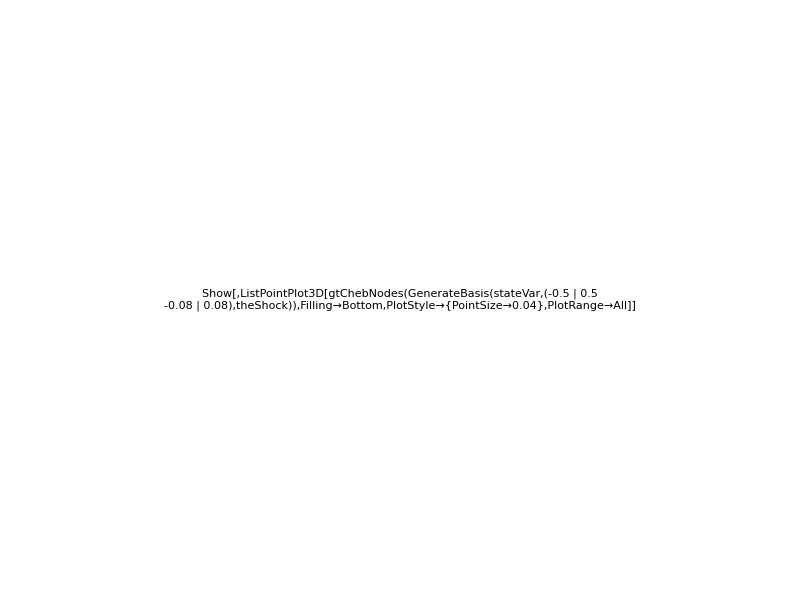

```mathematica
GraphicsRow[{Show[rr3d01,uupts01],Show[rr3d02,uupts02]},ImageSize->800,DisplayFunction->(PopupWindow[Button["Click here"],#]&)]
```

```mathematica
Plot3D @@ ({polys1$1$100[[-1]]/.uu$Shock->0,{qq,qLow,qHigh},{ru,ruLow,ruHigh}}//.lucaSubs)
```

Part::partd: Part specification polys1$1$100 ⟦ -1 ⟧ is longer than depth of object.

-Graphics3D-

```mathematica
boo=res1$1$100[toOrder[{3,1,1}]]
```

«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.ProjectionResults]»

```mathematica
boo[isConvergedQ[]]
```

True

```mathematica
fv=getAllFVals[boo];
Norm/@ fv[[1]]
```

ComputeInitialCollocationWeights[GenerateBasis[stateVar,{{-0.5,0.5},{-0.08,0.08}},{1,1},theShock,{0},{0.01},{50},{1},nonStateVar],genLucaMat[GenerateBasis[stateVar,{{-0.5,0.5},{-0.08,0.08}},{1,1},theShock,{0},{0.01},{50},{1},nonStateVar]],modEqns00,«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy]»][Norm[incOrder[{1,0,0}]]]

```mathematica
(polysboo=CreatePolynomials[lucaMod00,boo]//Chop//ExpandAll(*Chop drops very small terms*))//TableForm
```

CreatePolynomials[lucaMod00,ComputeInitialCollocationWeights[GenerateBasis[stateVar,{{-0.5,0.5},{-0.08,0.08}},{1,1},theShock,{0},{0.01},{50},{1},nonStateVar],genLucaMat[GenerateBasis[stateVar,{{-0.5,0.5},{-0.08,0.08}},{1,1},theShock,{0},{0.01},{50},{1},nonStateVar]],modEqns00,«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy]»][incOrder[{1,0,0}]]]

```mathematica
polyFunc= Function @@ {{qq,ru,uu$Shock},polysboo[[3]]};
rrPts=Append[#,polyFunc @@ #]&/@gtChebNodes[boo[getTheWeightedStochasticBasis[]]];
guuPts=gatherByShocks[rrPts];
```

Part::partw: Part 3 of lucaMod00, ComputeInitialCollocationWeights[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1, 1}, theShock, {0}, {0.01`}, {50}, {1}, nonStateVar], genLucaMat[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1, 1}, theShock, {0}, {0.01`}, {50}, {1}, nonStateVar]], modEqns00, InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm2`JavaObject34338755556933633]][incOrder[{1, 0, 0}]] does not exist.

Function::fpct: Too many parameters in {qq, ru, uu$Shock} to be filled from Function[{qq, ru, uu$Shock}, CreatePolynomials[lucaMod00, ComputeInitialCollocationWeights[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1, 1}, theShock, {0}, {0.01`}, {50}, {1}, nonStateVar], genLucaMat[GenerateBasis[stateVar, {{« 2 »}, {« 2 »}}, {1, 1}, theShock, {0}, {0.01`}, {50}, {1}, nonStateVar]], modEqns00, InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm2`JavaObject34338755556933633]][incOrder[{1, 0, 0}]]] ⟦ 3 ⟧].

General::stop: Further output of Function :: fpct will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

```mathematica
uupts01=ListPointPlot3D @@ {guuPts[[1,All,{1,2,4}]],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All};
```

Part::partw: Part {1, 2, 4} of ComputeInitialCollocationWeights[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1, 1}, theShock, {0}, {0.01`}, {50}, {1}, nonStateVar], genLucaMat[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1, 1}, theShock, {0}, {0.01`}, {50}, {1}, nonStateVar]], modEqns00, InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm2`JavaObject34338755556933633]][incOrder[{1, 0, 0}]] does not exist.

Part::partw: Part {1, 2, 4} of ComputeInitialCollocationWeights[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1.`16., 1.`16.}, theShock, {0}, {0.01`}, {50.`16.}, {1.`16.}, nonStateVar], genLucaMat[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1.`16., 1.`16.}, theShock, {0}, {0.01`}, {50.`16.}, {1.`16.}, nonStateVar]], modEqns00, InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm2`JavaObject34338755556933633]][incOrder[{1.`16., 0, 0}]] does not exist.

Part::partw: Part {1, 2, 4} of ComputeInitialCollocationWeights[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1.`, 1.`}, theShock, {0.`}, {0.01`}, {50.`}, {1.`}, nonStateVar], genLucaMat[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1.`, 1.`}, theShock, {0.`}, {0.01`}, {50.`}, {1.`}, nonStateVar]], modEqns00, InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm2`JavaObject34338755556933633]][incOrder[{1.`, 0.`, 0.`}]] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ListPointPlot3D::arrayerr: gatherByShocks[gtChebNodes[ComputeInitialCollocationWeights[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1, 1}, theShock, {0}, {0.01`}, {50}, {1}, nonStateVar], genLucaMat[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1, 1}, theShock, {0}, {0.01`}, {50}, {1}, nonStateVar]], modEqns00, InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm2`JavaObject34338755556933633]][incOrder[{1, 0, 0}]][getTheWeightedStochasticBasis[], Hold[Function[{qq, ru, uu$Shock}, CreatePolynomials[lucaMod00, ComputeInitialCollocationWeights[« 4 »][« 1 »]] ⟦ 3 ⟧][getTheWeightedStochasticBasis[]]]]]] must be a valid array or a list of valid arrays.

General::stop: Further output of ListPointPlot3D :: arrayerr will be suppressed during this calculation.

```mathematica
uupts02=ListPointPlot3D @@ {guuPts[[2,All,{1,2,4}]],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All};
```

Part::partw: Part 2 of gtChebNodes[ComputeInitialCollocationWeights[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1, 1}, theShock, {0}, {0.01`}, {50}, {1}, nonStateVar], genLucaMat[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1, 1}, theShock, {0}, {0.01`}, {50}, {1}, nonStateVar]], modEqns00, InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm2`JavaObject34338755556933633]][incOrder[{1, 0, 0}]][getTheWeightedStochasticBasis[], Hold[Function[{qq, ru, uu$Shock}, CreatePolynomials[lucaMod00, ComputeInitialCollocationWeights[« 4 »][« 1 »]] ⟦ 3 ⟧][getTheWeightedStochasticBasis[]]]]] does not exist.

Part::partw: Part 2 of gtChebNodes[ComputeInitialCollocationWeights[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1.`16., 1.`16.}, theShock, {0}, {0.01`}, {50.`16.}, {1.`16.}, nonStateVar], genLucaMat[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1.`16., 1.`16.}, theShock, {0}, {0.01`}, {50.`16.}, {1.`16.}, nonStateVar]], modEqns00, InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm2`JavaObject34338755556933633]][incOrder[{1.`16., 0, 0}]][getTheWeightedStochasticBasis[], Hold[Function[{qq, ru, uu$Shock}, CreatePolynomials[lucaMod00, ComputeInitialCollocationWeights[« 4 »][« 1 »]] ⟦ 3 ⟧][getTheWeightedStochasticBasis[]]]]] does not exist.

Part::partw: Part 2 of gtChebNodes[ComputeInitialCollocationWeights[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1.`, 1.`}, theShock, {0.`}, {0.01`}, {50.`}, {1.`}, nonStateVar], genLucaMat[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1.`, 1.`}, theShock, {0.`}, {0.01`}, {50.`}, {1.`}, nonStateVar]], modEqns00, InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm2`JavaObject34338755556933633]][incOrder[{1.`, 0.`, 0.`}]][getTheWeightedStochasticBasis[], Hold[Function[{qq, ru, uu$Shock}, CreatePolynomials[lucaMod00, ComputeInitialCollocationWeights[« 4 »][« 1 »]] ⟦ 3 ⟧][getTheWeightedStochasticBasis[]]]]] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ListPointPlot3D::arrayerr: gatherByShocks[gtChebNodes[ComputeInitialCollocationWeights[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1, 1}, theShock, {0}, {0.01`}, {50}, {1}, nonStateVar], genLucaMat[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1, 1}, theShock, {0}, {0.01`}, {50}, {1}, nonStateVar]], modEqns00, InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm2`JavaObject34338755556933633]][incOrder[{1, 0, 0}]][getTheWeightedStochasticBasis[], Hold[Function[{qq, ru, uu$Shock}, CreatePolynomials[lucaMod00, ComputeInitialCollocationWeights[« 4 »][« 1 »]] ⟦ 3 ⟧][getTheWeightedStochasticBasis[]]]]]] must be a valid array or a list of valid arrays.

General::stop: Further output of ListPointPlot3D :: arrayerr will be suppressed during this calculation.

```mathematica
rr3d01=Plot3D @@ ({{RUB,polysboo[[3]]}/.uu$Shock->guuPts[[1,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs);
```

Part::partw: Part 3 of lucaMod00, ComputeInitialCollocationWeights[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1, 1}, theShock, {0}, {0.01`}, {50}, {1}, nonStateVar], genLucaMat[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1, 1}, theShock, {0}, {0.01`}, {50}, {1}, nonStateVar]], modEqns00, InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm2`JavaObject34338755556933633]][incOrder[{1, 0, 0}]] does not exist.

Part::partw: Part 3 of ComputeInitialCollocationWeights[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1, 1}, theShock, {0}, {0.01`}, {50}, {1}, nonStateVar], genLucaMat[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1, 1}, theShock, {0}, {0.01`}, {50}, {1}, nonStateVar]], modEqns00, InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm2`JavaObject34338755556933633]][incOrder[{1, 0, 0}]] does not exist.

Part::partw: Part 3 of lucaMod00, ComputeInitialCollocationWeights[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1.`, 1.`}, theShock, {0.`}, {0.01`}, {50.`}, {1.`}, nonStateVar], genLucaMat[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1.`, 1.`}, theShock, {0.`}, {0.01`}, {50.`}, {1.`}, nonStateVar]], modEqns00, InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm2`JavaObject34338755556933633]][incOrder[{1.`, 0.`, 0.`}]] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
rr3d02=Plot3D @@ ({{RUB,polysboo[[3]]}/.uu$Shock->guuPts[[2,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs);
```

Part::partw: Part 3 of lucaMod00, ComputeInitialCollocationWeights[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1, 1}, theShock, {0}, {0.01`}, {50}, {1}, nonStateVar], genLucaMat[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1, 1}, theShock, {0}, {0.01`}, {50}, {1}, nonStateVar]], modEqns00, InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm2`JavaObject34338755556933633]][incOrder[{1, 0, 0}]] does not exist.

Part::partw: Part 2 of gtChebNodes[ComputeInitialCollocationWeights[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1, 1}, theShock, {0}, {0.01`}, {50}, {1}, nonStateVar], genLucaMat[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1, 1}, theShock, {0}, {0.01`}, {50}, {1}, nonStateVar]], modEqns00, InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm2`JavaObject34338755556933633]][incOrder[{1, 0, 0}]][getTheWeightedStochasticBasis[], Hold[Function[{qq, ru, uu$Shock}, CreatePolynomials[lucaMod00, ComputeInitialCollocationWeights[« 4 »][« 1 »]] ⟦ 3 ⟧][getTheWeightedStochasticBasis[]]]]] does not exist.

Part::partw: Part 3 of lucaMod00, ComputeInitialCollocationWeights[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1.`, 1.`}, theShock, {0.`}, {0.01`}, {50.`}, {1.`}, nonStateVar], genLucaMat[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1.`, 1.`}, theShock, {0.`}, {0.01`}, {50.`}, {1.`}, nonStateVar]], modEqns00, InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm2`JavaObject34338755556933633]][incOrder[{1.`, 0.`, 0.`}]] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
GraphicsRow[{Show[rr3d01,uupts01],Show[rr3d02,uupts02]},ImageSize->800,DisplayFunction->(PopupWindow[Button["Click here"],#]&)]
```

Part::partw: Part {1, 2, 4} of ComputeInitialCollocationWeights[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1, 1}, theShock, {0}, {0.01`}, {50}, {1}, nonStateVar], genLucaMat[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1, 1}, theShock, {0}, {0.01`}, {50}, {1}, nonStateVar]], modEqns00, InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm2`JavaObject34338755556933633]][incOrder[{1, 0, 0}]] does not exist.

Part::partw: Part {1, 2, 4} of ComputeInitialCollocationWeights[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1.`16., 1.`16.}, theShock, {0}, {0.01`}, {50.`16.}, {1.`16.}, nonStateVar], genLucaMat[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1.`16., 1.`16.}, theShock, {0}, {0.01`}, {50.`16.}, {1.`16.}, nonStateVar]], modEqns00, InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm2`JavaObject34338755556933633]][incOrder[{1.`16., 0, 0}]] does not exist.

Part::partw: Part {1, 2, 4} of ComputeInitialCollocationWeights[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1.`, 1.`}, theShock, {0.`}, {0.01`}, {50.`}, {1.`}, nonStateVar], genLucaMat[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1.`, 1.`}, theShock, {0.`}, {0.01`}, {50.`}, {1.`}, nonStateVar]], modEqns00, InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm2`JavaObject34338755556933633]][incOrder[{1.`, 0.`, 0.`}]] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ListPointPlot3D::arrayerr: gatherByShocks[gtChebNodes[ComputeInitialCollocationWeights[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1, 1}, theShock, {0}, {0.01`}, {50}, {1}, nonStateVar], genLucaMat[GenerateBasis[stateVar, {{-0.5`, 0.5`}, {-0.08`, 0.08`}}, {1, 1}, theShock, {0}, {0.01`}, {50}, {1}, nonStateVar]], modEqns00, InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm2`JavaObject34338755556933633]][incOrder[{1, 0, 0}]][getTheWeightedStochasticBasis[], Hold[Function[{qq, ru, uu$Shock}, CreatePolynomials[lucaMod00, ComputeInitialCollocationWeights[« 4 »][« 1 »]] ⟦ 3 ⟧][getTheWeightedStochasticBasis[]]]]]] must be a valid array or a list of valid arrays.

General::stop: Further output of ListPointPlot3D :: arrayerr will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

-Graphics-

```mathematica
boo=res1$1$100[incOrder[{1,1,1}]];
boo[isConvergedQ[]]
```

ComputeInitialCollocationWeights[GenerateBasis[stateVar,{{-0.5,0.5},{-0.08,0.08}},{1,1},theShock,{0},{0.01},{50},{1},nonStateVar],genLucaMat[GenerateBasis[stateVar,{{-0.5,0.5},{-0.08,0.08}},{1,1},theShock,{0},{0.01},{50},{1},nonStateVar]],modEqns00,«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy]»][incOrder[{1,1,1}]][isConvergedQ[]]

```mathematica
boo=res1$1$100[incOrder[{2,0,0}]];
boo[isConvergedQ[]]
```

ComputeInitialCollocationWeights[GenerateBasis[stateVar,{{-0.5,0.5},{-0.08,0.08}},{1,1},theShock,{0},{0.01},{50},{1},nonStateVar],genLucaMat[GenerateBasis[stateVar,{{-0.5,0.5},{-0.08,0.08}},{1,1},theShock,{0},{0.01},{50},{1},nonStateVar]],modEqns00,«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy]»][incOrder[{2,0,0}]][isConvergedQ[]]

## eval barrier

```mathematica
boo01=res1$1$100[incOrder[{1,1,1}]];
boo01[isConvergedQ[]]
```

True

```mathematica
boo02=boo01[incOrder[{1,1,1}]];
boo02[isConvergedQ[]]
```

True

```mathematica
bf=getAllFVals[boo02];Norm/@ bf[[1]]
```

{0.0928097,0.0264563,0.000739457,0.000140354,0.0000266403,5.05653×10^-6,9.59767×10^-7,1.82171×10^-7,3.45774×10^-8,6.56305×10^-9}

```mathematica
ClassName[res1$1$100]
```

gov.frb.ma.msu.ProjectionMethodToolsJava.ProjectionResults

#### Solution for two periods

Provide Model Equations and Generate an instance of the Model’s Class ( a Subclass of DoEqns )

```mathematica
lucaSubs={betap->99/100,phip->1,rhop->1/2,sigmap->1,rUnderBar->2/100,qLow->-.5,qHigh->.5,ruLow-> -4*sigma$u/(1-rho$ru),ruHigh->  4*sigma$u/(1-rho$ru),integOrder->{50},sigma$u->0.01,theMean->{0},rho$ru-> 0.5,adj->1};lucaReliableEqns=genSys[1];
(*rr[t]-eqvdIf[lambda[t]≥0,rUnderBar,phip*qq[t]] should fix codesubs*)
newWeightedStochasticBasis[lucaMod01,lucaReliableEqns];
(*Profile[*)Identity[
Timing[{{stateVar,nonStateVar,theShock},modEqns01}=GenerateModelCode[lucaMod01];]
]
modEqns01[updateParams[modParams]]
```

```mathematica
Trace[{{stateVar,nonStateVar,theShock},modEqns01}=GenerateModelCode[lucaMod01],ProjectionInterface`Private`intTermOrNot[___],TraceForward->True]
```

```mathematica
??ProjectionInterface`Private`intTermOrNot
```

A list of equations constitutes the model’s definition. The state and non-state variables are of the form symbolName[t-1|t|t+1]. The shocks are of the form eps[symbolName][t].  The shocks and the variables with time index t-1 constitute the state variables. The newWeigthedStochasticBasis function associates features of the model definition with Mathematica upvalues of a variable.

```mathematica
polyRange={{qLow,qHigh},{ruLow,ruHigh}}/.lucaSubs;
initPower={1,1};shockPower={1};
lucaBasis=GenerateBasis[stateVar,polyRange//.lucaSubs,initPower,theShock,theMean//.lucaSubs,{sigma$u}//.lucaSubs,integOrder//.lucaSubs,shockPower,nonStateVar];
```

```mathematica
{stateVar,nonStateVar,theShock}
```

```mathematica
polyRange//.lucaSubs
```

```mathematica
lucaMat//Dimensions
```

```mathematica
<<ProjectionInterface`
```

compute first order projection

```mathematica
lucaMat=genLucaMat[lucaBasis];
simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
res1$1$101=ComputeInitialCollocationWeights[lucaBasis,lucaMat,modEqns01,simp];If[res1$1$101[isConvergedQ[]],
polys1$1$101=CreatePolynomials[lucaMod01,res1$1$101]//Chop(*Chop drops very small terms*),Print["ComputeInitialCollocationWeights did not converge"],PrintForm["ComputeInitialCollocationWeights did not converge"]];
```

```mathematica
res1$1$101[isConvergedQ[]]
```

```mathematica
Dimensions[polys1$1$101]
```

```mathematica
fv=getAllFVals[res1$1$101];
Norm/@ fv[[1]]
```

```mathematica
polys1$1$101//ExpandAll//Chop//TableForm
```

#### Solution for three periods

Provide Model Equations and Generate an instance of the Model’s Class ( a Subclass of DoEqns )

```mathematica
lucaSubs={betap->99/100,phip->1,rhop->1/2,sigmap->1,rUnderBar->2/100,qLow->-.5,qHigh->.5,ruLow-> -4*sigma$u/(1-rho$ru),ruHigh->  4*sigma$u/(1-rho$ru),integOrder->{50},sigma$u->0.01,theMean->{0},rho$ru-> 0.5,adj->1};lucaReliableEqns=genSys[2];
(*rr[t]-eqvdIf[lambda[t]≥0,rUnderBar,phip*qq[t]] should fix codesubs*)
newWeightedStochasticBasis[lucaMod02,lucaReliableEqns];
{{stateVar,nonStateVar,theShock},modEqns02}=GenerateModelCode[lucaMod02];
```

ingenmodcode:$Failed{{qq,ru},{qq$tp1,qq$tp2,rr,zzz$0$1,zzz$1$1,zzz$2$1},{uu$Shock}}

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod02.java

allSubs={qq[1+t]:>qq$tp1,qq[2+t]:>qq$tp2}

ingenmodcode:«JavaObject[lucaMod02]»{{qq,ru},{qq$tp1,qq$tp2,rr,zzz$0$1,zzz$1$1,zzz$2$1},{uu$Shock}}

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod02.java

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod02.java

ingenmodcode:«JavaObject[lucaMod02]»{{qq,ru},{qq$tp1,qq$tp2,rr,zzz$0$1,zzz$1$1,zzz$2$1},{uu$Shock}}

A list of equations constitutes the model’s definition. The state and non-state variables are of the form symbolName[t-1|t|t+1]. The shocks are of the form eps[symbolName][t].  The shocks and the variables with time index t-1 constitute the state variables. The newWeigthedStochasticBasis function associates features of the model definition with Mathematica upvalues of a variable.

```mathematica
lucaReliableEqns//ExpandAll
```

```mathematica
{0.26774226536389173 qq[-1+t]-qq[t]+0.3086481523403434 ru[-1+t]-0.5354845307277833 zzz$0$1[t]-0.14193812291113342 zzz$1$1[t]-0.0376228062240281 zzz$2$1[t]+0.6172963046806865 eps[uu][t],0.26774226536389173 qq[-1+t]-rr[t]+0.3086481523403434 ru[-1+t]+0.4645154692722166 zzz$0$1[t]-0.14193812291113342 zzz$1$1[t]-0.0376228062240281 zzz$2$1[t]+0.6172963046806865 eps[uu][t],0.5 ru[-1+t]-ru[t]+1. eps[uu][t],-qq[1+t]+qq$tp1[t],-qq$tp1[1+t]+qq$tp2[t],-eqvdIf[qq$tp2≥0.01,0,0.01-qq$tp2]+zzz$0$1[t],-eqvdIf[qq[1+t]≥0.01,0,0.01-qq[1+t]]+zzz$1$1[t],-eqvdIf[qq[t]≥0.01,0,0.01-qq[t]]+zzz$2$1[t]}
```

```mathematica
(*
modParams={adj,betap,phip,rhop, rho$ru,rUnderBar,sigmap}//.lucaSubs//N;
modEqns02[updateParams[modParams]]*)
```

```mathematica
polyRange={{qLow,qHigh},{ruLow,ruHigh}}/.lucaSubs;
initPower={1,1};shockPower={1};
lucaBasis=GenerateBasis[stateVar,polyRange//.lucaSubs,initPower,theShock,theMean//.lucaSubs,{sigma$u}//.lucaSubs,integOrder//.lucaSubs,shockPower,nonStateVar];
```

```mathematica
{stateVar,nonStateVar,theShock}
```

```mathematica
polyRange//.lucaSubs
```

compute first order projection

```mathematica
(*the matrix should have a row for each state variable and each shock*)(*the matrix should have a column for each basis polynomial*)
(*lucaMat=ConstantArray[0,{3,8}];lucaMat=ReplacePart[lucaMat,{{1,3}->0.292289,{2,3}->rho$ru,{3,3}->0.299289,{1,5}->-.53,{3,5}->-53,{2,5}->-1}]//.lucaSubs*)
(*lucaBasis[setAllWeights[lucaMat]]*)
```

```mathematica
simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
res1$1$102=ComputeInitialCollocationWeights[lucaBasis,Table[3*Random[],{Length[stateVar]+Length[nonStateVar]},{8}],modEqns02,simp];If[res1$1$102[isConvergedQ[]],
polys1$1$102=CreatePolynomials[lucaMod02,res1$1$102]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge","ComputeInitialCollocationWeights did not converge"];
```

```mathematica
res1$1$102[isConvergedQ[]]
```

```mathematica
Dimensions[polys1$1$102]
```

```mathematica
fv=getAllFVals[res1$1$102];
Norm/@ fv[[1]]
```

```mathematica
polys1$1$102//ExpandAll//Chop//TableForm
```

#### Solution for four periods

Provide Model Equations and Generate an instance of the Model’s Class ( a Subclass of DoEqns )

```mathematica
lucaSubs={betap->99/100,phip->1,rhop->1/2,sigmap->1,rUnderBar->2/100,qLow->-.5,qHigh->.5,ruLow-> -4*sigma$u/(1-rho$ru),ruHigh->  4*sigma$u/(1-rho$ru),integOrder->{50},sigma$u->0.01,theMean->{0},rho$ru-> 0.5,adj->1};lucaReliableEqns=genSys[3];
(*rr[t]-eqvdIf[lambda[t]≥0,rUnderBar,phip*qq[t]] should fix codesubs*)
newWeightedStochasticBasis[lucaMod03,lucaReliableEqns];
{{stateVar,nonStateVar,theShock},modEqns03}=GenerateModelCode[lucaMod03];
```

ingenmodcode:$Failed{{qq,ru},{qq$tp1,qq$tp2,qq$tp3,rr,zzz$0$1,zzz$1$1,zzz$2$1,zzz$3$1},{uu$Shock}}

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod03.java

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod03.java

ingenmodcode:«JavaObject[lucaMod02]»{{qq,ru},{qq$tp1,qq$tp2,rr,zzz$0$1,zzz$1$1,zzz$2$1},{uu$Shock}}

A list of equations constitutes the model’s definition. The state and non-state variables are of the form symbolName[t-1|t|t+1]. The shocks are of the form eps[symbolName][t].  The shocks and the variables with time index t-1 constitute the state variables. The newWeigthedStochasticBasis function associates features of the model definition with Mathematica upvalues of a variable.

```mathematica
modEqns03
```

```mathematica
lucaReliableEqns//ExpandAll//TableForm
```

```mathematica
(*
modParams={adj,betap,phip,rhop, rho$ru,rUnderBar,sigmap}//.lucaSubs//N;
modEqns03[updateParams[modParams]]*)
```

```mathematica
polyRange={{qLow,qHigh},{ruLow,ruHigh}}/.lucaSubs;
initPower={1,1};shockPower={1};
lucaBasis=GenerateBasis[stateVar,polyRange//.lucaSubs,initPower,theShock,theMean//.lucaSubs,{sigma$u}//.lucaSubs,integOrder//.lucaSubs,shockPower,nonStateVar];
```

```mathematica
{stateVar,nonStateVar,theShock}
```

```mathematica
polyRange//.lucaSubs
```

compute first order projection

```mathematica
(*the matrix should have a row for each state variable and each shock*)(*the matrix should have a column for each basis polynomial*)
(*lucaMat=ConstantArray[0,{3,8}];lucaMat=ReplacePart[lucaMat,{{1,3}->0.292289,{2,3}->rho$ru,{3,3}->0.299289,{1,5}->-.53,{3,5}->-53,{2,5}->-1}]//.lucaSubs*)
(*lucaBasis[setAllWeights[lucaMat]]*)
```

```mathematica
simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
res1$1$103=ComputeInitialCollocationWeights[lucaBasis,Table[3*Random[],{Length[stateVar]+Length[nonStateVar]},{8}],modEqns03,simp];If[res1$1$103[isConvergedQ[]],
polys1$1$103=CreatePolynomials[lucaMod03,res1$1$103]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge","ComputeInitialCollocationWeights did not converge"];
```

```mathematica
res1$1$103[isConvergedQ[]]
```

```mathematica
Dimensions[polys1$1$103]
```

```mathematica
fv=getAllFVals[res1$1$103];
Norm/@ fv[[1]]
```

```mathematica
polys1$1$103//ExpandAll//FullSimplify//Chop//TableForm
```

#### Solution for five periods

Provide Model Equations and Generate an instance of the Model’s Class ( a Subclass of DoEqns )

```mathematica
lucaSubs={betap->99/100,phip->1,rhop->1/2,sigmap->1,rUnderBar->2/100,qLow->-.5,qHigh->.5,ruLow-> -4*sigma$u/(1-rho$ru),ruHigh->  4*sigma$u/(1-rho$ru),integOrder->{50},sigma$u->0.01,theMean->{0},rho$ru-> 0.5,adj->1};lucaReliableEqns=genSys[4];
(*rr[t]-eqvdIf[lambda[t]≥0,rUnderBar,phip*qq[t]] should fix codesubs*)
newWeightedStochasticBasis[lucaMod04,lucaReliableEqns];
{{stateVar,nonStateVar,theShock},modEqns04}=GenerateModelCode[lucaMod04];
```

ingenmodcode:$Failed{{qq,ru},{qq$tp1,qq$tp2,qq$tp3,rr,zzz$0$1,zzz$1$1,zzz$2$1,zzz$3$1},{uu$Shock}}

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod03.java

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod03.java

ingenmodcode:«JavaObject[lucaMod02]»{{qq,ru},{qq$tp1,qq$tp2,rr,zzz$0$1,zzz$1$1,zzz$2$1},{uu$Shock}}

A list of equations constitutes the model’s definition. The state and non-state variables are of the form symbolName[t-1|t|t+1]. The shocks are of the form eps[symbolName][t].  The shocks and the variables with time index t-1 constitute the state variables. The newWeigthedStochasticBasis function associates features of the model definition with Mathematica upvalues of a variable.

```mathematica
lucaReliableEqns//ExpandAll//TableForm
```

```mathematica
(*
modParams={adj,betap,phip,rhop, rho$ru,rUnderBar,sigmap}//.lucaSubs//N;
modEqns03[updateParams[modParams]]*)
```

```mathematica
polyRange={{qLow,qHigh},{ruLow,ruHigh}}/.lucaSubs;
initPower={1,1};shockPower={1};
lucaBasis=GenerateBasis[stateVar,polyRange//.lucaSubs,initPower,theShock,theMean//.lucaSubs,{sigma$u}//.lucaSubs,integOrder//.lucaSubs,shockPower,nonStateVar];
```

```mathematica
{stateVar,nonStateVar,theShock}
```

```mathematica
polyRange//.lucaSubs
```

compute first order projection

```mathematica
(*the matrix should have a row for each state variable and each shock*)(*the matrix should have a column for each basis polynomial*)
(*lucaMat=ConstantArray[0,{3,8}];lucaMat=ReplacePart[lucaMat,{{1,3}->0.292289,{2,3}->rho$ru,{3,3}->0.299289,{1,5}->-.53,{3,5}->-53,{2,5}->-1}]//.lucaSubs*)
(*lucaBasis[setAllWeights[lucaMat]]*)
```

```mathematica
simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
res1$1$104=ComputeInitialCollocationWeights[lucaBasis,Table[3*Random[],{Length[stateVar]+Length[nonStateVar]},{8}],modEqns04,simp];If[res1$1$104[isConvergedQ[]],
polys1$1$104=CreatePolynomials[lucaMod04,res1$1$104]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge","ComputeInitialCollocationWeights did not converge"];
```

```mathematica
res1$1$104[isConvergedQ[]]
```

```mathematica
Dimensions[polys1$1$104]
```

```mathematica
fv=getAllFVals[res1$1$104];
Norm/@ fv[[1]]
```

```mathematica
polys1$1$104//ExpandAll//FullSimplify//Chop//TableForm
```

#### Solution for six periods

Provide Model Equations and Generate an instance of the Model’s Class ( a Subclass of DoEqns )

```mathematica
lucaSubs={betap->99/100,phip->1,rhop->1/2,sigmap->1,rUnderBar->2/100,qLow->-.5,qHigh->.5,ruLow-> -4*sigma$u/(1-rho$ru),ruHigh->  4*sigma$u/(1-rho$ru),integOrder->{50},sigma$u->0.01,theMean->{0},rho$ru-> 0.5,adj->1};lucaReliableEqns=genSys[5];
(*rr[t]-eqvdIf[lambda[t]≥0,rUnderBar,phip*qq[t]] should fix codesubs*)
newWeightedStochasticBasis[lucaMod05,lucaReliableEqns];
{{stateVar,nonStateVar,theShock},modEqns05}=GenerateModelCode[lucaMod05];
```

ingenmodcode:$Failed{{qq,ru},{qq$tp1,qq$tp2,qq$tp3,rr,zzz$0$1,zzz$1$1,zzz$2$1,zzz$3$1},{uu$Shock}}

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod03.java

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod03.java

ingenmodcode:«JavaObject[lucaMod02]»{{qq,ru},{qq$tp1,qq$tp2,rr,zzz$0$1,zzz$1$1,zzz$2$1},{uu$Shock}}

A list of equations constitutes the model’s definition. The state and non-state variables are of the form symbolName[t-1|t|t+1]. The shocks are of the form eps[symbolName][t].  The shocks and the variables with time index t-1 constitute the state variables. The newWeigthedStochasticBasis function associates features of the model definition with Mathematica upvalues of a variable.

```mathematica
lucaReliableEqns//ExpandAll//TableForm
```

```mathematica
(*
modParams={adj,betap,phip,rhop, rho$ru,rUnderBar,sigmap}//.lucaSubs//N;
modEqns03[updateParams[modParams]]*)
```

```mathematica
polyRange={{qLow,qHigh},{ruLow,ruHigh}}/.lucaSubs;
initPower={1,1};shockPower={1};
lucaBasis=GenerateBasis[stateVar,polyRange//.lucaSubs,initPower,theShock,theMean//.lucaSubs,{sigma$u}//.lucaSubs,integOrder//.lucaSubs,shockPower,nonStateVar];
```

```mathematica
{stateVar,nonStateVar,theShock}
```

```mathematica
polyRange//.lucaSubs
```

compute first order projection

```mathematica
(*the matrix should have a row for each state variable and each shock*)(*the matrix should have a column for each basis polynomial*)
(*lucaMat=ConstantArray[0,{3,8}];lucaMat=ReplacePart[lucaMat,{{1,3}->0.292289,{2,3}->rho$ru,{3,3}->0.299289,{1,5}->-.53,{3,5}->-53,{2,5}->-1}]//.lucaSubs*)
(*lucaBasis[setAllWeights[lucaMat]]*)
```

```mathematica
simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
res1$1$105=ComputeInitialCollocationWeights[lucaBasis,Table[3*Random[],{Length[stateVar]+Length[nonStateVar]},{8}],modEqns05,simp];If[res1$1$105[isConvergedQ[]],
polys1$1$105=CreatePolynomials[lucaMod05,res1$1$105]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge","ComputeInitialCollocationWeights did not converge"];
```

```mathematica
res1$1$105[isConvergedQ[]]
```

```mathematica
Dimensions[polys1$1$105]
```

```mathematica
fv=getAllFVals[res1$1$105];
Norm/@ fv[[1]]
```

```mathematica
polys1$1$105//ExpandAll//FullSimplify//Chop//TableForm
```

#### Solution for seven periods

Provide Model Equations and Generate an instance of the Model’s Class ( a Subclass of DoEqns )

```mathematica
lucaSubs={betap->99/100,phip->1,rhop->1/2,sigmap->1,rUnderBar->2/100,qLow->-.5,qHigh->.5,ruLow-> -4*sigma$u/(1-rho$ru),ruHigh->  4*sigma$u/(1-rho$ru),integOrder->{50},sigma$u->0.01,theMean->{0},rho$ru-> 0.5,adj->1};lucaReliableEqns=genSys[6];
(*rr[t]-eqvdIf[lambda[t]≥0,rUnderBar,phip*qq[t]] should fix codesubs*)
newWeightedStochasticBasis[lucaMod06,lucaReliableEqns];
{{stateVar,nonStateVar,theShock},modEqns06}=GenerateModelCode[lucaMod06];
```

ingenmodcode:$Failed{{qq,ru},{qq$tp1,qq$tp2,qq$tp3,rr,zzz$0$1,zzz$1$1,zzz$2$1,zzz$3$1},{uu$Shock}}

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod03.java

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod03.java

ingenmodcode:«JavaObject[lucaMod02]»{{qq,ru},{qq$tp1,qq$tp2,rr,zzz$0$1,zzz$1$1,zzz$2$1},{uu$Shock}}

A list of equations constitutes the model’s definition. The state and non-state variables are of the form symbolName[t-1|t|t+1]. The shocks are of the form eps[symbolName][t].  The shocks and the variables with time index t-1 constitute the state variables. The newWeigthedStochasticBasis function associates features of the model definition with Mathematica upvalues of a variable.

```mathematica
lucaReliableEqns//ExpandAll//TableForm
```

```mathematica
(*
modParams={adj,betap,phip,rhop, rho$ru,rUnderBar,sigmap}//.lucaSubs//N;
modEqns03[updateParams[modParams]]*)
```

```mathematica
polyRange={{qLow,qHigh},{ruLow,ruHigh}}/.lucaSubs;
initPower={1,1};shockPower={1};
lucaBasis=GenerateBasis[stateVar,polyRange//.lucaSubs,initPower,theShock,theMean//.lucaSubs,{sigma$u}//.lucaSubs,integOrder//.lucaSubs,shockPower,nonStateVar];
```

```mathematica
{stateVar,nonStateVar,theShock}
```

```mathematica
polyRange//.lucaSubs
```

compute first order projection

```mathematica
(*the matrix should have a row for each state variable and each shock*)(*the matrix should have a column for each basis polynomial*)
(*lucaMat=ConstantArray[0,{3,8}];lucaMat=ReplacePart[lucaMat,{{1,3}->0.292289,{2,3}->rho$ru,{3,3}->0.299289,{1,5}->-.53,{3,5}->-53,{2,5}->-1}]//.lucaSubs*)
(*lucaBasis[setAllWeights[lucaMat]]*)
```

```mathematica
simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
res1$1$106=ComputeInitialCollocationWeights[lucaBasis,Table[3*Random[],{Length[stateVar]+Length[nonStateVar]},{8}],modEqns06,simp];If[res1$1$106[isConvergedQ[]],
polys1$1$106=CreatePolynomials[lucaMod06,res1$1$106]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge","ComputeInitialCollocationWeights did not converge"];
```

```mathematica
res1$1$106[isConvergedQ[]]
```

```mathematica
Dimensions[polys1$1$106]
```

```mathematica
fv=getAllFVals[res1$1$106];
Norm/@ fv[[1]]
```

```mathematica
polys1$1$106//ExpandAll//FullSimplify//Chop//TableForm
```

#### Solution for eight periods

Provide Model Equations and Generate an instance of the Model’s Class ( a Subclass of DoEqns )

```mathematica
lucaSubs={betap->99/100,phip->1,rhop->1/2,sigmap->1,rUnderBar->2/100,qLow->-.5,qHigh->.5,ruLow-> -4*sigma$u/(1-rho$ru),ruHigh->  4*sigma$u/(1-rho$ru),integOrder->{50},sigma$u->0.01,theMean->{0},rho$ru-> 0.5,adj->1};lucaReliableEqns=genSys[7];
(*rr[t]-eqvdIf[lambda[t]≥0,rUnderBar,phip*qq[t]] should fix codesubs*)
newWeightedStochasticBasis[lucaMod07,lucaReliableEqns];
{{stateVar,nonStateVar,theShock},modEqns07}=GenerateModelCode[lucaMod07];
```

ingenmodcode:$Failed{{qq,ru},{qq$tp1,qq$tp2,qq$tp3,rr,zzz$0$1,zzz$1$1,zzz$2$1,zzz$3$1},{uu$Shock}}

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod03.java

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod03.java

ingenmodcode:«JavaObject[lucaMod02]»{{qq,ru},{qq$tp1,qq$tp2,rr,zzz$0$1,zzz$1$1,zzz$2$1},{uu$Shock}}

A list of equations constitutes the model’s definition. The state and non-state variables are of the form symbolName[t-1|t|t+1]. The shocks are of the form eps[symbolName][t].  The shocks and the variables with time index t-1 constitute the state variables. The newWeigthedStochasticBasis function associates features of the model definition with Mathematica upvalues of a variable.

```mathematica
lucaReliableEqns//ExpandAll//TableForm
```

```mathematica
(*
modParams={adj,betap,phip,rhop, rho$ru,rUnderBar,sigmap}//.lucaSubs//N;
modEqns03[updateParams[modParams]]*)
```

```mathematica
polyRange={{qLow,qHigh},{ruLow,ruHigh}}/.lucaSubs;
initPower={1,1};shockPower={1};
lucaBasis=GenerateBasis[stateVar,polyRange//.lucaSubs,initPower,theShock,theMean//.lucaSubs,{sigma$u}//.lucaSubs,integOrder//.lucaSubs,shockPower,nonStateVar];
```

```mathematica
{stateVar,nonStateVar,theShock}
```

```mathematica
polyRange//.lucaSubs
```

compute first order projection

```mathematica
(*the matrix should have a row for each state variable and each shock*)(*the matrix should have a column for each basis polynomial*)
(*lucaMat=ConstantArray[0,{3,8}];lucaMat=ReplacePart[lucaMat,{{1,3}->0.292289,{2,3}->rho$ru,{3,3}->0.299289,{1,5}->-.53,{3,5}->-53,{2,5}->-1}]//.lucaSubs*)
(*lucaBasis[setAllWeights[lucaMat]]*)
```

```mathematica
simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
res1$1$107=ComputeInitialCollocationWeights[lucaBasis,Table[3*Random[],{Length[stateVar]+Length[nonStateVar]},{8}],modEqns07,simp];If[res1$1$107[isConvergedQ[]],
polys1$1$107=CreatePolynomials[lucaMod07,res1$1$107]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge","ComputeInitialCollocationWeights did not converge"];
```

```mathematica
res1$1$107[isConvergedQ[]]
```

```mathematica
Dimensions[polys1$1$107]
```

```mathematica
fv=getAllFVals[res1$1$107];
Norm/@ fv[[1]]
```

```mathematica
polys1$1$107//ExpandAll//FullSimplify//Chop//TableForm
```

```mathematica
lucaSubs
```

```mathematica
{polys1$1$106/.uu$Shock->0,{qq,qLow,qHigh},{ru,ruLow,ruHigh}}//.lucaSubs
```

```mathematica
Plot3D @@ ({polys1$1$106[[-1]]/.uu$Shock->0,{qq,qLow,qHigh},{ru,ruLow,ruHigh}}//.lucaSubs)
```

```mathematica
Plot3D @@ ({polys1$1$107[[-1]]/.uu$Shock->0,{qq,qLow,qHigh},{ru,ruLow,ruHigh}}//.lucaSubs)
```

```mathematica
Plot3D @@ ({(polys1$1$105[[-1]]-polys1$1$104[[-1]])/.uu$Shock->0,{qq,qLow,qHigh},{ru,ruLow,ruHigh}}//.lucaSubs)
```

### No Bootstrapping But With Substitution for last z

#### Solution for a single period

Provide Model Equations and Generate an instance of the Model’s Class ( a Subclass of DoEqns )

```mathematica
lucaSubs={betap->99/100,phip->1,rhop->1/2,sigmap->1,rUnderBar->2/100,qLow->-.5,qHigh->.5,ruLow-> -4*sigma$u/(1-rho$ru),ruHigh->  4*sigma$u/(1-rho$ru),integOrder->{50},sigma$u->0.01,theMean->{0},rho$ru-> 0.5,adj->1};(lucaReliableEqnsNot=genSys[0])//InputForm;
lucaSubs={betap->99/100,phip->1,rhop->1/2,sigmap->1,rUnderBar->2/100,qLow->-.5,qHigh->.5,ruLow-> -4*sigma$u/(1-rho$ru),ruHigh->  4*sigma$u/(1-rho$ru),integOrder->{20},sigma$u->0.01,theMean->{0},rho$ru-> 0.5,adj->1};
modParams={adj,betap,phip,rhop, rho$ru,rUnderBar,sigmap}//.lucaSubs//N;
```

```mathematica
(*{0.26774226536389173*qq[-1+t]-qq[t]+0.3086481523403434*ru[-1+t]-0.5354845307277833*zzz$0$1[t]+0.6172963046806865*eps[uu][t],0.26774226536389173*qq[-1+t]-rr[t]+0.3086481523403434*ru[-1+t]+0.4645154692722166*zzz$0$1[t]+0.6172963046806865*eps[uu][t],0.5*ru[-1+t]-ru[t]+1.*eps[uu][t],-eqvdIf[qq[t]≥0.01,0,0.01-qq[t]]+zzz$0$1[t]};*)
(*rr[t]-eqvdIf[lambda[t]≥0,rUnderBar,phip*qq[t]] should fix codesubs*)
lucaReliableEqns=genSysLaggedSubbed[0];(*{-eqvdIf[0.26774226536389173*qq[-1+t]+0.3086481523403434*ru[-1+t]+0.6172963046806865*eps[uu][t]≥-.01000,0.26774226536389173*qq[-1+t]+0.3086481523403434*ru[-1+t]+0.6172963046806865*eps[uu][t],-.01000]+qq[t],-eqvdIf[0.26774226536389173*qq[-1+t]+0.3086481523403434*ru[-1+t]+0.6172963046806865*eps[uu][t]≥-.01000,0.26774226536389173*qq[-1+t]+0.3086481523403434*ru[-1+t]+0.6172963046806865*eps[uu][t],-.01000]+rr[t],-0.5*ru[-1+t]+ru[t]-1.*eps[uu][t],-eqvdIf[0.26774226536389173*qq[-1+t]+0.3086481523403434*ru[-1+t]+0.6172963046806865*eps[uu][t]≥-.01000,0,-.0100-0.26774226536389173*qq[-1+t]-0.3086481523403434*ru[-1+t]-0.6172963046806865*eps[uu][t]]+zzz$0$1[t]}*)(*genSysLaggedSubbed[0]*)

newWeightedStochasticBasis[lucaMod00SubZ0,lucaReliableEqns];
Profile[Timing[{{stateVar,nonStateVar,theShock},modEqns00SubZ0}=GenerateModelCode[lucaMod00SubZ0]]]
modEqns00SubZ0[updateParams[modParams]]
```

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod00SubZ0.java

Profile[{0.,{{{qq,ru},{rr,zzz$0$1},{uu$Shock}},«JavaObject[lucaMod00SubZ0]»}}]

A list of equations constitutes the model’s definition. The state and non-state variables are of the form symbolName[t-1|t|t+1]. The shocks are of the form eps[symbolName][t].  The shocks and the variables with time index t-1 constitute the state variables. The newWeigthedStochasticBasis function associates features of the model definition with Mathematica upvalues of a variable.

```mathematica
polyRange={{qLow,qHigh},{ruLow,ruHigh}}/.lucaSubs;
initPower={1,1};shockPower={1};
lucaBasis=GenerateBasis[stateVar,polyRange//.lucaSubs,initPower,theShock,theMean//.lucaSubs,{sigma$u}//.lucaSubs,integOrder//.lucaSubs,shockPower,nonStateVar];
```

```mathematica
{stateVar,nonStateVar,theShock}
```

{{qq,ru},{rr,zzz$0$1},{uu$Shock}}

```mathematica
polyRange//.lucaSubs
```

{{-0.5,0.5},{-0.08,0.08}}

compute first order projection

```mathematica
simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
res1$1$100SubZ0=ComputeInitialCollocationWeights[lucaBasis,Table[Random[],{Length[stateVar]+Length[nonStateVar]},{8}],modEqns00SubZ0,simp];If[res1$1$100SubZ0[isConvergedQ[]],
polys1$1$100SubZ0=CreatePolynomials[lucaMod00SubZ0,res1$1$100SubZ0]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge","ComputeInitialCollocationWeights did not converge"];
```

constraints explicitly involving future state or non state not validated in general: augment model with dummy for now to check

constraints explicitly involving future state or non state not implemented yet: augment model with dummy for now

need to generalize code for makeNextStateSubs

need to generalize code for makeNextStateSubs

```mathematica
res1$1$100SubZ0[isConvergedQ[]]
```

True

```mathematica
polyFunc= Function @@ {{qq,ru,uu$Shock},polys1$1$100SubZ0[[3]]};
rrPts=Append[#,polyFunc @@ #]&/@gtChebNodes[lucaBasis];
guuPts=gatherByShocks[rrPts];
```

```mathematica
uupts01=ListPointPlot3D @@ {guuPts[[1,All,{1,2,4}]],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All};
```

```mathematica
uupts02=ListPointPlot3D @@ {guuPts[[2,All,{1,2,4}]],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All};
```

```mathematica
rr3d01=Plot3D @@ ({{rUnderBar//.lucaSubs,polys1$1$100SubZ0[[3]]}/.uu$Shock->guuPts[[1,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs);
```

```mathematica
rr3d02=Plot3D @@ ({{rUnderBar//.lucaSubs,polys1$1$100SubZ0[[3]]}/.uu$Shock->guuPts[[2,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs);
```

```mathematica
GraphicsRow[{Show[rr3d01,uupts01],Show[rr3d02,uupts02]},ImageSize->800,DisplayFunction->(PopupWindow[Button["Click here"],#]&)]
```

-Graphics-

```mathematica
boo01=res1$1$100SubZ0[incOrder[{1,1,1}]];boo01[isConvergedQ[]]
```

True

```mathematica
boo01=boo01[incOrder[{1,1,1}]];boo01[isConvergedQ[]]
```

True

```mathematica
boo01=boo01[incOrder[{1,1,1}]];boo01[isConvergedQ[]]
```

True

```mathematica
boo01=boo01[incOrder[{1,1,1}]];boo01[isConvergedQ[]]
```

True

```mathematica
fv=getAllFVals[boo01];Norm/@ fv[[1]]
```

{0.0823774,0.000205182,1.03529×10^-15}

```mathematica
(polysboo01=CreatePolynomials[lucaMod00SubZ0,boo01]//Chop)//TableForm
```

constraints explicitly involving future state or non state not validated in general: augment model with dummy for now to check

constraints explicitly involving future state or non state not implemented yet: augment model with dummy for now

need to generalize code for makeNextStateSubs

need to generalize code for makeNextStateSubs

Piecewise[{{0.02, 0.267742 qq+0.308648 ru+0.617296 uu$Shock<1/50}, {0.267742 (1. qq+1.15278 ru+2.30556 uu$Shock), True}}]
0.04 (-1.+12.5 (0.08+ru))+0.0761905 (-1.+13.125 (0.0761905+uu$Shock))
Piecewise[{{0.02, 0.267742 qq+0.308648 ru+0.617296 uu$Shock<1/50}, {0.267742 (1. qq+1.15278 ru+2.30556 uu$Shock), True}}]
Piecewise[{{-3.89952×10^11 (-2.36957×10^-10 qq^3 ru^2+6.61424×10^-10 qq^5 ru^2-1.75237×10^-10 qq ru^3+1.86981×10^-10 qq^2 ru^3+2.15317×10^-9 qq^3 ru^3-5.21924×10^-10 qq^4 ru^3-6.01019×10^-9 qq^5 ru^3-2.2203×10^-10 ru^4-1.32055×10^-9 qq ru^4+2.72812×10^-9 qq^2 ru^4+1.62259×10^-8 qq^3 ru^4-7.61506×10^-9 qq^4 ru^4-4.52917×10^-8 qq^5 ru^4+9.70378×10^-10 ru^5+1.541×10^-8 qq ru^5-1.19232×10^-8 qq^2 ru^5-1.89346×10^-7 qq^3 ru^5+3.32815×10^-8 qq^4 ru^5+5.28525×10^-7 qq^5 ru^5+1.45022×10^-10 qq^5 uu$Shock-2.97265×10^-10 qq^3 ru uu$Shock+1.05848×10^-10 qq^4 ru uu$Shock+8.29763×10^-10 qq^5 ru uu$Shock-1.28257×10^-10 ru^2 uu$Shock-1.03875×10^-9 qq ru^2 uu$Shock+1.57592×10^-9 qq^2 ru^2 uu$Shock+1.27634×10^-8 qq^3 ru^2 uu$Shock-4.39889×10^-9 qq^4 ru^2 uu$Shock-3.56267×10^-8 qq^5 ru^2 uu$Shock+1.08499×10^-9 ru^3 uu$Shock+7.52405×10^-9 qq ru^3 uu$Shock-1.33314×10^-8 qq^2 ru^3 uu$Shock-9.24494×10^-8 qq^3 ru^3 uu$Shock+3.72123×10^-8 qq^4 ru^3 uu$Shock+2.58056×10^-7 qq^5 ru^3 uu$Shock+8.05102×10^-9 ru^4 uu$Shock+6.92185×10^-8 qq ru^4 uu$Shock-9.89244×10^-8 qq^2 ru^4 uu$Shock-8.505×10^-7 qq^3 ru^4 uu$Shock+2.7613×10^-7 qq^4 ru^4 uu$Shock+2.37402×10^-6 qq^5 ru^4 uu$Shock-1.02368×10^-7 ru^5 uu$Shock-6.62372×10^-7 qq ru^5 uu$Shock+1.25781×10^-6 qq^2 ru^5 uu$Shock+8.13869×10^-6 qq^3 ru^5 uu$Shock-3.51097×10^-6 qq^4 ru^5 uu$Shock-0.0000227177 qq^5 ru^5 uu$Shock-6.3748×10^-10 qq^3 uu$Shock^2+2.46052×10^-10 qq^4 uu$Shock^2+1.77941×10^-9 qq^5 uu$Shock^2-1.10441×10^-10 ru uu$Shock^2-9.20316×10^-10 qq ru uu$Shock^2+1.35701×10^-9 qq^2 ru uu$Shock^2+1.13081×10^-8 qq^3 ru uu$Shock^2-3.78785×10^-9 qq^4 ru uu$Shock^2-3.15645×10^-8 qq^5 ru uu$Shock^2-2.35945×10^-9 ru^2 uu$Shock^2-9.46835×10^-9 qq ru^2 uu$Shock^2+2.8991×10^-8 qq^2 ru^2 uu$Shock^2+1.16339×10^-7 qq^3 ru^2 uu$Shock^2-8.09232×10^-8 qq^4 ru^2 uu$Shock^2-3.24741×10^-7 qq^5 ru^2 uu$Shock^2-5.43519×10^-9 ru^3 uu$Shock^2+1.23631×10^-7 qq ru^3 uu$Shock^2+6.67832×10^-8 qq^2 ru^3 uu$Shock^2-1.51908×10^-6 qq^3 ru^3 uu$Shock^2-1.86413×10^-7 qq^4 ru^3 uu$Shock^2+4.24024×10^-6 qq^5 ru^3 uu$Shock^2+2.76152×10^-7 ru^4 uu$Shock^2+1.03418×10^-6 qq ru^4 uu$Shock^2-3.39314×10^-6 qq^2 ru^4 uu$Shock^2-0.0000127072 qq^3 ru^4 uu$Shock^2+9.47134×10^-6 qq^4 ru^4 uu$Shock^2+0.0000354699 qq^5 ru^4 uu$Shock^2+1.97186×10^-6 ru^5 uu$Shock^2-7.15324×10^-6 qq ru^5 uu$Shock^2-0.0000242286 qq^2 ru^5 uu$Shock^2+0.0000878932 qq^3 ru^5 uu$Shock^2+0.0000676299 qq^4 ru^5 uu$Shock^2-0.000245338 qq^5 ru^5 uu$Shock^2-1.42104×10^-10 uu$Shock^3-1.15259×10^-9 qq uu$Shock^3+1.74606×10^-9 qq^2 uu$Shock^3+1.41621×10^-8 qq^3 uu$Shock^3-4.87381×10^-9 qq^4 uu$Shock^3-3.95308×10^-8 qq^5 uu$Shock^3+1.06463×10^-9 ru uu$Shock^3+7.23786×10^-9 qq ru uu$Shock^3-1.30813×10^-8 qq^2 ru uu$Shock^3-8.89329×10^-8 qq^3 ru uu$Shock^3+3.65142×10^-8 qq^4 ru uu$Shock^3+2.4824×10^-7 qq^5 ru uu$Shock^3+6.7542×10^-8 ru^2 uu$Shock^3+6.57369×10^-7 qq ru^2 uu$Shock^3-8.29902×10^-7 qq^2 ru^2 uu$Shock^3-8.07722×10^-6 qq^3 ru^2 uu$Shock^3+2.31652×10^-6 qq^4 ru^2 uu$Shock^3+0.0000225461 qq^5 ru^2 uu$Shock^3-6.15946×10^-7 ru^3 uu$Shock^3-2.29738×10^-6 qq ru^3 uu$Shock^3+7.56825×10^-6 qq^2 ru^3 uu$Shock^3+0.0000282283 qq^3 ru^3 uu$Shock^3-0.0000211254 qq^4 ru^3 uu$Shock^3-0.0000787943 qq^5 ru^3 uu$Shock^3-5.11688×10^-6 ru^4 uu$Shock^3-0.0000589917 qq ru^4 uu$Shock^3+0.000062872 qq^2 ru^4 uu$Shock^3+0.000724843 qq^3 ru^4 uu$Shock^3-0.000175496 qq^4 ru^4 uu$Shock^3-0.00202327 qq^5 ru^4 uu$Shock^3+0.0000489564 ru^5 uu$Shock^3+0.0000157239 qq ru^5 uu$Shock^3-0.000601536 qq^2 ru^5 uu$Shock^3-0.000193203 qq^3 ru^5 uu$Shock^3+0.00167908 qq^4 ru^5 uu$Shock^3+0.000539291 qq^5 ru^5 uu$Shock^3-4.38698×10^-10 uu$Shock^4-2.47344×10^-9 qq uu$Shock^4+5.39037×10^-9 qq^2 uu$Shock^4+3.03916×10^-8 qq^3 uu$Shock^4-1.50463×10^-8 qq^4 uu$Shock^4-8.48327×10^-8 qq^5 uu$Shock^4+1.2503×10^-8 ru uu$Shock^4+1.14823×10^-7 qq ru uu$Shock^4-1.53627×10^-7 qq^2 ru uu$Shock^4-1.41085×10^-6 qq^3 ru uu$Shock^4+4.28823×10^-7 qq^4 ru uu$Shock^4+3.93814×10^-6 qq^5 ru uu$Shock^4+3.83377×10^-7 ru^2 uu$Shock^4+7.32472×10^-7 qq ru^2 uu$Shock^4-4.71063×10^-6 qq^2 ru^2 uu$Shock^4-9.00002×10^-6 qq^3 ru^2 uu$Shock^4+0.0000131489 qq^4 ru^2 uu$Shock^4+0.0000251219 qq^5 ru^2 uu$Shock^4+2.5645×10^-6 ru^3 uu$Shock^4-0.0000249064 qq ru^3 uu$Shock^4-0.0000315105 qq^2 ru^3 uu$Shock^4+0.000306029 qq^3 ru^3 uu$Shock^4+0.000087956 qq^4 ru^3 uu$Shock^4-0.000854227 qq^5 ru^3 uu$Shock^4-0.0000450556 ru^4 uu$Shock^4-0.000133275 qq ru^4 uu$Shock^4+0.000553607 qq^2 ru^4 uu$Shock^4+0.00163757 qq^3 ru^4 uu$Shock^4-0.00154529 qq^4 ru^4 uu$Shock^4-0.00457099 qq^5 ru^4 uu$Shock^4-0.000487436 ru^5 uu$Shock^4+0.00149307 qq ru^5 uu$Shock^4+0.00598922 qq^2 ru^5 uu$Shock^4-0.0183456 qq^3 ru^5 uu$Shock^4-0.0167178 qq^4 ru^5 uu$Shock^4+0.0512086 qq^5 ru^5 uu$Shock^4+1.40186×10^-8 uu$Shock^5+1.21847×10^-7 qq uu$Shock^5-1.72249×10^-7 qq^2 uu$Shock^5-1.49716×10^-6 qq^3 uu$Shock^5+4.80804×10^-7 qq^4 uu$Shock^5+4.17906×10^-6 qq^5 uu$Shock^5-1.93595×10^-7 ru uu$Shock^5-1.2348×10^-6 qq ru uu$Shock^5+2.37874×10^-6 qq^2 ru uu$Shock^5+0.0000151722 qq^3 ru uu$Shock^5-6.63982×10^-6 qq^4 ru uu$Shock^5-0.0000423506 qq^5 ru uu$Shock^5-7.46829×10^-6 ru^2 uu$Shock^5-0.0000908303 qq ru^2 uu$Shock^5+0.0000917642 qq^2 ru^2 uu$Shock^5+0.00111605 qq^3 ru^2 uu$Shock^5-0.000256144 qq^4 ru^2 uu$Shock^5-0.00311525 qq^5 ru^2 uu$Shock^5+0.0000908994 ru^3 uu$Shock^5+0.0000582485 qq ru^3 uu$Shock^5-0.0011169 qq^2 ru^3 uu$Shock^5-0.00071571 qq^3 ru^3 uu$Shock^5+0.00311762 qq^4 ru^3 uu$Shock^5+0.00199778 qq^5 ru^3 uu$Shock^5+0.000648042 ru^4 uu$Shock^5+0.00870417 qq ru^4 uu$Shock^5-0.00796261 qq^2 ru^4 uu$Shock^5-0.10695 qq^3 ru^4 uu$Shock^5+0.0222262 qq^4 ru^4 uu$Shock^5+0.298531 qq^5 ru^4 uu$Shock^5-0.0067761 ru^5 uu$Shock^5+0.0291566 qq ru^5 uu$Shock^5+0.0832592 qq^2 ru^5 uu$Shock^5-0.358253 qq^3 ru^5 uu$Shock^5-0.232403 qq^4 ru^5 uu$Shock^5+1. qq^5 ru^5 uu$Shock^5), -0.0340381+0.0397431 qq+0.363526 qq^2+0.771517 qq^3-0.568011 qq^4-1.95813 qq^5+0.143644 ru+1.2931 qq ru+0.131231 qq^2 ru-9.9463 qq^3 ru-0.366307 qq^4 ru+24.7476 qq^5 ru+1.12815 ru^2+7.52018 qq ru^2-13.8617 qq^2 ru^2-92.4019 qq^3 ru^2+38.6926 qq^4 ru^2+257.923 qq^5 ru^2-5.93412 ru^3-68.334 qq ru^3+72.9136 qq^2 ru^3+839.632 qq^3 ru^3-203.525 qq^4 ru^3-2343.68 qq^5 ru^3-86.5808 ru^4-514.952 qq ru^4+1063.83 qq^2 ru^4+6327.32 qq^3 ru^4-2969.51 qq^4 ru^4-17661.6 qq^5 ru^4+378.401 ru^5+6009.16 qq ru^5-4649.48 qq^2 ru^5-73835.6 qq^3 ru^5+12978.2 qq^4 ru^5+206099. qq^5 ru^5+0.315295 uu$Shock+2.79195 qq uu$Shock-0.081667 qq^2 uu$Shock-22.4207 qq^3 uu$Shock+0.227959 qq^4 uu$Shock+56.5517 qq^5 uu$Shock+1.20345 ru uu$Shock+9.43415 qq ru uu$Shock-14.7871 qq^2 ru uu$Shock-115.919 qq^3 ru uu$Shock+41.2755 qq^4 ru uu$Shock+323.568 qq^5 ru uu$Shock-50.014 ru^2 uu$Shock-405.064 qq ru^2 uu$Shock+614.531 qq^2 ru^2 uu$Shock+4977.1 qq^3 ru^2 uu$Shock-1715.35 qq^4 ru^2 uu$Shock-13892.7 qq^5 ru^2 uu$Shock+423.092 ru^3 uu$Shock+2934.02 qq ru^3 uu$Shock-5198.61 qq^2 ru^3 uu$Shock-36050.8 qq^3 ru^3 uu$Shock+14511. qq^4 ru^3 uu$Shock+100629. qq^5 ru^3 uu$Shock+3139.51 ru^4 uu$Shock+26991.9 qq ru^4 uu$Shock-38575.7 qq^2 ru^4 uu$Shock-331654. qq^3 ru^4 uu$Shock+107677. qq^4 ru^4 uu$Shock+925753. qq^5 ru^4 uu$Shock-39918.6 ru^5 uu$Shock-258293. qq ru^5 uu$Shock+490487. qq^2 ru^5 uu$Shock+3.17369×10^6 qq^3 ru^5 uu$Shock-1.36911×10^6 qq^4 ru^5 uu$Shock-8.8588×10^6 qq^5 ru^5 uu$Shock+2.79754 uu$Shock^2+20.2314 qq uu$Shock^2-34.3739 qq^2 uu$Shock^2-248.587 qq^3 uu$Shock^2+95.9486 qq^4 uu$Shock^2+693.885 qq^5 uu$Shock^2-43.0666 ru uu$Shock^2-358.879 qq ru uu$Shock^2+529.168 qq^2 ru uu$Shock^2+4409.61 qq^3 ru uu$Shock^2-1477.08 qq^4 ru uu$Shock^2-12308.6 qq^5 ru uu$Shock^2-920.071 ru^2 uu$Shock^2-3692.2 qq ru^2 uu$Shock^2+11305.1 qq^2 ru^2 uu$Shock^2+45366.7 qq^3 ru^2 uu$Shock^2-31556.1 qq^4 ru^2 uu$Shock^2-126633. qq^5 ru^2 uu$Shock^2-2119.46 ru^3 uu$Shock^2+48210.2 qq ru^3 uu$Shock^2+26042.2 qq^2 ru^3 uu$Shock^2-592368. qq^3 ru^3 uu$Shock^2-72692.2 qq^4 ru^3 uu$Shock^2+1.65349×10^6 qq^5 ru^3 uu$Shock^2+107686. ru^4 uu$Shock^2+403282. qq ru^4 uu$Shock^2-1.32316×10^6 qq^2 ru^4 uu$Shock^2-4.9552×10^6 qq^3 ru^4 uu$Shock^2+3.69336×10^6 qq^4 ru^4 uu$Shock^2+1.38315×10^7 qq^5 ru^4 uu$Shock^2+768931. ru^5 uu$Shock^2-2.78942×10^6 qq ru^5 uu$Shock^2-9.44799×10^6 qq^2 ru^5 uu$Shock^2+3.42741×10^7 qq^3 ru^5 uu$Shock^2+2.63724×10^7 qq^4 ru^5 uu$Shock^2-9.56701×10^7 qq^5 ru^5 uu$Shock^2-55.4136 uu$Shock^3-449.453 qq uu$Shock^3+680.878 qq^2 uu$Shock^3+5522.52 qq^3 uu$Shock^3-1900.55 qq^4 uu$Shock^3-15415.1 qq^5 uu$Shock^3+415.155 ru uu$Shock^3+2822.41 qq ru uu$Shock^3-5101.09 qq^2 ru uu$Shock^3-34679.5 qq^3 ru uu$Shock^3+14238.8 qq^4 ru uu$Shock^3+96801.8 qq^5 ru uu$Shock^3+26338.1 ru^2 uu$Shock^3+256342. qq ru^2 uu$Shock^3-323622. qq^2 ru^2 uu$Shock^3-3.14973×10^6 qq^3 ru^2 uu$Shock^3+903332. qq^4 ru^2 uu$Shock^3+8.7919×10^6 qq^5 ru^2 uu$Shock^3-240189. ru^3 uu$Shock^3-895867. qq ru^3 uu$Shock^3+2.95125×10^6 qq^2 ru^3 uu$Shock^3+1.10077×10^7 qq^3 ru^3 uu$Shock^3-8.23789×10^6 qq^4 ru^3 uu$Shock^3-3.0726×10^7 qq^5 ru^3 uu$Shock^3-1.99533×10^6 ru^4 uu$Shock^3-2.30039×10^7 qq ru^4 uu$Shock^3+2.4517×10^7 qq^2 ru^4 uu$Shock^3+2.82654×10^8 qq^3 ru^4 uu$Shock^3-6.8435×10^7 qq^4 ru^4 uu$Shock^3-7.88977×10^8 qq^5 ru^4 uu$Shock^3+1.90906×10^7 ru^5 uu$Shock^3+6.13157×10^6 qq ru^5 uu$Shock^3-2.3457×10^8 qq^2 ru^5 uu$Shock^3-7.53397×10^7 qq^3 ru^5 uu$Shock^3+6.54761×10^8 qq^4 ru^5 uu$Shock^3+2.10297×10^8 qq^5 ru^5 uu$Shock^3-171.071 uu$Shock^4-964.521 qq uu$Shock^4+2101.98 qq^2 uu$Shock^4+11851.3 qq^3 uu$Shock^4-5867.31 qq^4 uu$Shock^4-33080.7 qq^5 uu$Shock^4+4875.58 ru uu$Shock^4+44775.4 qq ru uu$Shock^4-59907.1 qq^2 ru uu$Shock^4-550164. qq^3 ru uu$Shock^4+167220. qq^4 ru uu$Shock^4+1.53568×10^6 qq^5 ru uu$Shock^4+149499. ru^2 uu$Shock^4+285629. qq ru^2 uu$Shock^4-1.83692×10^6 qq^2 ru^2 uu$Shock^4-3.50957×10^6 qq^3 ru^2 uu$Shock^4+5.12743×10^6 qq^4 ru^2 uu$Shock^4+9.79634×10^6 qq^5 ru^2 uu$Shock^4+1.00003×10^6 ru^3 uu$Shock^4-9.71229×10^6 qq ru^3 uu$Shock^4-1.22876×10^7 qq^2 ru^3 uu$Shock^4+1.19337×10^8 qq^3 ru^3 uu$Shock^4+3.42986×10^7 qq^4 ru^3 uu$Shock^4-3.33107×10^8 qq^5 ru^3 uu$Shock^4-1.75695×10^7 ru^4 uu$Shock^4-5.19707×10^7 qq ru^4 uu$Shock^4+2.1588×10^8 qq^2 ru^4 uu$Shock^4+6.38573×10^8 qq^3 ru^4 uu$Shock^4-6.0259×10^8 qq^4 ru^4 uu$Shock^4-1.78246×10^9 qq^5 ru^4 uu$Shock^4-1.90076×10^8 ru^5 uu$Shock^4+5.82225×10^8 qq ru^5 uu$Shock^4+2.3355×10^9 qq^2 ru^5 uu$Shock^4-7.15391×10^9 qq^3 ru^5 uu$Shock^4-6.51915×10^9 qq^4 ru^5 uu$Shock^4+1.99689×10^10 qq^5 ru^5 uu$Shock^4+5466.58 uu$Shock^5+47514.5 qq uu$Shock^5-67168.9 qq^2 uu$Shock^5-583820. qq^3 uu$Shock^5+187490. qq^4 uu$Shock^5+1.62963×10^6 qq^5 uu$Shock^5-75492.6 ru uu$Shock^5-481513. qq ru uu$Shock^5+927592. qq^2 ru uu$Shock^5+5.91644×10^6 qq^3 ru uu$Shock^5-2.58921×10^6 qq^4 ru uu$Shock^5-1.65147×10^7 qq^5 ru uu$Shock^5-2.91227×10^6 ru^2 uu$Shock^5-3.54194×10^7 qq ru^2 uu$Shock^5+3.57836×10^7 qq^2 ru^2 uu$Shock^5+4.35205×10^8 qq^3 ru^2 uu$Shock^5-9.98836×10^7 qq^4 ru^2 uu$Shock^5-1.2148×10^9 qq^5 ru^2 uu$Shock^5+3.54464×10^7 ru^3 uu$Shock^5+2.27141×10^7 qq ru^3 uu$Shock^5-4.35536×10^8 qq^2 ru^3 uu$Shock^5-2.79092×10^8 qq^3 ru^3 uu$Shock^5+1.21572×10^9 qq^4 ru^3 uu$Shock^5+7.79037×10^8 qq^5 ru^3 uu$Shock^5+2.52705×10^8 ru^4 uu$Shock^5+3.3942×10^9 qq ru^4 uu$Shock^5-3.10503×10^9 qq^2 ru^4 uu$Shock^5-4.17052×10^10 qq^3 ru^4 uu$Shock^5+8.66715×10^9 qq^4 ru^4 uu$Shock^5+1.16413×10^11 qq^5 ru^4 uu$Shock^5-2.64235×10^9 ru^5 uu$Shock^5+1.13697×10^10 qq ru^5 uu$Shock^5+3.2467×10^10 qq^2 ru^5 uu$Shock^5-1.39701×10^11 qq^3 ru^5 uu$Shock^5-9.0626×10^10 qq^4 ru^5 uu$Shock^5+3.89952×10^11 qq^5 ru^5 uu$Shock^5<-0.0348031}, {0, True}}]

qq vs ru given shock

```mathematica
polyFunc= Function @@ {{qq,ru,uu$Shock},polysboo01[[3]]};
rrPts=Append[#,polyFunc @@ #]&/@gtChebNodes[boo01[getTheWeightedStochasticBasis[]]];
guuPts=gatherByShocks[rrPts];
```

```mathematica
qqByruPts= (ListPointPlot3D @@ {guuPts[[#,All,{1,2,4}]],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All})&/@Range[Length[guuPts]];
```

```mathematica
zqqByruPts=(ListPointPlot3D @@ {ArrayFlatten[{{guuPts[[#,All,{1,2}]],0}}],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All})&/@Range[Length[gruPts]];
```

```mathematica
rr3qqByru=(Plot3D @@ ({{rUnderBar//.lucaSubs,polysboo01[[3]]}/.uu$Shock->guuPts[[#,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs))&/@Range[Length[gruPts]];
```

```mathematica
GraphicsRow@@ {Show @@ # &/@Transpose[{rr3qqByru,qqByruPts}],ImageSize->2000}
```

-Graphics-

```mathematica
{uu$ShockLow,uu$ShockHigh}={guuPts[[1,1,3]],guuPts[[-1,1,3]]};
```

qq vs shock given ru

```mathematica
polyFunc= Function @@ {{qq,ru,uu$Shock},polysboo01[[3]]};
rrPts=Append[#,polyFunc @@ #]&/@gtChebNodes[boo01[getTheWeightedStochasticBasis[]]];
gruPts=gatherByRu[rrPts];
```

```mathematica
qqByuuPts= (ListPointPlot3D @@ {gruPts[[#,All,{1,3,4}]],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All})&/@Range[Length[gruPts]];
```

```mathematica
zqqByuuPts=(ListPointPlot3D @@ {ArrayFlatten[{{guuPts[[#,All,{1,2}]],0}}],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All})&/@Range[Length[gruPts]];
```

```mathematica
rr3qqByuu=(Plot3D @@ ({{rUnderBar//.lucaSubs,polysboo01[[3]]}/.ru->gruPts[[#,1,2]],{qq,qLow,qHigh},{uu$Shock,uu$ShockLow,uu$ShockHigh},PlotRange->All}//.lucaSubs))&/@Range[Length[gruPts]];
```

```mathematica
GraphicsRow@@ {Show @@ # &/@Transpose[{rr3qqByuu,qqByuuPts}],ImageSize->2000}
```

-Graphics-

ru vs shock given qq

```mathematica
polyFunc= Function @@ {{qq,ru,uu$Shock},polysboo01[[3]]};
rrPts=Append[#,polyFunc @@ #]&/@gtChebNodes[boo01[getTheWeightedStochasticBasis[]]];
gqqPts=gatherByQq[rrPts];
```

```mathematica
ruByuuPts= (ListPointPlot3D @@ {gqqPts[[#,All,{2,3,4}]],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All})&/@Range[Length[gruPts]];
```

```mathematica
zruByuuPts=(ListPointPlot3D @@ {ArrayFlatten[{{gruPts[[#,All,{2,3}]],0}}],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All})&/@Range[Length[gruPts]];
```

```mathematica
rr3ruByuu=(Plot3D @@ ({{rUnderBar//.lucaSubs,polysboo01[[3]]}/.qq->gqqPts[[#,1,1]],{ru,ruLow,ruHigh},{uu$Shock,uu$ShockLow,uu$ShockHigh},PlotRange->All}//.lucaSubs))&/@Range[Length[gruPts]];
```

```mathematica
GraphicsRow@@ {Show @@ # &/@Transpose[{rr3ruByuu,ruByuuPts}],ImageSize->2000}
```

-Graphics-

```mathematica
Dimensions[bfv]
```

{1,3,864,1}

```mathematica
Norm /@(bfv=getAllFVals[boo01])[[1]]
```

{0.0823774,0.000205182,1.03529×10^-15}

```mathematica
(theRes=ReplaceVariables[lucaMod00SubZ0,polysboo01,{stateVar,nonStateVar}]//Chop)//TableForm
```

constraints explicitly involving future state or non state not implemented yet: augment model with dummy for now

need to generalize code for makeNextStateSubs

need to generalize code for makeNextStateSubs

need modification to actually compute expected value

-eqvdIf[0.267742 qq+0.308648 ru+0.617296 uu$Shock≥1/50,qq/(2+(√301)/10)+0.308648 ru+0.617296 uu$Shock,0.02]+(Piecewise[{{0.02, 0.267742 qq+0.308648 ru+0.617296 uu$Shock<1/50}, {0.267742 (1. qq+1.15278 ru+2.30556 uu$Shock), True}}])
-eqvdIf[0.267742 qq+0.308648 ru+0.617296 uu$Shock≥1/50,qq/(2+(√301)/10)+0.308648 ru+0.617296 uu$Shock,0.02]+(Piecewise[{{0.02, 0.267742 qq+0.308648 ru+0.617296 uu$Shock<1/50}, {0.267742 (1. qq+1.15278 ru+2.30556 uu$Shock), True}}])
-0.5 ru+0.04 (-1.+12.5 (0.08+ru))-uu$Shock+0.0761905 (-1.+13.125 (0.0761905+uu$Shock))
-eqvdIf[(Piecewise[{{0.02, 0.267742 qq+0.308648 ru+0.617296 uu$Shock<1/50}, {0.267742 (1. qq+1.15278 ru+2.30556 uu$Shock), True}}])≥1/50,0,1/50-(Piecewise[{{0.02, 0.267742 qq+0.308648 ru+0.617296 uu$Shock<1/50}, {0.267742 (1. qq+1.15278 ru+2.30556 uu$Shock), True}}])]+(Piecewise[{{-3.89952×10^11 (-2.36957×10^-10 qq^3 ru^2+6.61424×10^-10 qq^5 ru^2-1.75237×10^-10 qq ru^3+1.86981×10^-10 qq^2 ru^3+2.15317×10^-9 qq^3 ru^3-5.21924×10^-10 qq^4 ru^3-6.01019×10^-9 qq^5 ru^3-2.2203×10^-10 ru^4-1.32055×10^-9 qq ru^4+2.72812×10^-9 qq^2 ru^4+1.62259×10^-8 qq^3 ru^4-7.61506×10^-9 qq^4 ru^4-4.52917×10^-8 qq^5 ru^4+9.70378×10^-10 ru^5+1.541×10^-8 qq ru^5-1.19232×10^-8 qq^2 ru^5-1.89346×10^-7 qq^3 ru^5+3.32815×10^-8 qq^4 ru^5+5.28525×10^-7 qq^5 ru^5+1.45022×10^-10 qq^5 uu$Shock-2.97265×10^-10 qq^3 ru uu$Shock+1.05848×10^-10 qq^4 ru uu$Shock+8.29763×10^-10 qq^5 ru uu$Shock-1.28257×10^-10 ru^2 uu$Shock-1.03875×10^-9 qq ru^2 uu$Shock+1.57592×10^-9 qq^2 ru^2 uu$Shock+1.27634×10^-8 qq^3 ru^2 uu$Shock-4.39889×10^-9 qq^4 ru^2 uu$Shock-3.56267×10^-8 qq^5 ru^2 uu$Shock+1.08499×10^-9 ru^3 uu$Shock+7.52405×10^-9 qq ru^3 uu$Shock-1.33314×10^-8 qq^2 ru^3 uu$Shock-9.24494×10^-8 qq^3 ru^3 uu$Shock+3.72123×10^-8 qq^4 ru^3 uu$Shock+2.58056×10^-7 qq^5 ru^3 uu$Shock+8.05102×10^-9 ru^4 uu$Shock+6.92185×10^-8 qq ru^4 uu$Shock-9.89244×10^-8 qq^2 ru^4 uu$Shock-8.505×10^-7 qq^3 ru^4 uu$Shock+2.7613×10^-7 qq^4 ru^4 uu$Shock+2.37402×10^-6 qq^5 ru^4 uu$Shock-1.02368×10^-7 ru^5 uu$Shock-6.62372×10^-7 qq ru^5 uu$Shock+1.25781×10^-6 qq^2 ru^5 uu$Shock+8.13869×10^-6 qq^3 ru^5 uu$Shock-3.51097×10^-6 qq^4 ru^5 uu$Shock-0.0000227177 qq^5 ru^5 uu$Shock-6.3748×10^-10 qq^3 uu$Shock^2+2.46052×10^-10 qq^4 uu$Shock^2+1.77941×10^-9 qq^5 uu$Shock^2-1.10441×10^-10 ru uu$Shock^2-9.20316×10^-10 qq ru uu$Shock^2+1.35701×10^-9 qq^2 ru uu$Shock^2+1.13081×10^-8 qq^3 ru uu$Shock^2-3.78785×10^-9 qq^4 ru uu$Shock^2-3.15645×10^-8 qq^5 ru uu$Shock^2-2.35945×10^-9 ru^2 uu$Shock^2-9.46835×10^-9 qq ru^2 uu$Shock^2+2.8991×10^-8 qq^2 ru^2 uu$Shock^2+1.16339×10^-7 qq^3 ru^2 uu$Shock^2-8.09232×10^-8 qq^4 ru^2 uu$Shock^2-3.24741×10^-7 qq^5 ru^2 uu$Shock^2-5.43519×10^-9 ru^3 uu$Shock^2+1.23631×10^-7 qq ru^3 uu$Shock^2+6.67832×10^-8 qq^2 ru^3 uu$Shock^2-1.51908×10^-6 qq^3 ru^3 uu$Shock^2-1.86413×10^-7 qq^4 ru^3 uu$Shock^2+4.24024×10^-6 qq^5 ru^3 uu$Shock^2+2.76152×10^-7 ru^4 uu$Shock^2+1.03418×10^-6 qq ru^4 uu$Shock^2-3.39314×10^-6 qq^2 ru^4 uu$Shock^2-0.0000127072 qq^3 ru^4 uu$Shock^2+9.47134×10^-6 qq^4 ru^4 uu$Shock^2+0.0000354699 qq^5 ru^4 uu$Shock^2+1.97186×10^-6 ru^5 uu$Shock^2-7.15324×10^-6 qq ru^5 uu$Shock^2-0.0000242286 qq^2 ru^5 uu$Shock^2+0.0000878932 qq^3 ru^5 uu$Shock^2+0.0000676299 qq^4 ru^5 uu$Shock^2-0.000245338 qq^5 ru^5 uu$Shock^2-1.42104×10^-10 uu$Shock^3-1.15259×10^-9 qq uu$Shock^3+1.74606×10^-9 qq^2 uu$Shock^3+1.41621×10^-8 qq^3 uu$Shock^3-4.87381×10^-9 qq^4 uu$Shock^3-3.95308×10^-8 qq^5 uu$Shock^3+1.06463×10^-9 ru uu$Shock^3+7.23786×10^-9 qq ru uu$Shock^3-1.30813×10^-8 qq^2 ru uu$Shock^3-8.89329×10^-8 qq^3 ru uu$Shock^3+3.65142×10^-8 qq^4 ru uu$Shock^3+2.4824×10^-7 qq^5 ru uu$Shock^3+6.7542×10^-8 ru^2 uu$Shock^3+6.57369×10^-7 qq ru^2 uu$Shock^3-8.29902×10^-7 qq^2 ru^2 uu$Shock^3-8.07722×10^-6 qq^3 ru^2 uu$Shock^3+2.31652×10^-6 qq^4 ru^2 uu$Shock^3+0.0000225461 qq^5 ru^2 uu$Shock^3-6.15946×10^-7 ru^3 uu$Shock^3-2.29738×10^-6 qq ru^3 uu$Shock^3+7.56825×10^-6 qq^2 ru^3 uu$Shock^3+0.0000282283 qq^3 ru^3 uu$Shock^3-0.0000211254 qq^4 ru^3 uu$Shock^3-0.0000787943 qq^5 ru^3 uu$Shock^3-5.11688×10^-6 ru^4 uu$Shock^3-0.0000589917 qq ru^4 uu$Shock^3+0.000062872 qq^2 ru^4 uu$Shock^3+0.000724843 qq^3 ru^4 uu$Shock^3-0.000175496 qq^4 ru^4 uu$Shock^3-0.00202327 qq^5 ru^4 uu$Shock^3+0.0000489564 ru^5 uu$Shock^3+0.0000157239 qq ru^5 uu$Shock^3-0.000601536 qq^2 ru^5 uu$Shock^3-0.000193203 qq^3 ru^5 uu$Shock^3+0.00167908 qq^4 ru^5 uu$Shock^3+0.000539291 qq^5 ru^5 uu$Shock^3-4.38698×10^-10 uu$Shock^4-2.47344×10^-9 qq uu$Shock^4+5.39037×10^-9 qq^2 uu$Shock^4+3.03916×10^-8 qq^3 uu$Shock^4-1.50463×10^-8 qq^4 uu$Shock^4-8.48327×10^-8 qq^5 uu$Shock^4+1.2503×10^-8 ru uu$Shock^4+1.14823×10^-7 qq ru uu$Shock^4-1.53627×10^-7 qq^2 ru uu$Shock^4-1.41085×10^-6 qq^3 ru uu$Shock^4+4.28823×10^-7 qq^4 ru uu$Shock^4+3.93814×10^-6 qq^5 ru uu$Shock^4+3.83377×10^-7 ru^2 uu$Shock^4+7.32472×10^-7 qq ru^2 uu$Shock^4-4.71063×10^-6 qq^2 ru^2 uu$Shock^4-9.00002×10^-6 qq^3 ru^2 uu$Shock^4+0.0000131489 qq^4 ru^2 uu$Shock^4+0.0000251219 qq^5 ru^2 uu$Shock^4+2.5645×10^-6 ru^3 uu$Shock^4-0.0000249064 qq ru^3 uu$Shock^4-0.0000315105 qq^2 ru^3 uu$Shock^4+0.000306029 qq^3 ru^3 uu$Shock^4+0.000087956 qq^4 ru^3 uu$Shock^4-0.000854227 qq^5 ru^3 uu$Shock^4-0.0000450556 ru^4 uu$Shock^4-0.000133275 qq ru^4 uu$Shock^4+0.000553607 qq^2 ru^4 uu$Shock^4+0.00163757 qq^3 ru^4 uu$Shock^4-0.00154529 qq^4 ru^4 uu$Shock^4-0.00457099 qq^5 ru^4 uu$Shock^4-0.000487436 ru^5 uu$Shock^4+0.00149307 qq ru^5 uu$Shock^4+0.00598922 qq^2 ru^5 uu$Shock^4-0.0183456 qq^3 ru^5 uu$Shock^4-0.0167178 qq^4 ru^5 uu$Shock^4+0.0512086 qq^5 ru^5 uu$Shock^4+1.40186×10^-8 uu$Shock^5+1.21847×10^-7 qq uu$Shock^5-1.72249×10^-7 qq^2 uu$Shock^5-1.49716×10^-6 qq^3 uu$Shock^5+4.80804×10^-7 qq^4 uu$Shock^5+4.17906×10^-6 qq^5 uu$Shock^5-1.93595×10^-7 ru uu$Shock^5-1.2348×10^-6 qq ru uu$Shock^5+2.37874×10^-6 qq^2 ru uu$Shock^5+0.0000151722 qq^3 ru uu$Shock^5-6.63982×10^-6 qq^4 ru uu$Shock^5-0.0000423506 qq^5 ru uu$Shock^5-7.46829×10^-6 ru^2 uu$Shock^5-0.0000908303 qq ru^2 uu$Shock^5+0.0000917642 qq^2 ru^2 uu$Shock^5+0.00111605 qq^3 ru^2 uu$Shock^5-0.000256144 qq^4 ru^2 uu$Shock^5-0.00311525 qq^5 ru^2 uu$Shock^5+0.0000908994 ru^3 uu$Shock^5+0.0000582485 qq ru^3 uu$Shock^5-0.0011169 qq^2 ru^3 uu$Shock^5-0.00071571 qq^3 ru^3 uu$Shock^5+0.00311762 qq^4 ru^3 uu$Shock^5+0.00199778 qq^5 ru^3 uu$Shock^5+0.000648042 ru^4 uu$Shock^5+0.00870417 qq ru^4 uu$Shock^5-0.00796261 qq^2 ru^4 uu$Shock^5-0.10695 qq^3 ru^4 uu$Shock^5+0.0222262 qq^4 ru^4 uu$Shock^5+0.298531 qq^5 ru^4 uu$Shock^5-0.0067761 ru^5 uu$Shock^5+0.0291566 qq ru^5 uu$Shock^5+0.0832592 qq^2 ru^5 uu$Shock^5-0.358253 qq^3 ru^5 uu$Shock^5-0.232403 qq^4 ru^5 uu$Shock^5+1. qq^5 ru^5 uu$Shock^5), -0.0340381+0.0397431 qq+0.363526 qq^2+0.771517 qq^3-0.568011 qq^4-1.95813 qq^5+0.143644 ru+1.2931 qq ru+0.131231 qq^2 ru-9.9463 qq^3 ru-0.366307 qq^4 ru+24.7476 qq^5 ru+1.12815 ru^2+7.52018 qq ru^2-13.8617 qq^2 ru^2-92.4019 qq^3 ru^2+38.6926 qq^4 ru^2+257.923 qq^5 ru^2-5.93412 ru^3-68.334 qq ru^3+72.9136 qq^2 ru^3+839.632 qq^3 ru^3-203.525 qq^4 ru^3-2343.68 qq^5 ru^3-86.5808 ru^4-514.952 qq ru^4+1063.83 qq^2 ru^4+6327.32 qq^3 ru^4-2969.51 qq^4 ru^4-17661.6 qq^5 ru^4+378.401 ru^5+6009.16 qq ru^5-4649.48 qq^2 ru^5-73835.6 qq^3 ru^5+12978.2 qq^4 ru^5+206099. qq^5 ru^5+0.315295 uu$Shock+2.79195 qq uu$Shock-0.081667 qq^2 uu$Shock-22.4207 qq^3 uu$Shock+0.227959 qq^4 uu$Shock+56.5517 qq^5 uu$Shock+1.20345 ru uu$Shock+9.43415 qq ru uu$Shock-14.7871 qq^2 ru uu$Shock-115.919 qq^3 ru uu$Shock+41.2755 qq^4 ru uu$Shock+323.568 qq^5 ru uu$Shock-50.014 ru^2 uu$Shock-405.064 qq ru^2 uu$Shock+614.531 qq^2 ru^2 uu$Shock+4977.1 qq^3 ru^2 uu$Shock-1715.35 qq^4 ru^2 uu$Shock-13892.7 qq^5 ru^2 uu$Shock+423.092 ru^3 uu$Shock+2934.02 qq ru^3 uu$Shock-5198.61 qq^2 ru^3 uu$Shock-36050.8 qq^3 ru^3 uu$Shock+14511. qq^4 ru^3 uu$Shock+100629. qq^5 ru^3 uu$Shock+3139.51 ru^4 uu$Shock+26991.9 qq ru^4 uu$Shock-38575.7 qq^2 ru^4 uu$Shock-331654. qq^3 ru^4 uu$Shock+107677. qq^4 ru^4 uu$Shock+925753. qq^5 ru^4 uu$Shock-39918.6 ru^5 uu$Shock-258293. qq ru^5 uu$Shock+490487. qq^2 ru^5 uu$Shock+3.17369×10^6 qq^3 ru^5 uu$Shock-1.36911×10^6 qq^4 ru^5 uu$Shock-8.8588×10^6 qq^5 ru^5 uu$Shock+2.79754 uu$Shock^2+20.2314 qq uu$Shock^2-34.3739 qq^2 uu$Shock^2-248.587 qq^3 uu$Shock^2+95.9486 qq^4 uu$Shock^2+693.885 qq^5 uu$Shock^2-43.0666 ru uu$Shock^2-358.879 qq ru uu$Shock^2+529.168 qq^2 ru uu$Shock^2+4409.61 qq^3 ru uu$Shock^2-1477.08 qq^4 ru uu$Shock^2-12308.6 qq^5 ru uu$Shock^2-920.071 ru^2 uu$Shock^2-3692.2 qq ru^2 uu$Shock^2+11305.1 qq^2 ru^2 uu$Shock^2+45366.7 qq^3 ru^2 uu$Shock^2-31556.1 qq^4 ru^2 uu$Shock^2-126633. qq^5 ru^2 uu$Shock^2-2119.46 ru^3 uu$Shock^2+48210.2 qq ru^3 uu$Shock^2+26042.2 qq^2 ru^3 uu$Shock^2-592368. qq^3 ru^3 uu$Shock^2-72692.2 qq^4 ru^3 uu$Shock^2+1.65349×10^6 qq^5 ru^3 uu$Shock^2+107686. ru^4 uu$Shock^2+403282. qq ru^4 uu$Shock^2-1.32316×10^6 qq^2 ru^4 uu$Shock^2-4.9552×10^6 qq^3 ru^4 uu$Shock^2+3.69336×10^6 qq^4 ru^4 uu$Shock^2+1.38315×10^7 qq^5 ru^4 uu$Shock^2+768931. ru^5 uu$Shock^2-2.78942×10^6 qq ru^5 uu$Shock^2-9.44799×10^6 qq^2 ru^5 uu$Shock^2+3.42741×10^7 qq^3 ru^5 uu$Shock^2+2.63724×10^7 qq^4 ru^5 uu$Shock^2-9.56701×10^7 qq^5 ru^5 uu$Shock^2-55.4136 uu$Shock^3-449.453 qq uu$Shock^3+680.878 qq^2 uu$Shock^3+5522.52 qq^3 uu$Shock^3-1900.55 qq^4 uu$Shock^3-15415.1 qq^5 uu$Shock^3+415.155 ru uu$Shock^3+2822.41 qq ru uu$Shock^3-5101.09 qq^2 ru uu$Shock^3-34679.5 qq^3 ru uu$Shock^3+14238.8 qq^4 ru uu$Shock^3+96801.8 qq^5 ru uu$Shock^3+26338.1 ru^2 uu$Shock^3+256342. qq ru^2 uu$Shock^3-323622. qq^2 ru^2 uu$Shock^3-3.14973×10^6 qq^3 ru^2 uu$Shock^3+903332. qq^4 ru^2 uu$Shock^3+8.7919×10^6 qq^5 ru^2 uu$Shock^3-240189. ru^3 uu$Shock^3-895867. qq ru^3 uu$Shock^3+2.95125×10^6 qq^2 ru^3 uu$Shock^3+1.10077×10^7 qq^3 ru^3 uu$Shock^3-8.23789×10^6 qq^4 ru^3 uu$Shock^3-3.0726×10^7 qq^5 ru^3 uu$Shock^3-1.99533×10^6 ru^4 uu$Shock^3-2.30039×10^7 qq ru^4 uu$Shock^3+2.4517×10^7 qq^2 ru^4 uu$Shock^3+2.82654×10^8 qq^3 ru^4 uu$Shock^3-6.8435×10^7 qq^4 ru^4 uu$Shock^3-7.88977×10^8 qq^5 ru^4 uu$Shock^3+1.90906×10^7 ru^5 uu$Shock^3+6.13157×10^6 qq ru^5 uu$Shock^3-2.3457×10^8 qq^2 ru^5 uu$Shock^3-7.53397×10^7 qq^3 ru^5 uu$Shock^3+6.54761×10^8 qq^4 ru^5 uu$Shock^3+2.10297×10^8 qq^5 ru^5 uu$Shock^3-171.071 uu$Shock^4-964.521 qq uu$Shock^4+2101.98 qq^2 uu$Shock^4+11851.3 qq^3 uu$Shock^4-5867.31 qq^4 uu$Shock^4-33080.7 qq^5 uu$Shock^4+4875.58 ru uu$Shock^4+44775.4 qq ru uu$Shock^4-59907.1 qq^2 ru uu$Shock^4-550164. qq^3 ru uu$Shock^4+167220. qq^4 ru uu$Shock^4+1.53568×10^6 qq^5 ru uu$Shock^4+149499. ru^2 uu$Shock^4+285629. qq ru^2 uu$Shock^4-1.83692×10^6 qq^2 ru^2 uu$Shock^4-3.50957×10^6 qq^3 ru^2 uu$Shock^4+5.12743×10^6 qq^4 ru^2 uu$Shock^4+9.79634×10^6 qq^5 ru^2 uu$Shock^4+1.00003×10^6 ru^3 uu$Shock^4-9.71229×10^6 qq ru^3 uu$Shock^4-1.22876×10^7 qq^2 ru^3 uu$Shock^4+1.19337×10^8 qq^3 ru^3 uu$Shock^4+3.42986×10^7 qq^4 ru^3 uu$Shock^4-3.33107×10^8 qq^5 ru^3 uu$Shock^4-1.75695×10^7 ru^4 uu$Shock^4-5.19707×10^7 qq ru^4 uu$Shock^4+2.1588×10^8 qq^2 ru^4 uu$Shock^4+6.38573×10^8 qq^3 ru^4 uu$Shock^4-6.0259×10^8 qq^4 ru^4 uu$Shock^4-1.78246×10^9 qq^5 ru^4 uu$Shock^4-1.90076×10^8 ru^5 uu$Shock^4+5.82225×10^8 qq ru^5 uu$Shock^4+2.3355×10^9 qq^2 ru^5 uu$Shock^4-7.15391×10^9 qq^3 ru^5 uu$Shock^4-6.51915×10^9 qq^4 ru^5 uu$Shock^4+1.99689×10^10 qq^5 ru^5 uu$Shock^4+5466.58 uu$Shock^5+47514.5 qq uu$Shock^5-67168.9 qq^2 uu$Shock^5-583820. qq^3 uu$Shock^5+187490. qq^4 uu$Shock^5+1.62963×10^6 qq^5 uu$Shock^5-75492.6 ru uu$Shock^5-481513. qq ru uu$Shock^5+927592. qq^2 ru uu$Shock^5+5.91644×10^6 qq^3 ru uu$Shock^5-2.58921×10^6 qq^4 ru uu$Shock^5-1.65147×10^7 qq^5 ru uu$Shock^5-2.91227×10^6 ru^2 uu$Shock^5-3.54194×10^7 qq ru^2 uu$Shock^5+3.57836×10^7 qq^2 ru^2 uu$Shock^5+4.35205×10^8 qq^3 ru^2 uu$Shock^5-9.98836×10^7 qq^4 ru^2 uu$Shock^5-1.2148×10^9 qq^5 ru^2 uu$Shock^5+3.54464×10^7 ru^3 uu$Shock^5+2.27141×10^7 qq ru^3 uu$Shock^5-4.35536×10^8 qq^2 ru^3 uu$Shock^5-2.79092×10^8 qq^3 ru^3 uu$Shock^5+1.21572×10^9 qq^4 ru^3 uu$Shock^5+7.79037×10^8 qq^5 ru^3 uu$Shock^5+2.52705×10^8 ru^4 uu$Shock^5+3.3942×10^9 qq ru^4 uu$Shock^5-3.10503×10^9 qq^2 ru^4 uu$Shock^5-4.17052×10^10 qq^3 ru^4 uu$Shock^5+8.66715×10^9 qq^4 ru^4 uu$Shock^5+1.16413×10^11 qq^5 ru^4 uu$Shock^5-2.64235×10^9 ru^5 uu$Shock^5+1.13697×10^10 qq ru^5 uu$Shock^5+3.2467×10^10 qq^2 ru^5 uu$Shock^5-1.39701×10^11 qq^3 ru^5 uu$Shock^5-9.0626×10^10 qq^4 ru^5 uu$Shock^5+3.89952×10^11 qq^5 ru^5 uu$Shock^5<-0.0348031}, {0, True}}])

```mathematica
huh=PiecewiseExpand/@(theRes/.{eqvdIf->If}); huhFunc= Function @@({{qq,ru,uu$Shock},huh}//N);
```

```mathematica
huhFunc[0,0,0]
```

{0.,0.,0.,0.}

```mathematica
Show[Plot3D @@ ({{huhFunc[qq,ru,uu$Shock][[1]]}/.uu$Shock->guuPts[[1,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs),zqquupts01]
```

-Graphics3D-

```mathematica
Show[Plot3D @@ ({{huhFunc[qq,ru,uu$Shock][[2]]}/.uu$Shock->guuPts[[1,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs),zqquupts01]
```

-Graphics3D-

```mathematica
Show[Plot3D @@ ({{huhFunc[qq,ru,uu$Shock][[3]]}/.uu$Shock->guuPts[[1,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs),zqquupts01]
```

-Graphics3D-

```mathematica
Show[Plot3D @@ ({{huhFunc[qq,ru,uu$Shock][[4]]}/.uu$Shock->guuPts[[1,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs),zqquupts01]
```

-Graphics3D-

#### Solution for two periods

Provide Model Equations and Generate an instance of the Model’s Class ( a Subclass of DoEqns )

```mathematica
lucaSubs={betap->99/100,phip->1,rhop->1/2,sigmap->1,rUnderBar->2/100,qLow->-.5,qHigh->.5,ruLow-> -4*sigma$u/(1-rho$ru),ruHigh->  4*sigma$u/(1-rho$ru),integOrder->{80},sigma$u->0.01,theMean->{0},rho$ru-> 0.5,adj->1};lucaReliableEqns=genSysLaggedSubbed[1];
(*rr[t]-eqvdIf[lambda[t]≥0,rUnderBar,phip*qq[t]] should fix codesubs*)
newWeightedStochasticBasis[lucaMod01SubZ0,lucaReliableEqns];
{{stateVar,nonStateVar,theShock},modEqns01SubZ0}=GenerateModelCode[lucaMod01SubZ0];
modEqns01SubZ0[updateParams[modParams]]
```

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod01SubZ0.java

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod01SubZ0.java

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod01SubZ0.java

«4 more identical outputs»

reps

intFut

ingenmodcode:$Failed{{qq,ru},{rr,zzz$0$1,zzz$1$1},{uu$Shock}}

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod01.java

ingenmodcode:«JavaObject[lucaMod01]»{{qq,ru},{rr,zzz$0$1,zzz$1$1},{uu$Shock}}

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod01.java

ingenmodcode:«JavaObject[lucaMod01]»{{qq,ru},{rr,zzz$0$1,zzz$1$1},{uu$Shock}}

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod01.java

ingenmodcode:«JavaObject[lucaMod01]»{{qq,ru},{rr,zzz$0$1,zzz$1$1},{uu$Shock}}

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod01.java

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod01.java

ingenmodcode:«JavaObject[lucaMod02]»{{qq,ru},{rr,zzz$0$1,zzz$1$1},{uu$Shock}}

A list of equations constitutes the model’s definition. The state and non-state variables are of the form symbolName[t-1|t|t+1]. The shocks are of the form eps[symbolName][t].  The shocks and the variables with time index t-1 constitute the state variables. The newWeigthedStochasticBasis function associates features of the model definition with Mathematica upvalues of a variable.

```mathematica
lucaReliableEqns//ExpandAll
```

{-eqvdIf[0.267742 qq[-1+t]+0.308648 ru[-1+t]+0.617296 eps[uu][t]≥1/50,qq[-1+t]/(2+(√301)/10)+0.308648 ru[-1+t]-(2 zzz$0$1[t])/(2+(√301)/10)+0.617296 eps[uu][t],0.02-5.55112×10^-17 qq[-1+t]-1.11022×10^-16 ru[-1+t]-(2 zzz$0$1[t])/(2+(√301)/10)]+qq[t],-eqvdIf[0.267742 qq[-1+t]+0.308648 ru[-1+t]+0.617296 eps[uu][t]≥1/50,qq[-1+t]/(2+(√301)/10)+0.308648 ru[-1+t]-(301 zzz$0$1[t])/99+20/99 √301 zzz$0$1[t]+0.617296 eps[uu][t],0.02-5.55112×10^-17 qq[-1+t]-1.11022×10^-16 ru[-1+t]-(301 zzz$0$1[t])/99+20/99 √301 zzz$0$1[t]]+rr[t],-0.5 ru[-1+t]+ru[t]-eps[uu][t],-eqvdIf[qq[1+t]≥1/50,0,1/50-qq[1+t]]+zzz$0$1[t],-eqvdIf[qq[t]≥1/50,0,1/50-qq[t]]+zzz$1$1[t]}

```mathematica
(*
modParams={adj,betap,phip,rhop, rho$ru,rUnderBar,sigmap}//.lucaSubs//N;
modEqns01[updateParams[modParams]]*)
```

```mathematica
polyRange={{qLow,qHigh},{ruLow,ruHigh}}/.lucaSubs;
initPower={1,1};shockPower={1};
lucaBasis=GenerateBasis[stateVar,polyRange//.lucaSubs,initPower,theShock,theMean//.lucaSubs,{sigma$u}//.lucaSubs,integOrder//.lucaSubs,shockPower,nonStateVar];
```

```mathematica
{stateVar,nonStateVar,theShock}
```

{{qq,ru},{rr,zzz$0$1,zzz$1$1},{uu$Shock}}

```mathematica
polyRange//.lucaSubs
```

{{-0.5,0.5},{-0.08,0.08}}

compute first order projection

```mathematica
(*the matrix should have a row for each state variable and each shock*)(*the matrix should have a column for each basis polynomial*)
(*lucaMat=ConstantArray[0,{3,8}];lucaMat=ReplacePart[lucaMat,{{1,3}->0.292289,{2,3}->rho$ru,{3,3}->0.299289,{1,5}->-.53,{3,5}->-53,{2,5}->-1}]//.lucaSubs*)
(*lucaBasis[setAllWeights[lucaMat]]*)
```

```mathematica
modEqns01SubZ0[updateParams[modParams]]
```

```mathematica
simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
res1$1$101SubZ0=ComputeInitialCollocationWeights[lucaBasis,Table[Random[],{Length[stateVar]+Length[nonStateVar]},{8}],modEqns01SubZ0,simp];If[res1$1$101SubZ0[isConvergedQ[]],
polys1$1$101SubZ0=CreatePolynomials[lucaMod01SubZ0,res1$1$101SubZ0]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge","ComputeInitialCollocationWeights did not converge"];
```

constraints explicitly involving future state or non state not validated in general: augment model with dummy for now to check

constraints explicitly involving future state or non state not implemented yet: augment model with dummy for now

need to generalize code for makeNextStateSubs

need to generalize code for makeNextStateSubs

```mathematica
res1$1$101SubZ0[isConvergedQ[]]
```

True

```mathematica
Dimensions[polys1$1$101SubZ0]
```

{5}

```mathematica
fv=getAllFVals[res1$1$101SubZ0];
Norm/@ fv[[1]]
```

{15.1229,2.5712,0.84761,0.306648,0.106941,0.0372944,0.013006,0.00453572,0.00158179,0.000551632,0.000192376,0.0000670892,0.0000233967,8.15935×10^-6,2.84549×10^-6,9.92336×10^-7,3.46067×10^-7,1.20687×10^-7,4.20885×10^-8,1.46779×10^-8}

```mathematica
polys1$1$101SubZ0//ExpandAll//Chop//TableForm
```

Piecewise[{{0.02, 0.267742 qq+0.308648 ru+0.617296 uu$Shock<1/50}, {0.267742 (7.33896×10^-9+1. qq+1.15278 ru+2.30556 uu$Shock), True}}]
0.5 ru+1. uu$Shock
Piecewise[{{0.02, 0.267742 qq+0.308648 ru+0.617296 uu$Shock<1/50}, {0.267742 (-6.36631×10^-9+1. qq+1.15278 ru+2.30556 uu$Shock), True}}]
Piecewise[{{-0.361896 (0.126998+0.941132 lookey+0.034235 qq+0.253703 lookey qq+0.227781 ru+0.755586 lookey ru+0.154719 qq ru+0.895208 lookey qq ru+0.054936 ru^2+0.139366 lookey ru^2+0.155383 qq ru^2+0.394186 lookey qq ru^2+0.472325 uu$Shock+1.63539 lookey uu$Shock+0.356848 qq uu$Shock+2.14176 lookey qq uu$Shock+0.337509 ru uu$Shock+1.30711 lookey ru uu$Shock+0.95462 qq ru uu$Shock+3.69705 lookey qq ru uu$Shock+0.139366 ru^2 uu$Shock+0.353553 lookey ru^2 uu$Shock+0.394186 qq ru^2 uu$Shock+1. lookey qq ru^2 uu$Shock+0.270247 uu$Shock^2+0.685583 lookey uu$Shock^2+0.764375 qq uu$Shock^2+1.93912 lookey qq uu$Shock^2+0.278732 ru uu$Shock^2+0.707107 lookey ru uu$Shock^2+0.788372 qq ru uu$Shock^2+2. lookey qq ru uu$Shock^2), 0.0066065+0.340591 lookey+0.0123895 qq+0.0918138 lookey qq+0.0824331 ru+0.273443 lookey ru+0.0559919 qq ru+0.323972 lookey qq ru+0.0198811 ru^2+0.0504359 lookey ru^2+0.0562323 qq ru^2+0.142654 lookey qq ru^2+0.170932 uu$Shock+0.591841 lookey uu$Shock+0.129142 qq uu$Shock+0.775095 lookey qq uu$Shock+0.122143 ru uu$Shock+0.473036 lookey ru uu$Shock+0.345473 qq ru uu$Shock+1.33795 lookey qq ru uu$Shock+0.0504359 ru^2 uu$Shock+0.127949 lookey ru^2 uu$Shock+0.142654 qq ru^2 uu$Shock+0.361896 lookey qq ru^2 uu$Shock+0.0978013 uu$Shock^2+0.248109 lookey uu$Shock^2+0.276624 qq uu$Shock^2+0.701759 lookey qq uu$Shock^2+0.100872 ru uu$Shock^2+0.255899 lookey ru uu$Shock^2+0.285308 qq ru uu$Shock^2+0.723791 lookey qq ru uu$Shock^2<-0.0393533}, {0, True}}]
Piecewise[{{-0.850759 (0.0462567+0.130834 qq+0.139366 ru+0.394186 qq ru+0.342791 uu$Shock+0.969561 qq uu$Shock+0.353553 ru uu$Shock+1. qq ru uu$Shock), 0.111308 qq+0.118567 ru+0.335357 qq ru+0.291633 uu$Shock+0.824863 qq uu$Shock+0.300789 ru uu$Shock+0.850759 qq ru uu$Shock<-0.0393533}, {0, True}}]

```mathematica
guts=({{polys1$1$100SubZ0[[3]],polys1$1$101SubZ0[[3]]}//.{eps[uu][t]->uu$Shock,uu$Shock->0},{qq,qLow,qHigh},{ru,ruLow,ruHigh}}//.lucaSubs)//ExpandAll
```

{{Piecewise[{{0.02, 0.+0.267742 qq+0.308648 ru<1/50}, {0.267742 (0.+1. qq+1.15278 ru), True}}],Piecewise[{{0.02, 0.+0.267742 qq+0.308648 ru<1/50}, {0.267742 (-6.36631×10^-9+1. qq+1.15278 ru), True}}]},{qq,-0.5,0.5},{ru,-0.08,0.08}}

```mathematica
Plot3D @@ guts
```

-Graphics3D-

```mathematica
boo01=res1$1$101SubZ0[incOrder[{1,1,1}]];boo01[isConvergedQ[]]
```

True

```mathematica
boo01=boo01[incOrder[{1,1,1}]];boo01[isConvergedQ[]]
```

True

```mathematica
(polysboo01=CreatePolynomials[lucaMod01SubZ0,boo01]//Chop)//TableForm
```

constraints explicitly involving future state or non state not validated in general: augment model with dummy for now to check

constraints explicitly involving future state or non state not implemented yet: augment model with dummy for now

need to generalize code for makeNextStateSubs

need to generalize code for makeNextStateSubs

Piecewise[{{-997.041 (-0.0000206018+3.40454×10^-9 qq-4.29561×10^-8 qq^2-9.29906×10^-8 qq^3+9.26386×10^-6 ru+1.04009×10^-7 qq ru-1.31231×10^-6 qq^2 ru-2.84086×10^-6 qq^3 ru-0.0000295568 ru^2-9.55707×10^-7 qq ru^2+0.0000120584 qq^2 ru^2+71+0.018756 qq^2 ru^2 uu$Shock^3+0.0406026 qq^3 ru^2 uu$Shock^3+0.00530954 ru^3 uu$Shock^3-0.0366117 qq ru^3 uu$Shock^3+0.46194 qq^2 ru^3 uu$Shock^3+1. qq^3 ru^3 uu$Shock^3), 0.267742 qq+0.308648 ru+0.617296 uu$Shock<1/50}, {-997.041 (97+1. qq^3 ru^3 uu$Shock^3), True}}]
0.04 (-1.+12.5 (0.08+ru))+0.16812 (-1.+5.94814 (0.16812+uu$Shock))
Piecewise[{{864.901 (0.0000225815+3.40454×10^-9 qq-4.29561×10^-8 qq^2-9.29906×10^-8 qq^3+9.26386×10^-6 ru+81+0.018756 qq^2 ru^2 uu$Shock^3+0.0406026 qq^3 ru^2 uu$Shock^3+0.00530954 ru^3 uu$Shock^3-0.0366117 qq ru^3 uu$Shock^3+0.46194 qq^2 ru^3 uu$Shock^3+1. qq^3 ru^3 uu$Shock^3), 0.267742 qq+0.308648 ru+0.617296 uu$Shock<1/50}, {864.901 (-5.42494×10^-7+92+0.46194 qq^2 ru^3 uu$Shock^3+1. qq^3 ru^3 uu$Shock^3), True}}]
Piecewise[{{-0.00795623-0.324134 lookey-1.16673 lookey^2+2.19941 lookey^3-0.00676089 qq-0.135496 lookey qq-0.171376 lookey^2 qq+9759+7.11159×10^17 lookey qq^8 ru^9 uu$Shock^12+1.2503×10^18 lookey^2 qq^8 ru^9 uu$Shock^12-2.57677×10^19 lookey^3 qq^8 ru^9 uu$Shock^12-1.01789×10^17 qq^9 ru^9 uu$Shock^12+1.64269×10^18 lookey qq^9 ru^9 uu$Shock^12+2.88804×10^18 lookey^2 qq^9 ru^9 uu$Shock^12-5.95202×10^19 lookey^3 qq^9 ru^9 uu$Shock^12, -0.0308475+9776+5.95202×10^19 4<-21}, {0, True}}]
Piecewise[{{87834.7 (-6.63591×10^-8-8.72351×10^-7 qq-2.48578×10^-6 qq^2-1.90364×10^-6 qq^3-3.65988×10^-7 ru-5.87505×10^-6 qq ru-6.07237×10^-6 qq^2 ru+78+0.0263584 qq^2 ru^2 uu$Shock^3+0.113659 qq^3 ru^2 uu$Shock^3-0.0447351 ru^3 uu$Shock^3-0.244115 qq ru^3 uu$Shock^3+0.144308 qq^2 ru^3 uu$Shock^3+1. qq^3 ru^3 uu$Shock^3), -0.0329751+0.0766227 qq+90<-0.0388037}, {0, True}}]
 |  |  |  |

```mathematica
polyFunc= Function @@ {{qq,ru,uu$Shock},polysboo01[[3]]};
rrPts=Append[#,polyFunc @@ #]&/@gtChebNodes[boo01[getTheWeightedStochasticBasis[]]];
guuPts=gatherByShocks[rrPts];
qquupts01=ListPointPlot3D @@ {guuPts[[1,All,{1,2,4}]],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All};
zqquupts01=ListPointPlot3D @@ {ArrayFlatten[{{guuPts[[1,All,{1,2}]],0}}],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All};
qquupts02=ListPointPlot3D @@ {guuPts[[2,All,{1,2,4}]],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All};
zqquupts02=ListPointPlot3D @@ {ArrayFlatten[{{guuPts[[2,All,{1,2}]],0}}],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All};
qquupts03=ListPointPlot3D @@ {guuPts[[3,All,{1,2,4}]],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All};
zqquupts03=ListPointPlot3D @@ {ArrayFlatten[{{guuPts[[3,All,{1,2}]],0}}],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All};
qquupts04=ListPointPlot3D @@ {guuPts[[4,All,{1,2,4}]],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All};
zqquupts04=ListPointPlot3D @@ {ArrayFlatten[{{guuPts[[4,All,{1,2}]],0}}],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All};
rr3d01=Plot3D @@ ({{rUnderBar//.lucaSubs,polysboo01[[3]]}/.uu$Shock->guuPts[[1,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs);
rr3d02=Plot3D @@ ({{rUnderBar//.lucaSubs,polysboo01[[3]]}/.uu$Shock->guuPts[[2,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs);
rr3d03=Plot3D @@ ({{rUnderBar//.lucaSubs,polysboo01[[3]]}/.uu$Shock->guuPts[[3,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs);
rr3d04=Plot3D @@ ({{rUnderBar//.lucaSubs,polysboo01[[3]]}/.uu$Shock->guuPts[[4,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs);
```

qq vs ru given shock

```mathematica
polyFunc= Function @@ {{qq,ru,uu$Shock},polysboo01[[3]]};
rrPts=Append[#,polyFunc @@ #]&/@gtChebNodes[boo01[getTheWeightedStochasticBasis[]]];
guuPts=gatherByShocks[rrPts];
```

```mathematica
guuPts//Dimensions
```

{4,16,4}

```mathematica
qqByruPts= (ListPointPlot3D @@ {guuPts[[#,All,{1,2,4}]],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All})&/@Range[Length[guuPts]];
```

```mathematica
zqqByruPts=(ListPointPlot3D @@ {ArrayFlatten[{{guuPts[[#,All,{1,2}]],0}}],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All})&/@Range[Length[gruPts]];
```

Part::partw: Part 5 of {{{0.46194, 0.0739104, -0.155322, 0.0506131}, {0.191342, 0.0739104, -0.155322, 0.0201353}, {-0.191342, 0.0739104, -0.155322, 0.0201353}, {-0.46194, 0.0739104, -0.155322, 0.0201353}, « 8 », {0.46194, -0.0739104, -0.155322, 0.0316098}, {0.191342, -0.0739104, -0.155322, 0.0316098}, {-0.191342, -0.0739104, -0.155322, 0.0316098}, {-0.46194, -0.0739104, -0.155322, 0.0316098}}, {« 1 »}, {« 1 », « 15 »}, {« 1 »}} does not exist.

Part::partw: Part 6 of {{{0.46194, 0.0739104, -0.155322, 0.0506131}, {0.191342, 0.0739104, -0.155322, 0.0201353}, {-0.191342, 0.0739104, -0.155322, 0.0201353}, {-0.46194, 0.0739104, -0.155322, 0.0201353}, « 8 », {0.46194, -0.0739104, -0.155322, 0.0316098}, {0.191342, -0.0739104, -0.155322, 0.0316098}, {-0.191342, -0.0739104, -0.155322, 0.0316098}, {-0.46194, -0.0739104, -0.155322, 0.0316098}}, {« 1 »}, {« 1 », « 15 »}, {« 1 »}} does not exist.

```mathematica
rr3qqByru=(Plot3D @@ ({{rUnderBar//.lucaSubs,polysboo01[[3]]}/.uu$Shock->guuPts[[#,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs))&/@Range[Length[gruPts]];
```

Part::partw: Part 5 of {{{0.46194, 0.0739104, -0.155322, 0.0506131}, {0.191342, 0.0739104, -0.155322, 0.0201353}, {-0.191342, 0.0739104, -0.155322, 0.0201353}, {-0.46194, 0.0739104, -0.155322, 0.0201353}, « 8 », {0.46194, -0.0739104, -0.155322, 0.0316098}, {0.191342, -0.0739104, -0.155322, 0.0316098}, {-0.191342, -0.0739104, -0.155322, 0.0316098}, {-0.46194, -0.0739104, -0.155322, 0.0316098}}, {« 1 »}, {« 1 », « 15 »}, {« 1 »}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
GraphicsRow@@ {Show @@ # &/@Transpose[{rr3qqByru,qqByruPts}],ImageSize->2000}
```

Show::gcomb: Could not combine the graphics objects in ….

-Graphics-

```mathematica
{uu$ShockLow,uu$ShockHigh}={guuPts[[1,1,3]],guuPts[[-1,1,3]]};
```

qq vs shock given ru

```mathematica
polyFunc= Function @@ {{qq,ru,uu$Shock},polysboo01[[3]]};
rrPts=Append[#,polyFunc @@ #]&/@gtChebNodes[boo01[getTheWeightedStochasticBasis[]]];
gruPts=gatherByRu[rrPts];
```

```mathematica
qqByuuPts= (ListPointPlot3D @@ {gruPts[[#,All,{1,3,4}]],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All})&/@Range[Length[gruPts]];
```

```mathematica
zqqByuuPts=(ListPointPlot3D @@ {ArrayFlatten[{{guuPts[[#,All,{1,2}]],0}}],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All})&/@Range[Length[gruPts]];
```

```mathematica
rr3qqByuu=(Plot3D @@ ({{rUnderBar//.lucaSubs,polysboo01[[3]]}/.ru->gruPts[[#,1,2]],{qq,qLow,qHigh},{uu$Shock,uu$ShockLow,uu$ShockHigh},PlotRange->All}//.lucaSubs))&/@Range[Length[gruPts]];
```

```mathematica
GraphicsRow@@ {Show @@ # &/@Transpose[{rr3qqByuu,qqByuuPts}],ImageSize->2000}
```

-Graphics-

ru vs shock given qq

```mathematica
polyFunc= Function @@ {{qq,ru,uu$Shock},polysboo01[[3]]};
rrPts=Append[#,polyFunc @@ #]&/@gtChebNodes[boo01[getTheWeightedStochasticBasis[]]];
gqqPts=gatherByQq[rrPts];
```

```mathematica
ruByuuPts= (ListPointPlot3D @@ {gqqPts[[#,All,{2,3,4}]],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All})&/@Range[Length[gruPts]];
```

```mathematica
zruByuuPts=(ListPointPlot3D @@ {ArrayFlatten[{{gruPts[[#,All,{2,3}]],0}}],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All})&/@Range[Length[gruPts]];
```

```mathematica
rr3ruByuu=(Plot3D @@ ({{rUnderBar//.lucaSubs,polysboo01[[3]]}/.qq->gqqPts[[#,1,1]],{ru,ruLow,ruHigh},{uu$Shock,uu$ShockLow,uu$ShockHigh},PlotRange->All}//.lucaSubs))&/@Range[Length[gruPts]];
```

```mathematica
GraphicsRow@@ {Show @@ # &/@Transpose[{rr3ruByuu,ruByuuPts}],ImageSize->2000}
```

-Graphics-

```mathematica
GraphicsRow[{Show[rr3d01,qquupts01],Show[rr3d02,qquupts02],Show[rr3d03,qquupts03],Show[rr3d04,qquupts04]},ImageSize->1000,DisplayFunction->(PopupWindow[Button["Click here"],#]&)]
```

-Graphics-

```mathematica
(theRes=ReplaceVariables[lucaMod01SubZ0,polysboo01,{stateVar,nonStateVar}]//Chop)//TableForm;
```

constraints explicitly involving future state or non state not implemented yet: augment model with dummy for now

need to generalize code for makeNextStateSubs

need to generalize code for makeNextStateSubs

need modification to actually compute expected value

```mathematica
notHuh=PiecewiseExpand/@(theRes/.{eqvdIf->If}); notHuhFunc= Function @@({{qq,ru,uu$Shock},notHuh}//N);
notHuhFunc[0,0,0]
```

$Aborted

notHuhFunc[0,0,0]

```mathematica
notHuhFunc @@ guuPts[[1,1,Range[3]]]//Chop//TableForm
```

Function::fpct: Too many parameters in {qq, ru, uu$Shock} to be filled from Function[{qq, ru, uu$Shock}, CreatePolynomials[lucaMod01SubZ0, ComputeInitialCollocationWeights[$Failed, {{0.13367142755848155`, 0.5443934328348646`, 0.10621663580062288`, 0.7522506369867784`, 0.31204757201979627`, 0.16021985441472836`, 0.8481741994320997`, 0.8199385551512468`}, {0.0006469611772897078`, 0.301347137396188`, 0.1741769874867902`, 0.01959111266311528`, 0.752683118287056`, 0.5698695850188723`, 0.46464603349582395`, 0.26007812833115385`}, {« 19 », « 6 », « 20 »}, {0.6667399203491859`, « 6 », 0.6842340857267707`}, {0.3540453871520999`, 0.2407716658855572`, 0.23091217784491433`, 0.6646429730636555`, 0.6013622688650438`, 0.6709020808666849`, 0.7662661443490904`, 0.40456484473250165`}}, InterpretationBox[« « 1 » », JLink`Objects`vm1`JavaObject26542227136184321], InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm1`JavaObject4517070238646273]][« 1 »][« 1 »]] ⟦ 3 ⟧].

Part::partw: Part {1, 2, 3} of « 1 »[incOrder[{1, 1, 1}]][incOrder[{1, 1, 1}]] does not exist.

ReplaceVariables[lucaMod01SubZ0,CreatePolynomials[lucaMod01SubZ0,ComputeInitialCollocationWeights[$Failed,{{0.133671,0.544393,0.106217,0.752251,0.312048,0.16022,0.848174,0.819939},{0.000646961,0.301347,0.174177,0.0195911,0.752683,0.56987,0.464646,0.260078},{0.812068,0.269199,0.919608,0.156387,0.800411,0.246732,0.35948,0.256423},{0.66674,0.702339,0.253263,0.504173,0.354692,0.542119,0.405089,0.684234},{0.354045,0.240772,0.230912,0.664643,0.601362,0.670902,0.766266,0.404565}},«JavaObject[lucaMod01SubZ0]»,«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy]»][incOrder[{1.,1.,1.}]][incOrder[{1.,1.,1.}]]],{{qq,ru},{rr,zzz$0$1,zzz$1$1}}]

```mathematica
Dimensions[ guuPts]
```

{1}

```mathematica
|
```

```mathematica
guuPts[[1,12,Range[3]]]
```

Part::partw: Part 12 of « 1 »[getTheWeightedStochasticBasis[], Function[{qq, ru, uu$Shock}, CreatePolynomials[lucaMod01SubZ0, ComputeInitialCollocationWeights[$Failed, {{« 8 »}, {« 8 »}, {« 8 »}, {« 8 »}, {« 8 »}}, InterpretationBox[« JavaObject[lucaMod01SubZ0] », JLink`Objects`vm1`JavaObject26542227136184321], InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm1`JavaObject4517070238646273]][incOrder[{« 3 »}]][incOrder[{« 3 »}]]] ⟦ 3 ⟧][getTheWeightedStochasticBasis[]]] does not exist.

gatherByShocks[gtChebNodes[ComputeInitialCollocationWeights[$Failed,{{0.133671,0.544393,0.106217,0.752251,0.312048,0.16022,0.848174,0.819939},{0.000646961,0.301347,0.174177,0.0195911,0.752683,0.56987,0.464646,0.260078},{0.812068,0.269199,0.919608,0.156387,0.800411,0.246732,0.35948,0.256423},{0.66674,0.702339,0.253263,0.504173,0.354692,0.542119,0.405089,0.684234},{0.354045,0.240772,0.230912,0.664643,0.601362,0.670902,0.766266,0.404565}},«JavaObject[lucaMod01SubZ0]»,«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy]»][incOrder[{1,1,1}]][incOrder[{1,1,1}]][getTheWeightedStochasticBasis[],Function[{qq,ru,uu$Shock},CreatePolynomials[lucaMod01SubZ0,ComputeInitialCollocationWeights[$Failed,{{0.133671,0.544393,0.106217,0.752251,0.312048,0.16022,0.848174,0.819939},{0.000646961,0.301347,0.174177,0.0195911,0.752683,0.56987,0.464646,0.260078},{0.812068,0.269199,0.919608,0.156387,0.800411,0.246732,0.35948,0.256423},{0.66674,0.702339,0.253263,0.504173,0.354692,0.542119,0.405089,0.684234},{0.354045,0.240772,0.230912,0.664643,0.601362,0.670902,0.766266,0.404565}},«JavaObject[lucaMod01SubZ0]»,«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy]»][incOrder[{1,1,1}]][incOrder[{1,1,1}]]]⟦3⟧][getTheWeightedStochasticBasis[]]]]]⟦1,12,{1,2,3}⟧

```mathematica
Expectation[(notHuhFunc@@ guuPts[[1,#,Range[3]]])[[1]],lookey \[Distributed]NormalDistribution[0,0.01]]&/@Range[16]
```

Part::partw: Part {1, 2, 3} of « 1 »[incOrder[{1, 1, 1}]][incOrder[{1, 1, 1}]] does not exist.

Part::partw: Part 2 of « 1 »[getTheWeightedStochasticBasis[], Function[{qq, ru, uu$Shock}, CreatePolynomials[lucaMod01SubZ0, ComputeInitialCollocationWeights[$Failed, {{« 8 »}, {« 8 »}, {« 8 »}, {« 8 »}, {« 8 »}}, InterpretationBox[« JavaObject[lucaMod01SubZ0] », JLink`Objects`vm1`JavaObject26542227136184321], InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm1`JavaObject4517070238646273]][incOrder[{« 3 »}]][incOrder[{« 3 »}]]] ⟦ 3 ⟧][getTheWeightedStochasticBasis[]]] does not exist.

Part::partw: Part 3 of « 1 »[getTheWeightedStochasticBasis[], Function[{qq, ru, uu$Shock}, CreatePolynomials[lucaMod01SubZ0, ComputeInitialCollocationWeights[$Failed, {{« 8 »}, {« 8 »}, {« 8 »}, {« 8 »}, {« 8 »}}, InterpretationBox[« JavaObject[lucaMod01SubZ0] », JLink`Objects`vm1`JavaObject26542227136184321], InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm1`JavaObject4517070238646273]][incOrder[{« 3 »}]][incOrder[{« 3 »}]]] ⟦ 3 ⟧][getTheWeightedStochasticBasis[]]] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{lucaMod01SubZ0,lucaMod01SubZ0,lucaMod01SubZ0,lucaMod01SubZ0,lucaMod01SubZ0,lucaMod01SubZ0,lucaMod01SubZ0,lucaMod01SubZ0,lucaMod01SubZ0,lucaMod01SubZ0,lucaMod01SubZ0,lucaMod01SubZ0,lucaMod01SubZ0,lucaMod01SubZ0,lucaMod01SubZ0,lucaMod01SubZ0}

```mathematica
Position[notHuh,lookey]
```

{}

```mathematica
notHuh[[-1]]
```

{{qq,ru},{rr,zzz$0$1,zzz$1$1}}

```mathematica
Show[Plot3D @@ ({{huhFunc[qq,ru,uu$Shock][[1]]}/.uu$Shock->guuPts[[1,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs),zqquupts01]
```

Part::partw: Part 3 of « 1 »[incOrder[{1, 1, 1}]][incOrder[{1, 1, 1}]] does not exist.

-Graphics3D-

```mathematica
Show[Plot3D @@ ({{huhFunc[qq,ru,uu$Shock][[2]]}/.uu$Shock->guuPts[[1,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs),zuupts01]
```

Function::fpct: Too many parameters in {qq, ru, uu$Shock} to be filled from Function[{qq, ru, uu$Shock}, CreatePolynomials[lucaMod01SubZ0, ComputeInitialCollocationWeights[$Failed, {{0.13367142755848155`, 0.5443934328348646`, 0.10621663580062288`, 0.7522506369867784`, 0.31204757201979627`, 0.16021985441472836`, 0.8481741994320997`, 0.8199385551512468`}, {0.0006469611772897078`, 0.301347137396188`, 0.1741769874867902`, 0.01959111266311528`, 0.752683118287056`, 0.5698695850188723`, 0.46464603349582395`, 0.26007812833115385`}, {« 19 », « 6 », « 20 »}, {0.6667399203491859`, « 6 », 0.6842340857267707`}, {0.3540453871520999`, 0.2407716658855572`, 0.23091217784491433`, 0.6646429730636555`, 0.6013622688650438`, 0.6709020808666849`, 0.7662661443490904`, 0.40456484473250165`}}, InterpretationBox[« « 1 » », JLink`Objects`vm1`JavaObject26542227136184321], InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm1`JavaObject4517070238646273]][« 1 »][« 1 »]] ⟦ 3 ⟧].

Part::partw: Part 3 of « 1 »[incOrder[{1, 1, 1}]][incOrder[{1, 1, 1}]] does not exist.

-Graphics3D-

```mathematica
Show[Plot3D @@ ({{huhFunc[qq,ru,uu$Shock][[3]]}/.uu$Shock->guuPts[[1,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs),zuupts01]
```

Function::fpct: Too many parameters in {qq, ru, uu$Shock} to be filled from Function[{qq, ru, uu$Shock}, CreatePolynomials[lucaMod01SubZ0, ComputeInitialCollocationWeights[$Failed, {{0.13367142755848155`, 0.5443934328348646`, 0.10621663580062288`, 0.7522506369867784`, 0.31204757201979627`, 0.16021985441472836`, 0.8481741994320997`, 0.8199385551512468`}, {0.0006469611772897078`, 0.301347137396188`, 0.1741769874867902`, 0.01959111266311528`, 0.752683118287056`, 0.5698695850188723`, 0.46464603349582395`, 0.26007812833115385`}, {« 19 », « 6 », « 20 »}, {0.6667399203491859`, « 6 », 0.6842340857267707`}, {0.3540453871520999`, 0.2407716658855572`, 0.23091217784491433`, 0.6646429730636555`, 0.6013622688650438`, 0.6709020808666849`, 0.7662661443490904`, 0.40456484473250165`}}, InterpretationBox[« « 1 » », JLink`Objects`vm1`JavaObject26542227136184321], InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm1`JavaObject4517070238646273]][« 1 »][« 1 »]] ⟦ 3 ⟧].

Part::partw: Part 3 of « 1 »[incOrder[{1, 1, 1}]][incOrder[{1, 1, 1}]] does not exist.

-Graphics3D-

```mathematica
Show[Plot3D @@ ({{huhFunc[qq,ru,uu$Shock][[4]]}/.uu$Shock->guuPts[[1,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs),zuupts01]
```

Part::partw: Part 4 of lucaMod01SubZ0, CreatePolynomials[lucaMod01SubZ0, ComputeInitialCollocationWeights[$Failed, {{0.13367142755848155`, 0.5443934328348646`, 0.10621663580062288`, 0.7522506369867784`, 0.31204757201979627`, 0.16021985441472836`, 0.8481741994320997`, 0.8199385551512468`}, {0.0006469611772897078`, 0.301347137396188`, 0.1741769874867902`, 0.01959111266311528`, 0.752683118287056`, 0.5698695850188723`, 0.46464603349582395`, 0.26007812833115385`}, {« 1 »}, {« 1 »}, {0.3540453871520999`, 0.2407716658855572`, 0.23091217784491433`, 0.6646429730636555`, 0.6013622688650438`, 0.6709020808666849`, 0.7662661443490904`, 0.40456484473250165`}}, InterpretationBox[« JavaObject[« 14 »] », JLink`Objects`vm1`JavaObject26542227136184321], InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm1`JavaObject4517070238646273]][« 1 »][« 1 »]], {{ does not exist.

Function::fpct: Too many parameters in {qq, ru, uu$Shock} to be filled from Function[{qq, ru, uu$Shock}, CreatePolynomials[lucaMod01SubZ0, ComputeInitialCollocationWeights[$Failed, {{0.13367142755848155`, 0.5443934328348646`, 0.10621663580062288`, 0.7522506369867784`, 0.31204757201979627`, 0.16021985441472836`, 0.8481741994320997`, 0.8199385551512468`}, {0.0006469611772897078`, 0.301347137396188`, 0.1741769874867902`, 0.01959111266311528`, 0.752683118287056`, 0.5698695850188723`, 0.46464603349582395`, 0.26007812833115385`}, {« 19 », « 6 », « 20 »}, {0.6667399203491859`, « 6 », 0.6842340857267707`}, {0.3540453871520999`, 0.2407716658855572`, 0.23091217784491433`, 0.6646429730636555`, 0.6013622688650438`, 0.6709020808666849`, 0.7662661443490904`, 0.40456484473250165`}}, InterpretationBox[« « 1 » », JLink`Objects`vm1`JavaObject26542227136184321], InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm1`JavaObject4517070238646273]][« 1 »][« 1 »]] ⟦ 3 ⟧].

Part::partw: Part 3 of « 1 »[incOrder[{1, 1, 1}]][incOrder[{1, 1, 1}]] does not exist.

-Graphics3D-

```mathematica
Show[Plot3D @@ ({{huhFunc[qq,ru,uu$Shock][[5]]}/.uu$Shock->guuPts[[1,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs),zuupts01]
```

Part::partw: Part 5 of lucaMod01SubZ0, CreatePolynomials[lucaMod01SubZ0, ComputeInitialCollocationWeights[$Failed, {{0.13367142755848155`, 0.5443934328348646`, 0.10621663580062288`, 0.7522506369867784`, 0.31204757201979627`, 0.16021985441472836`, 0.8481741994320997`, 0.8199385551512468`}, {0.0006469611772897078`, 0.301347137396188`, 0.1741769874867902`, 0.01959111266311528`, 0.752683118287056`, 0.5698695850188723`, 0.46464603349582395`, 0.26007812833115385`}, {« 1 »}, {« 1 »}, {0.3540453871520999`, 0.2407716658855572`, 0.23091217784491433`, 0.6646429730636555`, 0.6013622688650438`, 0.6709020808666849`, 0.7662661443490904`, 0.40456484473250165`}}, InterpretationBox[« JavaObject[« 14 »] », JLink`Objects`vm1`JavaObject26542227136184321], InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm1`JavaObject4517070238646273]][« 1 »][« 1 »]], {{ does not exist.

Function::fpct: Too many parameters in {qq, ru, uu$Shock} to be filled from Function[{qq, ru, uu$Shock}, CreatePolynomials[lucaMod01SubZ0, ComputeInitialCollocationWeights[$Failed, {{0.13367142755848155`, 0.5443934328348646`, 0.10621663580062288`, 0.7522506369867784`, 0.31204757201979627`, 0.16021985441472836`, 0.8481741994320997`, 0.8199385551512468`}, {0.0006469611772897078`, 0.301347137396188`, 0.1741769874867902`, 0.01959111266311528`, 0.752683118287056`, 0.5698695850188723`, 0.46464603349582395`, 0.26007812833115385`}, {« 19 », « 6 », « 20 »}, {0.6667399203491859`, « 6 », 0.6842340857267707`}, {0.3540453871520999`, 0.2407716658855572`, 0.23091217784491433`, 0.6646429730636555`, 0.6013622688650438`, 0.6709020808666849`, 0.7662661443490904`, 0.40456484473250165`}}, InterpretationBox[« « 1 » », JLink`Objects`vm1`JavaObject26542227136184321], InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm1`JavaObject4517070238646273]][« 1 »][« 1 »]] ⟦ 3 ⟧].

Part::partw: Part 3 of « 1 »[incOrder[{1, 1, 1}]][incOrder[{1, 1, 1}]] does not exist.

-Graphics3D-

```mathematica
theRes[[-1]]
```

{{qq,ru},{rr,zzz$0$1,zzz$1$1}}

```mathematica
huh[[-1]]
```

{{qq,ru},{rr,zzz$0$1,zzz$1$1}}

#### Solution for three periods

Provide Model Equations and Generate an instance of the Model’s Class ( a Subclass of DoEqns )

```mathematica
lucaSubs={betap->99/100,phip->1,rhop->1/2,sigmap->1,rUnderBar->2/100,qLow->-.5,qHigh->.5,ruLow-> -4*sigma$u/(1-rho$ru),ruHigh->  4*sigma$u/(1-rho$ru),integOrder->{50},sigma$u->0.01,theMean->{0},rho$ru-> 0.5,adj->1};lucaReliableEqns=genSysLaggedSubbed[2];
(*rr[t]-eqvdIf[lambda[t]≥0,rUnderBar,phip*qq[t]] should fix codesubs*)
newWeightedStochasticBasis[lucaMod02,lucaReliableEqns];
{{stateVar,nonStateVar,theShock},modEqns02}=GenerateModelCode[lucaMod02];
```

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod02.java

reps

intFut

ingenmodcode:$Failed{{qq,ru},{qq$tp1,qq$tp2,rr,zzz$0$1,zzz$1$1,zzz$2$1},{uu$Shock}}

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod02.java

allSubs={qq[1+t]:>qq$tp1,qq[2+t]:>qq$tp2}

ingenmodcode:«JavaObject[lucaMod02]»{{qq,ru},{qq$tp1,qq$tp2,rr,zzz$0$1,zzz$1$1,zzz$2$1},{uu$Shock}}

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod02.java

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod02.java

ingenmodcode:«JavaObject[lucaMod02]»{{qq,ru},{qq$tp1,qq$tp2,rr,zzz$0$1,zzz$1$1,zzz$2$1},{uu$Shock}}

A list of equations constitutes the model’s definition. The state and non-state variables are of the form symbolName[t-1|t|t+1]. The shocks are of the form eps[symbolName][t].  The shocks and the variables with time index t-1 constitute the state variables. The newWeigthedStochasticBasis function associates features of the model definition with Mathematica upvalues of a variable.

```mathematica
lucaReliableEqns//ExpandAll
```

{-eqvdIf[0.267742 qq[-1+t]+0.308648 ru[-1+t]+0.617296 eps[uu][t]≥1/50,qq[-1+t]/(2+(√301)/10)+0.308648 ru[-1+t]-(2 zzz$0$1[t])/(2+(√301)/10)-(4 zzz$1$1[t])/(2+(√301)/10)+(√301 zzz$1$1[t])/(5 (2+(√301)/10))+0.617296 eps[uu][t],0.02-5.55112×10^-17 qq[-1+t]-1.11022×10^-16 ru[-1+t]-(2 zzz$0$1[t])/(2+(√301)/10)-(4 zzz$1$1[t])/(2+(√301)/10)+(√301 zzz$1$1[t])/(5 (2+(√301)/10))]+qq[t],-eqvdIf[0.267742 qq[-1+t]+0.308648 ru[-1+t]+0.617296 eps[uu][t]≥1/50,qq[-1+t]/(2+(√301)/10)+0.308648 ru[-1+t]-(301 zzz$0$1[t])/99+20/99 √301 zzz$0$1[t]-(4 zzz$1$1[t])/(2+(√301)/10)+(√301 zzz$1$1[t])/(5 (2+(√301)/10))+0.617296 eps[uu][t],0.02-5.55112×10^-17 qq[-1+t]-1.11022×10^-16 ru[-1+t]-(301 zzz$0$1[t])/99+20/99 √301 zzz$0$1[t]-(4 zzz$1$1[t])/(2+(√301)/10)+(√301 zzz$1$1[t])/(5 (2+(√301)/10))]+rr[t],-0.5 ru[-1+t]+ru[t]-eps[uu][t],-qq[1+t]+qq$tp1[t],-qq$tp1[1+t]+qq$tp2[t],-eqvdIf[qq$tp2[t]≥1/50,0,1/50-qq$tp2[t]]+zzz$0$1[t],-eqvdIf[qq$tp1[t]≥1/50,0,1/50-qq$tp1[t]]+zzz$1$1[t],-eqvdIf[qq[t]≥1/50,0,1/50-qq[t]]+zzz$2$1[t]}

```mathematica
polyRange={{qLow,qHigh},{ruLow,ruHigh}}/.lucaSubs;
initPower={1,1};shockPower={1};
lucaBasis=GenerateBasis[stateVar,polyRange//.lucaSubs,initPower,theShock,theMean//.lucaSubs,{sigma$u}//.lucaSubs,integOrder//.lucaSubs,shockPower,nonStateVar];
```

```mathematica
{stateVar,nonStateVar,theShock}
```

{{qq,ru},{qq$tp1,qq$tp2,rr,zzz$0$1,zzz$1$1,zzz$2$1},{uu$Shock}}

```mathematica
polyRange//.lucaSubs
```

{{-0.5,0.5},{-0.08,0.08}}

compute first order projection

```mathematica
(*the matrix should have a row for each state variable and each shock*)(*the matrix should have a column for each basis polynomial*)
(*lucaMat=ConstantArray[0,{3,8}];lucaMat=ReplacePart[lucaMat,{{1,3}->0.292289,{2,3}->rho$ru,{3,3}->0.299289,{1,5}->-.53,{3,5}->-53,{2,5}->-1}]//.lucaSubs*)
(*lucaBasis[setAllWeights[lucaMat]]*)
```

```mathematica
simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
res1$1$102=ComputeInitialCollocationWeights[lucaBasis,Table[3*Random[],{Length[stateVar]+Length[nonStateVar]},{8}],modEqns02,simp];If[res1$1$102[isConvergedQ[]],
polys1$1$102=CreatePolynomials[lucaMod02,res1$1$102]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge","ComputeInitialCollocationWeights did not converge"];
```

constraints explicitly involving future state or non state not validated in general: augment model with dummy for now to check

constraints explicitly involving future state or non state not implemented yet: augment model with dummy for now

need to generalize code for makeNextStateSubs

need to generalize code for makeNextStateSubs

```mathematica
res1$1$102[isConvergedQ[]]
```

True

```mathematica
Dimensions[polys1$1$102]
```

{8}

```mathematica
fv=getAllFVals[res1$1$102];
Norm/@ fv[[1]]
```

{4711.81,1.12854×10^7,2.82501×10^6,1.61548×10^7,1.83169×10^7,6.7837×10^7,3.34045×10^7,26722.4,6302.31,16125.3,636.548,277.803,21.1057,12.1881,2.05112,3.51899,0.902065,0.919075,0.125878,0.0275089,0.0069216,0.00166785,0.000401557,0.0000966627,0.0000232676,5.60066×10^-6,1.34811×10^-6,3.24498×10^-7,7.81086×10^-8,1.88012×10^-8}

```mathematica
polys1$1$102//ExpandAll//Chop//TableForm
```

Piecewise[{{-95.9185 (0.00265957+0.00523234 qq-0.0294121 ru-0.0863911 qq ru-0.0151597 uu$Shock-0.0534843 qq uu$Shock+0.38369 ru uu$Shock+1. qq ru uu$Shock), 0.267742 qq+0.308648 ru+0.617296 uu$Shock<1/50}, {-95.9185 (0.00286808+0.00244099 qq-0.0326299 ru-0.0863911 qq ru-0.0215953 uu$Shock-0.0534843 qq uu$Shock+0.38369 ru uu$Shock+1. qq ru uu$Shock), True}}]
0.5 ru+1. uu$Shock
0.0397062+0.720317 qq-3.34806 ru-12.24 qq ru-0.136339 uu$Shock-7.17454 qq uu$Shock+48.228 ru uu$Shock+140.285 qq ru uu$Shock
-0.357351-1.07583 qq+5.60022 ru+18.6077 qq ru+1.30794 uu$Shock+11.0532 qq uu$Shock-73.7178 ru uu$Shock-212.6 qq ru uu$Shock
Piecewise[{{92.7633 (0.00227346+0.0052045 qq-0.0275791 ru-0.0875881 qq ru-0.00883128 uu$Shock-0.0531489 qq uu$Shock+0.372032 ru uu$Shock+1. qq ru uu$Shock), 0.267742 qq+0.308648 ru+0.617296 uu$Shock<1/50}, {92.7633 (0.00205785+0.0080908 qq-0.0242518 ru-0.0875881 qq ru-0.00217674 uu$Shock-0.0531489 qq uu$Shock+0.372032 ru uu$Shock+1. qq ru uu$Shock), True}}]
Piecewise[{{212.6 (0.00177493+0.00506034 qq-0.0263416 ru-0.0875246 qq ru-0.00615213 uu$Shock-0.0519906 qq uu$Shock+0.346743 ru uu$Shock+1. qq ru uu$Shock), -1.07583 qq+5.60022 ru+18.6077 qq ru+1.30794 uu$Shock+11.0532 qq uu$Shock-73.7178 ru uu$Shock-212.6 qq ru uu$Shock<0.377351}, {0, True}}]
Piecewise[{{-140.285 (0.000140473+0.00513467 qq-0.0238661 ru-0.0872511 qq ru-0.000971871 uu$Shock-0.0511427 qq uu$Shock+0.343787 ru uu$Shock+1. qq ru uu$Shock), 0.720317 qq-3.34806 ru-12.24 qq ru-0.136339 uu$Shock-7.17454 qq uu$Shock+48.228 ru uu$Shock+140.285 qq ru uu$Shock<-0.0197062}, {0, True}}]
Piecewise[{{95.9185 (0.00247889+0.00413154 qq-0.031021 ru-0.0909417 qq ru-0.0183775 uu$Shock-0.0625857 qq uu$Shock+0.38369 ru uu$Shock+1. qq ru uu$Shock), -0.396291 qq+2.97549 ru+8.72299 qq ru+1.76274 uu$Shock+6.00312 qq uu$Shock-36.803 ru uu$Shock-95.9185 qq ru uu$Shock<0.237771}, {0, True}}]

```mathematica
polys1$1$102[[5]]
```

Piecewise[{{92.7633 (0.00227346+0.0052045 qq-0.0275791 ru-0.0875881 qq ru-0.00883128 uu$Shock-0.0531489 qq uu$Shock+0.372032 ru uu$Shock+1. qq ru uu$Shock), 0.267742 qq+0.308648 ru+0.617296 uu$Shock<1/50}, {92.7633 (0.00205785+0.0080908 qq-0.0242518 ru-0.0875881 qq ru-0.00217674 uu$Shock-0.0531489 qq uu$Shock+0.372032 ru uu$Shock+1. qq ru uu$Shock), True}}]

```mathematica
guts=({{polys1$1$102[[5]]}//.{eps[uu][t]->uu$Shock,uu$Shock->0},{qq,qLow,qHigh},{ru,ruLow,ruHigh}}//.lucaSubs)//ExpandAll
```

{{Piecewise[{{92.7633 (0.00227346+0.0052045 qq-0.0275791 ru-0.0875881 qq ru), 0.+0.267742 qq+0.308648 ru<1/50}, {92.7633 (0.00205785+0.0080908 qq-0.0242518 ru-0.0875881 qq ru), True}}]},{qq,-0.5,0.5},{ru,-0.08,0.08}}

```mathematica
Plot3D @@ guts
```

-Graphics3D-

```mathematica
boo01=res1$1$102[incOrder[{1,1,0}]];boo01[isConvergedQ[]]
```

True

```mathematica
fv=getAllFVals[boo01];Norm /@ fv[[1]]
```

{0.944308,24775.1,7374.92,2186.19,628.047,187.876,58.8089,16.8968,202.75,76.6766,13.682,2.89074,11.4147,10.2737,4156.12,609373.,2909.01,605.185,763.012,2.18258,0.713613,0.288162,0.116373,0.0469968,0.0189795,0.00766483,0.00309542,0.00125008,0.00050484,0.000203878,0.0000823357,0.0000332511,0.0000134284,5.42301×10^-6,2.19007×10^-6,8.84452×10^-7,3.57184×10^-7,1.44248×10^-7,5.8254×10^-8,2.35257×10^-8,9.50081×10^-9}

```mathematica
boo0x=boo01[incOrder[{0,0,1}]];boo0x[isConvergedQ[]]
```

True

```mathematica
boo01=boo0x;
```

```mathematica
(polysboo01=CreatePolynomials[lucaMod01SubZ0,boo01]//Chop)//TableForm
```

constraints explicitly involving future state or non state not validated in general: augment model with dummy for now to check

constraints explicitly involving future state or non state not implemented yet: augment model with dummy for now

need to generalize code for makeNextStateSubs

need to generalize code for makeNextStateSubs

Piecewise[{{0.02, 0.267742 qq+0.308648 ru+0.617296 uu$Shock<1/50}, {0.267742 (2.33894×10^-9+1. qq+1.15278 ru+2.30556 uu$Shock), True}}]
0.04 (-1.+12.5 (0.08+ru))+0.129859 (-1.+7.70067 (0.129859+uu$Shock))
0.0306047+0.010263 (-1.+2. (0.5+qq))+0.0038579 (-1.+2. (-1.+2. (0.5+qq))^2)+0.00339483 (-1.+12.5 (0.08+ru))+0.00355848 (-1.+2. (0.5+qq)) (-1.+12.5 (0.08+ru))+0.000767606 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+12.5 (0.08+ru))+0.00026434 (-1.+2. (-1.+12.5 (0.08+ru))^2)+0.000185895 (-1.+2. (0.5+qq)) (-1.+2. (-1.+12.5 (0.08+ru))^2)+0.0000234353 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+2. (-1.+12.5 (0.08+ru))^2)+0.0106199 (-1.+7.70067 (0.129859+uu$Shock))+0.0113952 (-1.+2. (0.5+qq)) (-1.+7.70067 (0.129859+uu$Shock))+0.00302206 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+7.70067 (0.129859+uu$Shock))+0.00400619 (-1.+12.5 (0.08+ru)) (-1.+7.70067 (0.129859+uu$Shock))+0.00245634 (-1.+2. (0.5+qq)) (-1.+12.5 (0.08+ru)) (-1.+7.70067 (0.129859+uu$Shock))-0.000769333 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+12.5 (0.08+ru)) (-1.+7.70067 (0.129859+uu$Shock))+0.0000797305 (-1.+2. (-1.+12.5 (0.08+ru))^2) (-1.+7.70067 (0.129859+uu$Shock))+0.0000329827 (-1.+2. (0.5+qq)) (-1.+2. (-1.+12.5 (0.08+ru))^2) (-1.+7.70067 (0.129859+uu$Shock))-0.000102333 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+2. (-1.+12.5 (0.08+ru))^2) (-1.+7.70067 (0.129859+uu$Shock))+0.00338521 (-1.+2. (-1.+7.70067 (0.129859+uu$Shock))^2)+0.00200823 (-1.+2. (0.5+qq)) (-1.+2. (-1.+7.70067 (0.129859+uu$Shock))^2)-0.00086653 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+2. (-1.+7.70067 (0.129859+uu$Shock))^2)+0.000669371 (-1.+12.5 (0.08+ru)) (-1.+2. (-1.+7.70067 (0.129859+uu$Shock))^2)+0.000107077 (-1.+2. (0.5+qq)) (-1.+12.5 (0.08+ru)) (-1.+2. (-1.+7.70067 (0.129859+uu$Shock))^2)-0.00115328 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+12.5 (0.08+ru)) (-1.+2. (-1.+7.70067 (0.129859+uu$Shock))^2)+0.0000172715 (-1.+2. (-1.+12.5 (0.08+ru))^2) (-1.+2. (-1.+7.70067 (0.129859+uu$Shock))^2)-6.84499×10^-6 (-1.+2. (0.5+qq)) (-1.+2. (-1.+12.5 (0.08+ru))^2) (-1.+2. (-1.+7.70067 (0.129859+uu$Shock))^2)-0.0000463989 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+2. (-1.+12.5 (0.08+ru))^2) (-1.+2. (-1.+7.70067 (0.129859+uu$Shock))^2)
0.0243969+0.00175893 (-1.+2. (0.5+qq))+0.000631701 (-1.+2. (-1.+2. (0.5+qq))^2)+0.00101345 (-1.+12.5 (0.08+ru))+0.000707545 (-1.+2. (0.5+qq)) (-1.+12.5 (0.08+ru))+0.000147381 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+12.5 (0.08+ru))+0.0000879557 (-1.+2. (-1.+12.5 (0.08+ru))^2)+0.0000518349 (-1.+2. (0.5+qq)) (-1.+2. (-1.+12.5 (0.08+ru))^2)+6.45298×10^-6 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+2. (-1.+12.5 (0.08+ru))^2)+0.00311129 (-1.+7.70067 (0.129859+uu$Shock))+0.00214893 (-1.+2. (0.5+qq)) (-1.+7.70067 (0.129859+uu$Shock))+0.000579642 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+7.70067 (0.129859+uu$Shock))+0.00120711 (-1.+12.5 (0.08+ru)) (-1.+7.70067 (0.129859+uu$Shock))+0.000663508 (-1.+2. (0.5+qq)) (-1.+12.5 (0.08+ru)) (-1.+7.70067 (0.129859+uu$Shock))-0.0000627137 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+12.5 (0.08+ru)) (-1.+7.70067 (0.129859+uu$Shock))+0.0000363829 (-1.+2. (-1.+12.5 (0.08+ru))^2) (-1.+7.70067 (0.129859+uu$Shock))+0.0000310476 (-1.+2. (0.5+qq)) (-1.+2. (-1.+12.5 (0.08+ru))^2) (-1.+7.70067 (0.129859+uu$Shock))-0.0000189897 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+2. (-1.+12.5 (0.08+ru))^2) (-1.+7.70067 (0.129859+uu$Shock))+0.000985559 (-1.+2. (-1.+7.70067 (0.129859+uu$Shock))^2)+0.000535196 (-1.+2. (0.5+qq)) (-1.+2. (-1.+7.70067 (0.129859+uu$Shock))^2)-0.0000683375 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+2. (-1.+7.70067 (0.129859+uu$Shock))^2)+0.00018314 (-1.+12.5 (0.08+ru)) (-1.+2. (-1.+7.70067 (0.129859+uu$Shock))^2)+0.000100795 (-1.+2. (0.5+qq)) (-1.+12.5 (0.08+ru)) (-1.+2. (-1.+7.70067 (0.129859+uu$Shock))^2)-0.000191697 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+12.5 (0.08+ru)) (-1.+2. (-1.+7.70067 (0.129859+uu$Shock))^2)+9.39295×10^-6 (-1.+2. (-1.+12.5 (0.08+ru))^2) (-1.+2. (-1.+7.70067 (0.129859+uu$Shock))^2)+1.5545×10^-6 (-1.+2. (0.5+qq)) (-1.+2. (-1.+12.5 (0.08+ru))^2) (-1.+2. (-1.+7.70067 (0.129859+uu$Shock))^2)-0.0000160934 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+2. (-1.+12.5 (0.08+ru))^2) (-1.+2. (-1.+7.70067 (0.129859+uu$Shock))^2)
Piecewise[{{0.02, 0.267742 qq+0.308648 ru+0.617296 uu$Shock<1/50}, {0.267742 (-2.02895×10^-9+1. qq+1.15278 ru+2.30556 uu$Shock), True}}]
Piecewise[{{-56143.9 (4.12846×10^-8+4.17096×10^-6 lookey+0.000034726 lookey^2+2.38765×10^-7 qq+1.44383×10^-6 lookey qq-8.22414×10^-7 lookey^2 qq+6.07321×10^-7 qq^2+3.43805×10^-6 lookey qq^2-4.1769×10^-6 lookey^2 qq^2+2.58272×10^-7 qq^3+4.78766×10^-7 lookey qq^3-0.0000105199 lookey^2 qq^3+2.98226×10^-7 qq^4+5.52832×10^-7 lookey qq^4-0.0000121473 lookey^2 qq^4+1.76683×10^-7 ru+0.0000123249 lookey ru+0.000101344 lookey^2 ru+1.16022×10^-6 qq ru+4.37504×10^-6 lookey qq ru-5.45843×10^-6 lookey^2 qq ru+3.00855×10^-6 qq^2 ru+9.27667×10^-6 lookey qq^2 ru-0.0000335174 lookey^2 qq^2 ru+1.99665×10^-6 qq^3 ru-7.13325×10^-7 lookey qq^3 ru-0.0000962231 lookey^2 qq^3 ru+2.24344×10^-6 qq^4 ru-9.38771×10^-7 lookey qq^4 ru-0.00010858 lookey^2 qq^4 ru+9.86046×10^-7 ru^2+1.85352×10^-6 lookey ru^2-0.0000519458 lookey^2 ru^2+1.40687×10^-6 qq ru^2-7.43489×10^-7 lookey qq ru^2-0.0000149758 lookey^2 qq ru^2+2.48167×10^-6 qq^2 ru^2-0.0000156805 lookey qq^2 ru^2-0.00009058 lookey^2 qq^2 ru^2+3.94953×10^-6 qq^3 ru^2-0.0000198053 lookey qq^3 ru^2-0.000246181 lookey^2 qq^3 ru^2+3.38412×10^-6 qq^4 ru^2-0.0000239887 lookey qq^4 ru^2-0.000232767 lookey^2 qq^4 ru^2+5.09465×10^-7 ru^3-3.57977×10^-7 lookey ru^3-3.6056×10^-6 lookey^2 ru^3+6.79532×10^-7 qq ru^3-1.67757×10^-6 lookey qq ru^3-0.0000357812 lookey^2 qq ru^3-6.20956×10^-7 qq^2 ru^3-0.0000103387 lookey qq^2 ru^3-0.000107744 lookey^2 qq^2 ru^3-1.1109×10^-6 qq^3 ru^3-0.0000292908 lookey qq^3 ru^3-7.8838×10^-6 lookey^2 qq^3 ru^3-5.37553×10^-6 qq^4 ru^3-0.0000229842 lookey qq^4 ru^3+0.000218277 lookey^2 qq^4 ru^3+9.43331×10^-8 ru^4-1.21427×10^-8 lookey ru^4-3.82927×10^-6 lookey^2 ru^4+5.70684×10^-7 qq ru^4-6.69659×10^-6 lookey qq ru^4-0.0000451223 lookey^2 qq ru^4-2.28353×10^-7 qq^2 ru^4-0.0000153356 lookey qq^2 ru^4-0.0000206581 lookey^2 qq^2 ru^4-5.05193×10^-6 qq^3 ru^4+0.0000357152 lookey qq^3 ru^4+0.000399441 lookey^2 qq^3 ru^4-6.1033×10^-6 qq^4 ru^4+0.0000821353 lookey qq^4 ru^4+0.000585806 lookey^2 qq^4 ru^4+1.32585×10^-7 ru^5-1.3542×10^-6 lookey ru^5-0.0000104831 lookey^2 ru^5-3.51711×10^-7 qq ru^5+0.0000278087 lookey^2 qq ru^5-2.22648×10^-6 qq^2 ru^5+0.0000144448 lookey qq^2 ru^5+0.000176041 lookey^2 qq^2 ru^5+1.87579×10^-6 qq^3 ru^5-0.000148313 lookey^2 qq^3 ru^5+8.10325×10^-6 qq^4 ru^5-0.0000385196 lookey qq^4 ru^5-0.0006407 lookey^2 qq^4 ru^5-7.11239×10^-8 ru^6+5.62356×10^-6 lookey^2 ru^6+7.58655×10^-7 qq^2 ru^6-0.0000599846 lookey^2 qq^2 ru^6-2.02308×10^-6 qq^4 ru^6+0.000159959 lookey^2 qq^4 ru^6+7.8391×10^-7 uu$Shock+0.0000272533 lookey uu$Shock+0.000201205 lookey^2 uu$Shock+2.52211×10^-6 qq uu$Shock+9.12391×10^-6 lookey qq uu$Shock-0.000019131 lookey^2 qq uu$Shock+4.18658×10^-6 qq^2 uu$Shock+5.53105×10^-6 lookey qq^2 uu$Shock-0.0000780951 lookey^2 qq^2 uu$Shock+2.91776×10^-6 qq^3 uu$Shock-3.4204×10^-6 lookey qq^3 uu$Shock-0.000148638 lookey^2 qq^3 uu$Shock+2.00304×10^-6 qq^4 uu$Shock-6.48192×10^-6 lookey qq^4 uu$Shock-0.000115989 lookey^2 qq^4 uu$Shock+6.36612×10^-6 ru uu$Shock+0.0000172976 lookey ru uu$Shock-0.000218762 lookey^2 ru uu$Shock+7.38296×10^-6 qq ru uu$Shock-3.16675×10^-6 lookey qq ru uu$Shock-0.000143038 lookey^2 qq ru uu$Shock+9.66829×10^-7 qq^2 ru uu$Shock-0.000116059 lookey qq^2 ru uu$Shock-0.000491809 lookey^2 qq^2 ru uu$Shock+6.43559×10^-6 qq^3 ru uu$Shock-0.0000781931 lookey qq^3 ru uu$Shock-0.000541338 lookey^2 qq^3 ru uu$Shock-7.56824×10^-6 qq^4 ru uu$Shock-0.0000926216 lookey qq^4 ru uu$Shock+0.0000718227 lookey^2 qq^4 ru uu$Shock+6.13523×10^-6 ru^2 uu$Shock-3.86164×10^-6 lookey ru^2 uu$Shock-0.0000525232 lookey^2 ru^2 uu$Shock+8.69468×10^-6 qq ru^2 uu$Shock-0.0000260448 lookey qq ru^2 uu$Shock-0.000480708 lookey^2 qq ru^2 uu$Shock-0.000011412 qq^2 ru^2 uu$Shock-0.0000917184 lookey qq^2 ru^2 uu$Shock-0.0010118 lookey^2 qq^2 ru^2 uu$Shock-0.000031292 qq^3 ru^2 uu$Shock-0.0000905213 lookey qq^3 ru^2 uu$Shock+0.00137147 lookey^2 qq^3 ru^2 uu$Shock-0.0000788241 qq^4 ru^2 uu$Shock+0.0000691682 lookey qq^4 ru^2 uu$Shock+0.00413675 lookey^2 qq^4 ru^2 uu$Shock+2.18101×10^-6 ru^3 uu$Shock-2.94875×10^-6 lookey ru^3 uu$Shock-0.000103343 lookey^2 ru^3 uu$Shock+7.36276×10^-6 qq ru^3 uu$Shock-0.0000905382 lookey qq ru^3 uu$Shock-0.000582152 lookey^2 qq ru^3 uu$Shock-0.0000111622 qq^2 ru^3 uu$Shock-0.000177636 lookey qq^2 ru^3 uu$Shock+0.000145456 lookey^2 qq^2 ru^3 uu$Shock-0.0000553343 qq^3 ru^3 uu$Shock+0.00048287 lookey qq^3 ru^3 uu$Shock+0.00437512 lookey^2 qq^3 ru^3 uu$Shock-0.0000396095 qq^4 ru^3 uu$Shock+0.00103127 lookey qq^4 ru^3 uu$Shock+0.00509742 lookey^2 qq^4 ru^3 uu$Shock+2.64686×10^-6 ru^4 uu$Shock-0.0000284925 lookey ru^4 uu$Shock-0.00020928 lookey^2 ru^4 uu$Shock-5.45856×10^-6 qq ru^4 uu$Shock+0.000431592 lookey^2 qq ru^4 uu$Shock-0.0000408392 qq^2 ru^4 uu$Shock+0.00030392 lookey qq^2 ru^4 uu$Shock+0.00322904 lookey^2 qq^2 ru^4 uu$Shock+0.0000291123 qq^3 ru^4 uu$Shock-0.00230183 lookey^2 qq^3 ru^4 uu$Shock+0.000142521 qq^4 ru^4 uu$Shock-0.000810454 lookey qq^4 ru^4 uu$Shock-0.0112687 lookey^2 qq^4 ru^4 uu$Shock-1.6387×10^-6 ru^5 uu$Shock+0.000129567 lookey^2 ru^5 uu$Shock+0.0000174795 qq^2 ru^5 uu$Shock-0.00138205 lookey^2 qq^2 ru^5 uu$Shock-0.0000466119 qq^4 ru^5 uu$Shock+0.00368547 lookey^2 qq^4 ru^5 uu$Shock+8.50841×10^-6 uu$Shock^2+0.0000247276 lookey uu$Shock^2-0.000235557 lookey^2 uu$Shock^2+8.92229×10^-6 qq uu$Shock^2-3.76022×10^-6 lookey qq uu$Shock^2-0.000217369 lookey^2 qq uu$Shock^2-7.97048×10^-6 qq^2 uu$Shock^2-0.000159034 lookey qq^2 uu$Shock^2-0.000530447 lookey^2 qq^2 uu$Shock^2-1.77417×10^-6 qq^3 uu$Shock^2-0.0000750279 lookey qq^3 uu$Shock^2-0.000144907 lookey^2 qq^3 uu$Shock^2-0.000020839 qq^4 uu$Shock^2-0.0000747663 lookey qq^4 uu$Shock^2+0.000755621 lookey^2 qq^4 uu$Shock^2+0.0000439894 ru uu$Shock^2+0.000138201 lookey ru uu$Shock^2-0.000326744 lookey^2 ru uu$Shock^2+0.0000371251 qq ru uu$Shock^2-0.0000608885 lookey qq ru uu$Shock^2-0.0019087 lookey^2 qq ru uu$Shock^2-0.000159357 qq^2 ru uu$Shock^2-0.000986121 lookey qq^2 ru uu$Shock^2-0.00243456 lookey^2 qq^2 ru uu$Shock^2-0.000167841 qq^3 ru uu$Shock^2-0.000134116 lookey qq^3 ru uu$Shock^2+0.00779515 lookey^2 qq^3 ru uu$Shock^2-0.000331698 qq^4 ru uu$Shock^2+0.000268597 lookey qq^4 ru uu$Shock^2+0.0167714 lookey^2 qq^4 ru uu$Shock^2+0.0000312942 ru^2 uu$Shock^2-0.000209387 lookey ru^2 uu$Shock^2-0.00100085 lookey^2 ru^2 uu$Shock^2+0.0000724914 qq ru^2 uu$Shock^2-0.000489979 lookey qq ru^2 uu$Shock^2-0.0047518 lookey^2 qq ru^2 uu$Shock^2-0.000103819 qq^2 ru^2 uu$Shock^2+0.000150981 lookey qq^2 ru^2 uu$Shock^2+0.000121597 lookey^2 qq^2 ru^2 uu$Shock^2-0.00043482 qq^3 ru^2 uu$Shock^2+0.00261322 lookey qq^3 ru^2 uu$Shock^2+0.0291538 lookey^2 qq^3 ru^2 uu$Shock^2-0.000447753 qq^4 ru^2 uu$Shock^2+0.00515066 lookey qq^4 ru^2 uu$Shock^2+0.036621 lookey^2 qq^4 ru^2 uu$Shock^2-6.62935×10^-6 ru^3 uu$Shock^2-0.000170289 lookey ru^3 uu$Shock^2-0.00180102 lookey^2 ru^3 uu$Shock^2-0.0000362927 qq ru^3 uu$Shock^2-0.000434239 lookey qq ru^3 uu$Shock^2+0.0014505 lookey^2 qq ru^3 uu$Shock^2-0.000231029 qq^2 ru^3 uu$Shock^2+0.000972053 lookey qq^2 ru^3 uu$Shock^2+0.0245376 lookey^2 qq^2 ru^3 uu$Shock^2+0.000193561 qq^3 ru^3 uu$Shock^2+0.00231594 lookey qq^3 ru^3 uu$Shock^2-0.00773603 lookey^2 qq^3 ru^3 uu$Shock^2+0.00142072 qq^4 ru^3 uu$Shock^2-0.000340511 lookey qq^4 ru^3 uu$Shock^2-0.079638 lookey^2 qq^4 ru^3 uu$Shock^2-7.27197×10^-6 ru^4 uu$Shock^2-0.000227351 lookey ru^4 uu$Shock^2+1.04559×10^-6 lookey^2 ru^4 uu$Shock^2-0.0000748952 qq ru^4 uu$Shock^2+0.00052948 lookey qq ru^4 uu$Shock^2+0.00592175 lookey^2 qq ru^4 uu$Shock^2-0.0000870724 qq^2 ru^4 uu$Shock^2+0.00364786 lookey qq^2 ru^4 uu$Shock^2+0.0130065 lookey^2 qq^2 ru^4 uu$Shock^2+0.000399441 qq^3 ru^4 uu$Shock^2-0.00282389 lookey qq^3 ru^4 uu$Shock^2-0.0315826 lookey^2 qq^3 ru^4 uu$Shock^2+0.000671234 qq^4 ru^4 uu$Shock^2-0.0129884 lookey qq^4 ru^4 uu$Shock^2-0.0693975 lookey^2 qq^4 ru^4 uu$Shock^2-0.0000330077 ru^5 uu$Shock^2+0.000214146 lookey ru^5 uu$Shock^2+0.00260982 lookey^2 ru^5 uu$Shock^2+0.0000278087 qq ru^5 uu$Shock^2-0.00219876 lookey^2 qq ru^5 uu$Shock^2+0.000416304 qq^2 ru^5 uu$Shock^2-0.00228422 lookey qq^2 ru^5 uu$Shock^2-0.0329159 lookey^2 qq^2 ru^5 uu$Shock^2-0.000148313 qq^3 ru^5 uu$Shock^2+0.0117267 lookey^2 qq^3 ru^5 uu$Shock^2-0.0012814 qq^4 ru^5 uu$Shock^2+0.00609126 lookey qq^4 ru^5 uu$Shock^2+0.101317 lookey^2 qq^4 ru^5 uu$Shock^2+0.0000112471 ru^6 uu$Shock^2-0.000889277 lookey^2 ru^6 uu$Shock^2-0.000119969 qq^2 ru^6 uu$Shock^2+0.00948562 lookey^2 qq^2 ru^6 uu$Shock^2+0.000319918 qq^4 ru^6 uu$Shock^2-0.025295 lookey^2 qq^4 ru^6 uu$Shock^2+0.0000179283 uu$Shock^3-9.22861×10^-6 lookey uu$Shock^3-0.000286912 lookey^2 uu$Shock^3+0.000021865 qq uu$Shock^3-0.000073733 lookey qq uu$Shock^3-0.00124226 lookey^2 qq uu$Shock^3-0.0000647155 qq^2 uu$Shock^3-0.000192404 lookey qq^2 uu$Shock^3-0.00058943 lookey^2 qq^2 uu$Shock^3-0.0000965073 qq^3 uu$Shock^3+0.0000873401 lookey qq^3 uu$Shock^3+0.00503564 lookey^2 qq^3 uu$Shock^3-0.000118378 qq^4 uu$Shock^3+0.000582207 lookey qq^4 uu$Shock^3+0.00763334 lookey^2 qq^4 uu$Shock^3+0.000138137 ru uu$Shock^3-0.000111509 lookey ru uu$Shock^3-0.00338138 lookey^2 ru uu$Shock^3+0.000157096 qq ru uu$Shock^3-0.000810262 lookey qq ru uu$Shock^3-0.00957917 lookey^2 qq ru uu$Shock^3-0.000714544 qq^2 ru uu$Shock^3-0.000999161 lookey qq^2 ru uu$Shock^3+0.0131748 lookey^2 qq^2 ru uu$Shock^3-0.000902109 qq^3 ru uu$Shock^3+0.0043214 lookey qq^3 ru uu$Shock^3+0.0561702 lookey^2 qq^3 ru uu$Shock^3-0.000266752 qq^4 ru uu$Shock^3+0.00850066 lookey qq^4 ru uu$Shock^3+0.0376503 lookey^2 qq^4 ru uu$Shock^3+0.000129887 ru^2 uu$Shock^3-0.000743296 lookey ru^2 uu$Shock^3-0.0113937 lookey^2 ru^2 uu$Shock^3+8.19765×10^-6 qq ru^2 uu$Shock^3-0.00192887 lookey qq ru^2 uu$Shock^3-0.00348626 lookey^2 qq ru^2 uu$Shock^3-0.00181905 qq^2 ru^2 uu$Shock^3+0.0037909 lookey qq^2 ru^2 uu$Shock^3+0.118754 lookey^2 qq^2 ru^2 uu$Shock^3-0.0000437208 qq^3 ru^2 uu$Shock^3+0.0102873 lookey qq^3 ru^2 uu$Shock^3+0.0185934 lookey^2 qq^3 ru^2 uu$Shock^3+0.00600706 qq^4 ru^2 uu$Shock^3+0.000924517 lookey qq^4 ru^2 uu$Shock^3-0.309264 lookey^2 qq^4 ru^2 uu$Shock^3+8.53441×10^-6 ru^3 uu$Shock^3-0.00237839 lookey ru^3 uu$Shock^3-0.00613861 lookey^2 ru^3 uu$Shock^3-0.000355274 qq ru^3 uu$Shock^3+0.00211792 lookey qq ru^3 uu$Shock^3+0.0280904 lookey^2 qq ru^3 uu$Shock^3-0.000878211 qq^2 ru^3 uu$Shock^3+0.0302607 lookey qq^2 ru^3 uu$Shock^3+0.127718 lookey^2 qq^2 ru^3 uu$Shock^3+0.00189479 qq^3 ru^3 uu$Shock^3-0.0112956 lookey qq^3 ru^3 uu$Shock^3-0.149816 lookey^2 qq^3 ru^3 uu$Shock^3+0.00444104 qq^4 ru^3 uu$Shock^3-0.0937381 lookey qq^4 ru^3 uu$Shock^3-0.506555 lookey^2 qq^4 ru^3 uu$Shock^3-0.000391489 ru^4 uu$Shock^3+0.00246697 lookey ru^4 uu$Shock^3+0.0309539 lookey^2 ru^4 uu$Shock^3+0.000166852 qq ru^4 uu$Shock^3-0.0131925 lookey^2 qq ru^4 uu$Shock^3+0.00456122 qq^2 ru^4 uu$Shock^3-0.0263143 lookey qq^2 ru^4 uu$Shock^3-0.360642 lookey^2 qq^2 ru^4 uu$Shock^3-0.000889879 qq^3 ru^4 uu$Shock^3+0.0703602 lookey^2 qq^3 ru^4 uu$Shock^3-0.0131908 qq^4 ru^4 uu$Shock^3+0.0701715 lookey qq^4 ru^4 uu$Shock^3+1.04296 lookey^2 qq^4 ru^4 uu$Shock^3+0.000152061 ru^5 uu$Shock^3-0.012023 lookey^2 ru^5 uu$Shock^3-0.00162199 qq^2 ru^5 uu$Shock^3+0.128246 lookey^2 qq^2 ru^5 uu$Shock^3+0.0043253 qq^4 ru^5 uu$Shock^3-0.341989 lookey^2 qq^4 ru^5 uu$Shock^3+0.0000274361 uu$Shock^4-0.0000796803 lookey uu$Shock^4-0.00150247 lookey^2 uu$Shock^4+0.0000279739 qq uu$Shock^4-0.000363082 lookey qq uu$Shock^4-0.00221181 lookey^2 qq uu$Shock^4-0.000240713 qq^2 uu$Shock^4+0.0000114208 lookey qq^2 uu$Shock^4+0.0119197 lookey^2 qq^2 uu$Shock^4-0.000181327 qq^3 uu$Shock^4+0.00193644 lookey qq^3 uu$Shock^4+0.014337 lookey^2 qq^3 uu$Shock^4+0.000429192 qq^4 uu$Shock^4+0.00220555 lookey qq^4 uu$Shock^4-0.0149674 lookey^2 qq^4 uu$Shock^4+0.000344865 ru uu$Shock^4-0.00122488 lookey ru uu$Shock^4-0.0194775 lookey^2 ru uu$Shock^4+0.000104455 qq ru uu$Shock^4-0.00212078 lookey qq ru uu$Shock^4-0.00825899 lookey^2 qq ru uu$Shock^4-0.00347067 qq^2 ru uu$Shock^4+0.0081676 lookey qq^2 ru uu$Shock^4+0.191323 lookey^2 qq^2 ru uu$Shock^4-0.000557096 qq^3 ru uu$Shock^4+0.0113108 lookey qq^3 ru uu$Shock^4+0.0440479 lookey^2 qq^3 ru uu$Shock^4+0.00870073 qq^4 ru uu$Shock^4-0.00871964 lookey qq^4 ru uu$Shock^4-0.466361 lookey^2 qq^4 ru uu$Shock^4+0.000871502 ru^2 uu$Shock^4-0.00561264 lookey ru^2 uu$Shock^4-0.0539358 lookey^2 ru^2 uu$Shock^4-0.000522351 qq ru^2 uu$Shock^4+0.00211792 lookey qq ru^2 uu$Shock^4+0.0413008 lookey^2 qq ru^2 uu$Shock^4-0.0104691 qq^2 ru^2 uu$Shock^4+0.0647593 lookey qq^2 ru^2 uu$Shock^4+0.668063 lookey^2 qq^2 ru^2 uu$Shock^4+0.00278587 qq^3 ru^2 uu$Shock^4-0.0112956 lookey qq^3 ru^2 uu$Shock^4-0.220271 lookey^2 qq^3 ru^2 uu$Shock^4+0.0310455 qq^4 ru^2 uu$Shock^4-0.185735 lookey qq^4 ru^2 uu$Shock^4-2.02883 lookey^2 qq^4 ru^2 uu$Shock^4-0.00158152 ru^3 uu$Shock^4-0.00370608 lookey ru^3 uu$Shock^4+0.0796056 lookey^2 ru^3 uu$Shock^4+0.000333705 qq ru^3 uu$Shock^4-0.0263851 lookey^2 qq ru^3 uu$Shock^4+0.0176402 qq^2 ru^3 uu$Shock^4+0.0395316 lookey qq^2 ru^3 uu$Shock^4-0.910061 lookey^2 qq^2 ru^3 uu$Shock^4-0.00177976 qq^3 ru^3 uu$Shock^4+0.14072 lookey^2 qq^3 ru^3 uu$Shock^4-0.0490955 qq^4 ru^3 uu$Shock^4-0.105417 lookey qq^4 ru^3 uu$Shock^4+2.58932 lookey^2 qq^4 ru^3 uu$Shock^4-0.0010116 ru^4 uu$Shock^4+0.0180519 lookey ru^4 uu$Shock^4+0.102674 lookey^2 ru^4 uu$Shock^4+0.0107904 qq^2 ru^4 uu$Shock^4-0.192554 lookey qq^2 ru^4 uu$Shock^4-1.09519 lookey^2 qq^2 ru^4 uu$Shock^4-0.0287745 qq^4 ru^4 uu$Shock^4+0.513477 lookey qq^4 ru^4 uu$Shock^4+2.9205 lookey^2 qq^4 ru^4 uu$Shock^4+0.00178096 ru^5 uu$Shock^4-0.00846594 lookey ru^5 uu$Shock^4-0.140815 lookey^2 ru^5 uu$Shock^4-0.0189969 qq^2 ru^5 uu$Shock^4+0.0903034 lookey qq^2 ru^5 uu$Shock^4+1.50203 lookey^2 qq^2 ru^5 uu$Shock^4+0.0506583 qq^4 ru^5 uu$Shock^4-0.240809 lookey qq^4 ru^5 uu$Shock^4-4.0054 lookey^2 qq^4 ru^5 uu$Shock^4-0.000444638 ru^6 uu$Shock^4+0.0351562 lookey^2 ru^6 uu$Shock^4+0.00474281 qq^2 ru^6 uu$Shock^4-0.375 lookey^2 qq^2 ru^6 uu$Shock^4-0.0126475 qq^4 ru^6 uu$Shock^4+1. lookey^2 qq^4 ru^6 uu$Shock^4+0.0000405844 uu$Shock^5-0.000497618 lookey uu$Shock^5-0.00320889 lookey^2 uu$Shock^5-0.0000381388 qq uu$Shock^5+0.00301552 lookey^2 qq uu$Shock^5-0.000520978 qq^2 uu$Shock^5+0.00530793 lookey qq^2 uu$Shock^5+0.0411922 lookey^2 qq^2 uu$Shock^5+0.000203407 qq^3 uu$Shock^5-0.0160828 lookey^2 qq^3 uu$Shock^5+0.00162415 qq^4 uu$Shock^5-0.0141545 lookey qq^4 uu$Shock^5-0.128417 lookey^2 qq^4 uu$Shock^5+0.000417089 ru uu$Shock^5-0.00581322 lookey ru uu$Shock^5-0.032978 lookey^2 ru uu$Shock^5-0.00022277 qq ru uu$Shock^5+0.0176138 lookey^2 qq ru uu$Shock^5-0.00496342 qq^2 ru uu$Shock^5+0.0620077 lookey qq^2 ru uu$Shock^5+0.392443 lookey^2 qq^2 ru uu$Shock^5+0.00118811 qq^3 ru uu$Shock^5-0.0939403 lookey^2 qq^3 ru uu$Shock^5+0.0146077 qq^4 ru uu$Shock^5-0.165354 lookey qq^4 ru uu$Shock^5-1.15499 lookey^2 qq^4 ru uu$Shock^5+0.000204219 ru^2 uu$Shock^5-0.0111723 lookey ru^2 uu$Shock^5-0.016147 lookey^2 ru^2 uu$Shock^5+0.00022247 qq ru^2 uu$Shock^5-0.01759 lookey^2 qq ru^2 uu$Shock^5-0.00166456 qq^2 ru^2 uu$Shock^5+0.119171 lookey qq^2 ru^2 uu$Shock^5+0.131612 lookey^2 qq^2 ru^2 uu$Shock^5-0.00118651 qq^3 ru^2 uu$Shock^5+0.0938135 lookey^2 qq^3 ru^2 uu$Shock^5+0.00306878 qq^4 ru^2 uu$Shock^5-0.317789 lookey qq^4 ru^2 uu$Shock^5-0.242639 lookey^2 qq^4 ru^2 uu$Shock^5-0.00431199 ru^3 uu$Shock^5+0.0339095 lookey ru^3 uu$Shock^5+0.340936 lookey^2 ru^3 uu$Shock^5+0.0459945 qq^2 ru^3 uu$Shock^5-0.361702 lookey qq^2 ru^3 uu$Shock^5-3.63665 lookey^2 qq^2 ru^3 uu$Shock^5-0.122652 qq^4 ru^3 uu$Shock^5+0.964537 lookey qq^4 ru^3 uu$Shock^5+9.69774 lookey^2 qq^4 ru^3 uu$Shock^5+0.00534287 ru^4 uu$Shock^5-0.0169319 lookey ru^4 uu$Shock^5-0.422445 lookey^2 ru^4 uu$Shock^5-0.0569906 qq^2 ru^4 uu$Shock^5+0.180607 lookey qq^2 ru^4 uu$Shock^5+4.50608 lookey^2 qq^2 ru^4 uu$Shock^5+0.151975 qq^4 ru^4 uu$Shock^5-0.481618 lookey qq^4 ru^4 uu$Shock^5-12.0162 lookey^2 qq^4 ru^4 uu$Shock^5-0.00177855 ru^5 uu$Shock^5+0.140625 lookey^2 ru^5 uu$Shock^5+0.0189712 qq^2 ru^5 uu$Shock^5-1.5 lookey^2 qq^2 ru^5 uu$Shock^5-0.05059 qq^4 ru^5 uu$Shock^5+4. lookey^2 qq^4 ru^5 uu$Shock^5-0.0000522706 uu$Shock^6+0.00413289 lookey^2 uu$Shock^6+0.000557553 qq^2 uu$Shock^6-0.0440841 lookey^2 qq^2 uu$Shock^6-0.00148681 qq^4 uu$Shock^6+0.117558 lookey^2 qq^4 uu$Shock^6-0.000610631 ru uu$Shock^6+0.0482808 lookey^2 ru uu$Shock^6+0.00651339 qq^2 ru uu$Shock^6-0.514995 lookey^2 qq^2 ru uu$Shock^6-0.0173691 qq^4 ru uu$Shock^6+1.37332 lookey^2 qq^4 ru uu$Shock^6-0.00117356 ru^2 uu$Shock^6+0.0927896 lookey^2 ru^2 uu$Shock^6+0.0125179 qq^2 ru^2 uu$Shock^6-0.989755 lookey^2 qq^2 ru^2 uu$Shock^6-0.0333811 qq^4 ru^2 uu$Shock^6+2.63935 lookey^2 qq^4 ru^2 uu$Shock^6+0.00356191 ru^3 uu$Shock^6-0.28163 lookey^2 ru^3 uu$Shock^6-0.0379937 qq^2 ru^3 uu$Shock^6+3.00405 lookey^2 qq^2 ru^3 uu$Shock^6+0.101317 qq^4 ru^3 uu$Shock^6-8.01081 lookey^2 qq^4 ru^3 uu$Shock^6-0.00177855 ru^4 uu$Shock^6+0.140625 lookey^2 ru^4 uu$Shock^6+0.0189712 qq^2 ru^4 uu$Shock^6-1.5 lookey^2 qq^2 ru^4 uu$Shock^6-0.05059 qq^4 ru^4 uu$Shock^6+4. lookey^2 qq^4 ru^4 uu$Shock^6), -0.0352033+0.234174 lookey+1.94965 lookey^2+0.0134052 qq+0.0810625 lookey qq-0.0461735 lookey^2 qq+0.0340973 qq^2+0.193025 lookey qq^2-0.234507 lookey^2 qq^2+0.0145004 qq^3+0.0268798 lookey qq^3-0.590626 lookey^2 qq^3+0.0167436 qq^4+0.0310381 lookey qq^4-0.681996 lookey^2 qq^4+0.00991965 ru+0.691966 lookey ru+5.68984 lookey^2 ru+0.0651394 qq ru+0.245632 lookey qq ru-0.306458 lookey^2 qq ru+0.168912 qq^2 ru+0.520828 lookey qq^2 ru-1.8818 lookey^2 qq^2 ru+0.112099 qq^3 ru-0.0400488 lookey qq^3 ru-5.40234 lookey^2 qq^3 ru+0.125955 qq^4 ru-0.0527063 lookey qq^4 ru-6.0961 lookey^2 qq^4 ru+0.0553604 ru^2+0.104064 lookey ru^2-2.91644 lookey^2 ru^2+0.0789873 qq ru^2-0.0417423 lookey qq ru^2-0.840802 lookey^2 qq ru^2+0.139331 qq^2 ru^2-0.880366 lookey qq^2 ru^2-5.08551 lookey^2 qq^2 ru^2+0.221742 qq^3 ru^2-1.11195 lookey qq^3 ru^2-13.8216 lookey^2 qq^3 ru^2+0.189998 qq^4 ru^2-1.34682 lookey qq^4 ru^2-13.0685 lookey^2 qq^4 ru^2+0.0286033 ru^3-0.0200982 lookey ru^3-0.202432 lookey^2 ru^3+0.0381516 qq ru^3-0.0941851 lookey qq ru^3-2.0089 lookey^2 qq ru^3-0.0348629 qq^2 ru^3-0.580456 lookey qq^2 ru^3-6.04917 lookey^2 qq^2 ru^3-0.0623703 qq^3 ru^3-1.6445 lookey qq^3 ru^3-0.442627 lookey^2 qq^3 ru^3-0.301803 qq^4 ru^3-1.29042 lookey qq^4 ru^3+12.2549 lookey^2 qq^4 ru^3+0.00529623 ru^4-0.000681737 lookey ru^4-0.21499 lookey^2 ru^4+0.0320404 qq ru^4-0.375973 lookey qq ru^4-2.53334 lookey^2 qq ru^4-0.0128206 qq^2 ru^4-0.861 lookey qq^2 ru^4-1.15983 lookey^2 qq^2 ru^4-0.283635 qq^3 ru^4+2.00519 lookey qq^3 ru^4+22.4262 lookey^2 qq^3 ru^4-0.342663 qq^4 ru^4+4.61139 lookey qq^4 ru^4+32.8894 lookey^2 qq^4 ru^4+0.00744382 ru^5-0.0760302 lookey ru^5-0.588561 lookey^2 ru^5-0.0197464 qq ru^5+1.56129 lookey^2 qq ru^5-0.125003 qq^2 ru^5+0.810989 lookey qq^2 ru^5+9.88363 lookey^2 qq^2 ru^5+0.105314 qq^3 ru^5-8.32688 lookey^2 qq^3 ru^5+0.454948 qq^4 ru^5-2.16264 lookey qq^4 ru^5-35.9714 lookey^2 qq^4 ru^5-0.00399317 ru^6+0.315728 lookey^2 ru^6+0.0425938 qq^2 ru^6-3.36777 lookey^2 qq^2 ru^6-0.113584 qq^4 ru^6+8.98072 lookey^2 qq^4 ru^6+0.0440118 uu$Shock+1.53011 lookey uu$Shock+11.2964 lookey^2 uu$Shock+0.141601 qq uu$Shock+0.512252 lookey qq uu$Shock-1.07409 lookey^2 qq uu$Shock+0.235051 qq^2 uu$Shock+0.310535 lookey qq^2 uu$Shock-4.38456 lookey^2 qq^2 uu$Shock+0.163814 qq^3 uu$Shock-0.192035 lookey qq^3 uu$Shock-8.3451 lookey^2 qq^3 uu$Shock+0.112458 qq^4 uu$Shock-0.36392 lookey qq^4 uu$Shock-6.51205 lookey^2 qq^4 uu$Shock+0.357419 ru uu$Shock+0.971152 lookey ru uu$Shock-12.2821 lookey^2 ru uu$Shock+0.414508 qq ru uu$Shock-0.177794 lookey qq ru uu$Shock-8.03071 lookey^2 qq ru uu$Shock+0.0542815 qq^2 ru uu$Shock-6.516 lookey qq^2 ru uu$Shock-27.6121 lookey^2 qq^2 ru uu$Shock+0.361319 qq^3 ru uu$Shock-4.39006 lookey qq^3 ru uu$Shock-30.3928 lookey^2 qq^3 ru uu$Shock-0.42491 qq^4 ru uu$Shock-5.20014 lookey qq^4 ru uu$Shock+4.03241 lookey^2 qq^4 ru uu$Shock+0.344456 ru^2 uu$Shock-0.216807 lookey ru^2 uu$Shock-2.94886 lookey^2 ru^2 uu$Shock+0.488153 qq ru^2 uu$Shock-1.46226 lookey qq ru^2 uu$Shock-26.9888 lookey^2 qq ru^2 uu$Shock-0.640716 qq^2 ru^2 uu$Shock-5.14943 lookey qq^2 ru^2 uu$Shock-56.8063 lookey^2 qq^2 ru^2 uu$Shock-1.75685 qq^3 ru^2 uu$Shock-5.08221 lookey qq^3 ru^2 uu$Shock+76.9998 lookey^2 qq^3 ru^2 uu$Shock-4.42549 qq^4 ru^2 uu$Shock+3.88337 lookey qq^4 ru^2 uu$Shock+232.253 lookey^2 qq^4 ru^2 uu$Shock+0.12245 ru^3 uu$Shock-0.165554 lookey ru^3 uu$Shock-5.80206 lookey^2 ru^3 uu$Shock+0.413374 qq ru^3 uu$Shock-5.08316 lookey qq ru^3 uu$Shock-32.6843 lookey^2 qq ru^3 uu$Shock-0.626688 qq^2 ru^3 uu$Shock-9.97315 lookey qq^2 ru^3 uu$Shock+8.16648 lookey^2 qq^2 ru^3 uu$Shock-3.10668 qq^3 ru^3 uu$Shock+27.1102 lookey qq^3 ru^3 uu$Shock+245.636 lookey^2 qq^3 ru^3 uu$Shock-2.22383 qq^4 ru^3 uu$Shock+57.8992 lookey qq^4 ru^3 uu$Shock+286.189 lookey^2 qq^4 ru^3 uu$Shock+0.148605 ru^4 uu$Shock-1.59968 lookey ru^4 uu$Shock-11.7498 lookey^2 ru^4 uu$Shock-0.306465 qq ru^4 uu$Shock+24.2313 lookey^2 qq ru^4 uu$Shock-2.29287 qq^2 ru^4 uu$Shock+17.0633 lookey qq^2 ru^4 uu$Shock+181.291 lookey^2 qq^2 ru^4 uu$Shock+1.63448 qq^3 ru^4 uu$Shock-129.233 lookey^2 qq^3 ru^4 uu$Shock+8.00166 qq^4 ru^4 uu$Shock-45.502 lookey qq^4 ru^4 uu$Shock-632.668 lookey^2 qq^4 ru^4 uu$Shock-0.0920029 ru^5 uu$Shock+7.2744 lookey^2 ru^5 uu$Shock+0.981365 qq^2 ru^5 uu$Shock-77.5936 lookey^2 qq^2 ru^5 uu$Shock-2.61697 qq^4 ru^5 uu$Shock+206.916 lookey^2 qq^4 ru^5 uu$Shock+0.477695 uu$Shock^2+1.3883 lookey uu$Shock^2-13.2251 lookey^2 uu$Shock^2+0.500932 qq uu$Shock^2-0.211113 lookey qq uu$Shock^2-12.2039 lookey^2 qq uu$Shock^2-0.447494 qq^2 uu$Shock^2-8.92876 lookey qq^2 uu$Shock^2-29.7814 lookey^2 qq^2 uu$Shock^2-0.0996088 qq^3 uu$Shock^2-4.21236 lookey qq^3 uu$Shock^2-8.13566 lookey^2 qq^3 uu$Shock^2-1.16998 qq^4 uu$Shock^2-4.19767 lookey qq^4 uu$Shock^2+42.4235 lookey^2 qq^4 uu$Shock^2+2.46973 ru uu$Shock^2+7.75912 lookey ru uu$Shock^2-18.3446 lookey^2 ru uu$Shock^2+2.08434 qq ru uu$Shock^2-3.41851 lookey qq ru uu$Shock^2-107.162 lookey^2 qq ru uu$Shock^2-8.94693 qq^2 ru uu$Shock^2-55.3647 lookey qq^2 ru uu$Shock^2-136.686 lookey^2 qq^2 ru uu$Shock^2-9.42325 qq^3 ru uu$Shock^2-7.52977 lookey qq^3 ru uu$Shock^2+437.65 lookey^2 qq^3 ru uu$Shock^2-18.6228 qq^4 ru uu$Shock^2+15.0801 lookey qq^4 ru uu$Shock^2+941.609 lookey^2 qq^4 ru uu$Shock^2+1.75698 ru^2 uu$Shock^2-11.7558 lookey ru^2 uu$Shock^2-56.1914 lookey^2 ru^2 uu$Shock^2+4.06995 qq ru^2 uu$Shock^2-27.5093 lookey qq ru^2 uu$Shock^2-266.784 lookey^2 qq ru^2 uu$Shock^2-5.82883 qq^2 ru^2 uu$Shock^2+8.47667 lookey qq^2 ru^2 uu$Shock^2+6.82694 lookey^2 qq^2 ru^2 uu$Shock^2-24.4125 qq^3 ru^2 uu$Shock^2+146.716 lookey qq^3 ru^2 uu$Shock^2+1636.81 lookey^2 qq^3 ru^2 uu$Shock^2-25.1386 qq^4 ru^2 uu$Shock^2+289.178 lookey qq^4 ru^2 uu$Shock^2+2056.05 lookey^2 qq^4 ru^2 uu$Shock^2-0.372198 ru^3 uu$Shock^2-9.56068 lookey ru^3 uu$Shock^2-101.116 lookey^2 ru^3 uu$Shock^2-2.03761 qq ru^3 uu$Shock^2-24.3798 lookey qq ru^3 uu$Shock^2+81.437 lookey^2 qq ru^3 uu$Shock^2-12.9708 qq^2 ru^3 uu$Shock^2+54.5748 lookey qq^2 ru^3 uu$Shock^2+1377.63 lookey^2 qq^2 ru^3 uu$Shock^2+10.8673 qq^3 ru^3 uu$Shock^2+130.026 lookey qq^3 ru^3 uu$Shock^2-434.33 lookey^2 qq^3 ru^3 uu$Shock^2+79.7648 qq^4 ru^3 uu$Shock^2-19.1176 lookey qq^4 ru^3 uu$Shock^2-4471.19 lookey^2 qq^4 ru^3 uu$Shock^2-0.408277 ru^4 uu$Shock^2-12.7644 lookey ru^4 uu$Shock^2+0.0587036 lookey^2 ru^4 uu$Shock^2-4.20491 qq ru^4 uu$Shock^2+29.7271 lookey qq ru^4 uu$Shock^2+332.47 lookey^2 qq ru^4 uu$Shock^2-4.88858 qq^2 ru^4 uu$Shock^2+204.805 lookey qq^2 ru^4 uu$Shock^2+730.233 lookey^2 qq^2 ru^4 uu$Shock^2+22.4262 qq^3 ru^4 uu$Shock^2-158.544 lookey qq^3 ru^4 uu$Shock^2-1773.17 lookey^2 qq^3 ru^4 uu$Shock^2+37.6857 qq^4 ru^4 uu$Shock^2-729.219 lookey qq^4 ru^4 uu$Shock^2-3896.25 lookey^2 qq^4 ru^4 uu$Shock^2-1.85318 ru^5 uu$Shock^2+12.023 lookey ru^5 uu$Shock^2+146.526 lookey^2 ru^5 uu$Shock^2+1.56129 qq ru^5 uu$Shock^2-123.447 lookey^2 qq ru^5 uu$Shock^2+23.3729 qq^2 ru^5 uu$Shock^2-128.245 lookey qq^2 ru^5 uu$Shock^2-1848.03 lookey^2 qq^2 ru^5 uu$Shock^2-8.32688 qq^3 ru^5 uu$Shock^2+658.382 lookey^2 qq^3 ru^5 uu$Shock^2-71.9428 qq^4 ru^5 uu$Shock^2+341.987 lookey qq^4 ru^5 uu$Shock^2+5688.31 lookey^2 qq^4 ru^5 uu$Shock^2+0.631457 ru^6 uu$Shock^2-49.9274 lookey^2 ru^6 uu$Shock^2-6.73554 qq^2 ru^6 uu$Shock^2+532.559 lookey^2 qq^2 ru^6 uu$Shock^2+17.9614 qq^4 ru^6 uu$Shock^2-1420.16 lookey^2 qq^4 ru^6 uu$Shock^2+1.00656 uu$Shock^3-0.51813 lookey uu$Shock^3-16.1084 lookey^2 uu$Shock^3+1.22759 qq uu$Shock^3-4.13966 lookey qq uu$Shock^3-69.7452 lookey^2 qq uu$Shock^3-3.63338 qq^2 uu$Shock^3-10.8023 lookey qq^2 uu$Shock^3-33.0929 lookey^2 qq^2 uu$Shock^3-5.41829 qq^3 uu$Shock^3+4.90361 lookey qq^3 uu$Shock^3+282.721 lookey^2 qq^3 uu$Shock^3-6.6462 qq^4 uu$Shock^3+32.6874 lookey qq^4 uu$Shock^3+428.566 lookey^2 qq^4 uu$Shock^3+7.75556 ru uu$Shock^3-6.26053 lookey ru uu$Shock^3-189.844 lookey^2 ru uu$Shock^3+8.81997 qq ru uu$Shock^3-45.4913 lookey qq ru uu$Shock^3-537.812 lookey^2 qq ru uu$Shock^3-40.1172 qq^2 ru uu$Shock^3-56.0968 lookey qq^2 ru uu$Shock^3+739.687 lookey^2 qq^2 ru uu$Shock^3-50.6479 qq^3 ru uu$Shock^3+242.62 lookey qq^3 ru uu$Shock^3+3153.61 lookey^2 qq^3 ru uu$Shock^3-14.9765 qq^4 ru uu$Shock^3+477.26 lookey qq^4 ru uu$Shock^3+2113.84 lookey^2 qq^4 ru uu$Shock^3+7.29237 ru^2 uu$Shock^3-41.7315 lookey ru^2 uu$Shock^3-639.689 lookey^2 ru^2 uu$Shock^3+0.460248 qq ru^2 uu$Shock^3-108.294 lookey qq ru^2 uu$Shock^3-195.732 lookey^2 qq ru^2 uu$Shock^3-102.129 qq^2 ru^2 uu$Shock^3+212.836 lookey qq^2 ru^2 uu$Shock^3+6667.29 lookey^2 qq^2 ru^2 uu$Shock^3-2.45466 qq^3 ru^2 uu$Shock^3+577.569 lookey qq^3 ru^2 uu$Shock^3+1043.91 lookey^2 qq^3 ru^2 uu$Shock^3+337.259 qq^4 ru^2 uu$Shock^3+51.906 lookey qq^4 ru^2 uu$Shock^3-17363.3 lookey^2 qq^4 ru^2 uu$Shock^3+0.479155 ru^3 uu$Shock^3-133.532 lookey ru^3 uu$Shock^3-344.645 lookey^2 ru^3 uu$Shock^3-19.9464 qq ru^3 uu$Shock^3+118.908 lookey qq ru^3 uu$Shock^3+1577.11 lookey^2 qq ru^3 uu$Shock^3-49.3062 qq^2 ru^3 uu$Shock^3+1698.95 lookey qq^2 ru^3 uu$Shock^3+7170.6 lookey^2 qq^2 ru^3 uu$Shock^3+106.381 qq^3 ru^3 uu$Shock^3-634.177 lookey qq^3 ru^3 uu$Shock^3-8411.23 lookey^2 qq^3 ru^3 uu$Shock^3+249.337 qq^4 ru^3 uu$Shock^3-5262.82 lookey qq^4 ru^3 uu$Shock^3-28440. lookey^2 qq^4 ru^3 uu$Shock^3-21.9797 ru^4 uu$Shock^3+138.505 lookey ru^4 uu$Shock^3+1737.87 lookey^2 ru^4 uu$Shock^3+9.36774 qq ru^4 uu$Shock^3-740.68 lookey^2 qq ru^4 uu$Shock^3+256.084 qq^2 ru^4 uu$Shock^3-1477.39 lookey qq^2 ru^4 uu$Shock^3-20247.8 lookey^2 qq^2 ru^4 uu$Shock^3-49.9613 qq^3 ru^4 uu$Shock^3+3950.29 lookey^2 qq^3 ru^4 uu$Shock^3-740.582 qq^4 ru^4 uu$Shock^3+3939.7 lookey qq^4 ru^4 uu$Shock^3+58555.7 lookey^2 qq^4 ru^4 uu$Shock^3+8.53732 ru^5 uu$Shock^3-675.021 lookey^2 ru^5 uu$Shock^3-91.0647 qq^2 ru^5 uu$Shock^3+7200.22 lookey^2 qq^2 ru^5 uu$Shock^3+242.839 qq^4 ru^5 uu$Shock^3-19200.6 lookey^2 qq^4 ru^5 uu$Shock^3+1.54037 uu$Shock^4-4.47356 lookey uu$Shock^4-84.3543 lookey^2 uu$Shock^4+1.57056 qq uu$Shock^4-20.3848 lookey qq uu$Shock^4-124.18 lookey^2 qq uu$Shock^4-13.5146 qq^2 uu$Shock^4+0.641206 lookey qq^2 uu$Shock^4+669.216 lookey^2 qq^2 uu$Shock^4-10.1804 qq^3 uu$Shock^4+108.719 lookey qq^3 uu$Shock^4+804.933 lookey^2 qq^3 uu$Shock^4+24.0965 qq^4 uu$Shock^4+123.828 lookey qq^4 uu$Shock^4-840.327 lookey^2 qq^4 uu$Shock^4+19.3621 ru uu$Shock^4-68.7692 lookey ru uu$Shock^4-1093.54 lookey^2 ru uu$Shock^4+5.86453 qq ru uu$Shock^4-119.069 lookey qq ru uu$Shock^4-463.691 lookey^2 qq ru uu$Shock^4-194.857 qq^2 ru uu$Shock^4+458.561 lookey qq^2 ru uu$Shock^4+10741.6 lookey^2 qq^2 ru uu$Shock^4-31.2775 qq^3 ru uu$Shock^4+635.034 lookey qq^3 ru uu$Shock^4+2473.02 lookey^2 qq^3 ru uu$Shock^4+488.493 qq^4 ru uu$Shock^4-489.554 lookey qq^4 ru uu$Shock^4-26183.3 lookey^2 qq^4 ru uu$Shock^4+48.9295 ru^2 uu$Shock^4-315.116 lookey ru^2 uu$Shock^4-3028.17 lookey^2 ru^2 uu$Shock^4-29.3268 qq ru^2 uu$Shock^4+118.908 lookey qq ru^2 uu$Shock^4+2318.79 lookey^2 qq ru^2 uu$Shock^4-587.773 qq^2 ru^2 uu$Shock^4+3635.84 lookey qq^2 ru^2 uu$Shock^4+37507.7 lookey^2 qq^2 ru^2 uu$Shock^4+156.41 qq^3 ru^2 uu$Shock^4-634.177 lookey qq^3 ru^2 uu$Shock^4-12366.9 lookey^2 qq^3 ru^2 uu$Shock^4+1743.02 qq^4 ru^2 uu$Shock^4-10427.9 lookey qq^4 ru^2 uu$Shock^4-113906. lookey^2 qq^4 ru^2 uu$Shock^4-88.7924 ru^3 uu$Shock^4-208.074 lookey ru^3 uu$Shock^4+4469.37 lookey^2 ru^3 uu$Shock^4+18.7355 qq ru^3 uu$Shock^4-1481.36 lookey^2 qq ru^3 uu$Shock^4+990.387 qq^2 ru^3 uu$Shock^4+2219.45 lookey qq^2 ru^3 uu$Shock^4-51094.3 lookey^2 qq^2 ru^3 uu$Shock^4-99.9226 qq^3 ru^3 uu$Shock^4+7900.58 lookey^2 qq^3 ru^3 uu$Shock^4-2756.41 qq^4 ru^3 uu$Shock^4-5918.55 lookey qq^4 ru^3 uu$Shock^4+145374. lookey^2 qq^4 ru^3 uu$Shock^4-56.7953 ru^4 uu$Shock^4+1013.5 lookey ru^4 uu$Shock^4+5764.51 lookey^2 ru^4 uu$Shock^4+605.817 qq^2 ru^4 uu$Shock^4-10810.7 lookey qq^2 ru^4 uu$Shock^4-61488.1 lookey^2 qq^2 ru^4 uu$Shock^4-1615.51 qq^4 ru^4 uu$Shock^4+28828.6 lookey qq^4 ru^4 uu$Shock^4+163968. lookey^2 qq^4 ru^4 uu$Shock^4+99.9898 ru^5 uu$Shock^4-475.311 lookey ru^5 uu$Shock^4-7905.9 lookey^2 ru^5 uu$Shock^4-1066.56 qq^2 ru^5 uu$Shock^4+5069.98 lookey qq^2 ru^5 uu$Shock^4+84329.6 lookey^2 qq^2 ru^5 uu$Shock^4+2844.15 qq^4 ru^5 uu$Shock^4-13520. lookey qq^4 ru^5 uu$Shock^4-224879. lookey^2 qq^4 ru^5 uu$Shock^4-24.9637 ru^6 uu$Shock^4+1973.81 lookey^2 ru^6 uu$Shock^4+266.28 qq^2 ru^6 uu$Shock^4-21054. lookey^2 qq^2 ru^6 uu$Shock^4-710.079 qq^4 ru^6 uu$Shock^4+56143.9 lookey^2 qq^4 ru^6 uu$Shock^4+2.27857 uu$Shock^5-27.9382 lookey uu$Shock^5-180.16 lookey^2 uu$Shock^5-2.14126 qq uu$Shock^5+169.303 lookey^2 qq uu$Shock^5-29.2497 qq^2 uu$Shock^5+298.008 lookey qq^2 uu$Shock^5+2312.69 lookey^2 qq^2 uu$Shock^5+11.42 qq^3 uu$Shock^5-902.949 lookey^2 qq^3 uu$Shock^5+91.186 qq^4 uu$Shock^5-794.687 lookey qq^4 uu$Shock^5-7209.81 lookey^2 qq^4 uu$Shock^5+23.417 ru uu$Shock^5-326.377 lookey ru uu$Shock^5-1851.51 lookey^2 ru uu$Shock^5-12.5072 qq ru uu$Shock^5+988.907 lookey^2 qq ru uu$Shock^5-278.666 qq^2 ru uu$Shock^5+3481.35 lookey qq^2 ru uu$Shock^5+22033.3 lookey^2 qq^2 ru uu$Shock^5+66.705 qq^3 ru uu$Shock^5-5274.17 lookey^2 qq^3 ru uu$Shock^5+820.133 qq^4 ru uu$Shock^5-9283.61 lookey qq^4 ru uu$Shock^5-64845.5 lookey^2 qq^4 ru uu$Shock^5+11.4656 ru^2 uu$Shock^5-627.255 lookey ru^2 uu$Shock^5-906.555 lookey^2 ru^2 uu$Shock^5+12.4903 qq ru^2 uu$Shock^5-987.573 lookey^2 qq ru^2 uu$Shock^5-93.4551 qq^2 ru^2 uu$Shock^5+6690.72 lookey qq^2 ru^2 uu$Shock^5+7389.22 lookey^2 qq^2 ru^2 uu$Shock^5-66.615 qq^3 ru^2 uu$Shock^5+5267.06 lookey^2 qq^3 ru^2 uu$Shock^5+172.293 qq^4 ru^2 uu$Shock^5-17841.9 lookey qq^4 ru^2 uu$Shock^5-13622.7 lookey^2 qq^4 ru^2 uu$Shock^5-242.092 ru^3 uu$Shock^5+1903.81 lookey ru^3 uu$Shock^5+19141.5 lookey^2 ru^3 uu$Shock^5+2582.31 qq^2 ru^3 uu$Shock^5-20307.3 lookey qq^2 ru^3 uu$Shock^5-204176. lookey^2 qq^2 ru^3 uu$Shock^5-6886.16 qq^4 ru^3 uu$Shock^5+54152.9 lookey qq^4 ru^3 uu$Shock^5+544469. lookey^2 qq^4 ru^3 uu$Shock^5+299.969 ru^4 uu$Shock^5-950.622 lookey ru^4 uu$Shock^5-23717.7 lookey^2 ru^4 uu$Shock^5-3199.67 qq^2 ru^4 uu$Shock^5+10140. lookey qq^2 ru^4 uu$Shock^5+252989. lookey^2 qq^2 ru^4 uu$Shock^5+8532.46 qq^4 ru^4 uu$Shock^5-27039.9 lookey qq^4 ru^4 uu$Shock^5-674637. lookey^2 qq^4 ru^4 uu$Shock^5-99.8549 ru^5 uu$Shock^5+7895.23 lookey^2 ru^5 uu$Shock^5+1065.12 qq^2 ru^5 uu$Shock^5-84215.8 lookey^2 qq^2 ru^5 uu$Shock^5-2840.32 qq^4 ru^5 uu$Shock^5+224576. lookey^2 qq^4 ru^5 uu$Shock^5-2.93468 uu$Shock^6+232.036 lookey^2 uu$Shock^6+31.3032 qq^2 uu$Shock^6-2475.05 lookey^2 qq^2 uu$Shock^6-83.4752 qq^4 uu$Shock^6+6600.14 lookey^2 qq^4 uu$Shock^6-34.2832 ru uu$Shock^6+2710.67 lookey^2 ru uu$Shock^6+365.687 qq^2 ru uu$Shock^6-28913.8 lookey^2 qq^2 ru uu$Shock^6-975.166 qq^4 ru uu$Shock^6+77103.5 lookey^2 qq^4 ru uu$Shock^6-65.8879 ru^2 uu$Shock^6+5209.57 lookey^2 ru^2 uu$Shock^6+702.805 qq^2 ru^2 uu$Shock^6-55568.7 lookey^2 qq^2 ru^2 uu$Shock^6-1874.15 qq^4 ru^2 uu$Shock^6+148183. lookey^2 qq^4 ru^2 uu$Shock^6+199.98 ru^3 uu$Shock^6-15811.8 lookey^2 ru^3 uu$Shock^6-2133.12 qq^2 ru^3 uu$Shock^6+168659. lookey^2 qq^2 ru^3 uu$Shock^6+5688.31 qq^4 ru^3 uu$Shock^6-449758. lookey^2 qq^4 ru^3 uu$Shock^6-99.8549 ru^4 uu$Shock^6+7895.23 lookey^2 ru^4 uu$Shock^6+1065.12 qq^2 ru^4 uu$Shock^6-84215.8 lookey^2 qq^2 ru^4 uu$Shock^6-2840.32 qq^4 ru^4 uu$Shock^6+224576. lookey^2 qq^4 ru^4 uu$Shock^6<-0.0375212}, {0, True}}]
Piecewise[{{-60.7837 (0.00182248 qq+0.00420884 qq^2+0.000164296 ru+0.00586335 qq ru+0.0126646 qq^2 ru+0.0023714 ru^2-0.0126475 qq^2 ru^2+0.00361492 uu$Shock+0.0117267 qq uu$Shock+0.00780206 qq^2 uu$Shock+0.0225758 ru uu$Shock-0.120405 qq^2 ru uu$Shock+0.0321438 uu$Shock^2-0.171433 qq^2 uu$Shock^2+0.187753 ru uu$Shock^2-1.00135 qq^2 ru uu$Shock^2-0.1875 ru^2 uu$Shock^2+1. qq^2 ru^2 uu$Shock^2), -0.0375212+0.110777 qq+0.255829 qq^2+0.00998651 ru+0.356396 qq ru+0.7698 qq^2 ru+0.144143 ru^2-0.768762 qq^2 ru^2+0.219728 uu$Shock+0.712792 qq uu$Shock+0.474238 qq^2 uu$Shock+1.37224 ru uu$Shock-7.31864 qq^2 ru uu$Shock+1.95382 uu$Shock^2-10.4204 qq^2 uu$Shock^2+11.4123 ru uu$Shock^2-60.8659 qq^2 ru uu$Shock^2-11.397 ru^2 uu$Shock^2+60.7837 qq^2 ru^2 uu$Shock^2<-0.0375212}, {0, True}}]
-1.16947×10^-9

```mathematica
nonStateVar
```

{qq$tp1,qq$tp2,rr,zzz$0$1,zzz$1$1,zzz$2$1}

```mathematica
polyFunc= Function @@ {{qq,ru,uu$Shock},polysboo01[[5]]};
rrPts=Append[#,polyFunc @@ #]&/@gtChebNodes[boo01[getTheWeightedStochasticBasis[]]];
guuPts=gatherByShocks[rrPts];
```

```mathematica
uupts01=ListPointPlot3D @@ {guuPts[[1,All,{1,2,4}]],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All};
```

```mathematica
uupts02=ListPointPlot3D @@ {guuPts[[2,All,{1,2,4}]],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All};
```

```mathematica
uupts03=ListPointPlot3D @@ {guuPts[[3,All,{1,2,4}]],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All};
```

```mathematica
rr3d01=Plot3D @@ ({{rUnderBar//.lucaSubs,polysboo01[[5]]}/.uu$Shock->guuPts[[1,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs);
```

```mathematica
rr3d02=Plot3D @@ ({{rUnderBar//.lucaSubs,polysboo01[[5]]}/.uu$Shock->guuPts[[2,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs);
```

```mathematica
rr3d03=Plot3D @@ ({{rUnderBar//.lucaSubs,polysboo01[[5]]}/.uu$Shock->guuPts[[3,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs);
```

```mathematica
GraphicsRow[{Show[rr3d01,uupts01],Show[rr3d02,uupts02],Show[rr3d03,uupts03](*,Show[rr3d04,uupts04]*)},ImageSize->1000,DisplayFunction->(PopupWindow[Button["Click here"],#]&)]
```

-Graphics-

```mathematica
Show[z3d01=Plot3D @@ ({{rUnderBar//.lucaSubs,polysboo01[[4]]}/.uu$Shock->guuPts[[1,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs),uupts01]
```

-Graphics3D-

```mathematica
z3d02=Plot3D @@ ({{rUnderBar//.lucaSubs,polysboo01[[4]]}/.uu$Shock->guuPts[[2,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs);
```

```mathematica
z3d03=Plot3D @@ ({{rUnderBar//.lucaSubs,polysboo01[[4]]}/.uu$Shock->guuPts[[3,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs);
```

```mathematica
GraphicsRow[{Show[z3d01,uupts01],Show[z3d02,uupts02],Show[z3d03,uupts03]},ImageSize->1000]
```

-Graphics-

```mathematica
(theRes=ReplaceVariables[lucaMod02,polysboo01,{stateVar,nonStateVar}]//Chop)//TableForm;
```

constraints explicitly involving future state or non state not implemented yet: augment model with dummy for now

need to generalize code for makeNextStateSubs

need to generalize code for makeNextStateSubs

need modification to actually compute expected value

```mathematica
huh=PiecewiseExpand/@(theRes/.{eqvdIf->If}); huhFunc= Function @@({{qq,ru,uu$Shock},huh/.lookey->uu$Shock}//N);
```

```mathematica
Union[First /@ Position[huh,lookey]]
```

{1,2,4,6}

```mathematica
guuPts[[1,1]]
```

{0.433013,0.069282,-0.112461,0.0678978}

```mathematica
dip=huh[[1]]/.{qq->guuPts[[1,3,1]],ru->guuPts[[1,3,2]],uu$Shock->guuPts[[1,3,3]]}
```

Piecewise[{{6.26233×10^-10-30064.2 (3.26505×10^-8+2.27298×10^-6 lookey+0.0000177145 lookey^2), -0.000484747+0.127614 lookey+0.994563 lookey^2<-0.00231787}, {6.26233×10^-10, True}}]

```mathematica
Expectation[dip,lookey \[Distributed]NormalDistribution[0,0.02]]
```

0.0000935468

```mathematica
huhFunc[0,0,0]
```

{6.26233×10^-10,-5.43237×10^-10,0.,0.00231787,2.92371×10^-12,0.,0.,-1.16947×10^-9}

```mathematica
fv[[1,-1]]//Chop
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9},{-1.2929×10^-9}}

```mathematica
zuupts01=ListPointPlot3D @@ {ArrayFlatten[{{guuPts[[1,All,{1,2}]],0}}],Filling->Bottom,PlotStyle->{PointSize->.04},PlotRange->All};
```

```mathematica
Show[Plot3D @@ ({{huhFunc[qq,ru,uu$Shock][[1]]}/.uu$Shock->guuPts[[1,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs),zuupts01]
```

-Graphics3D-

```mathematica
Show[Plot3D @@ ({{huhFunc[qq,ru,uu$Shock][[2]]}/.uu$Shock->guuPts[[1,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs),zuupts01]
```

-Graphics3D-

```mathematica
Show[Plot3D @@ ({{huhFunc[qq,ru,uu$Shock][[3]]}/.uu$Shock->guuPts[[1,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs),zuupts01]
```

-Graphics3D-

```mathematica
Show[Plot3D @@ ({{huhFunc[qq,ru,uu$Shock][[4]]}/.uu$Shock->guuPts[[1,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs),zuupts01]
```

-Graphics3D-

```mathematica
Show[Plot3D @@ ({{huhFunc[qq,ru,uu$Shock][[5]]}/.uu$Shock->guuPts[[1,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs),zuupts01]
```

-Graphics3D-

```mathematica
Show[Plot3D @@ ({{huhFunc[qq,ru,uu$Shock][[6]]}/.uu$Shock->guuPts[[1,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs),zuupts01]
```

-Graphics3D-

```mathematica
Show[Plot3D @@ ({{huhFunc[qq,ru,uu$Shock][[7]]}/.uu$Shock->guuPts[[1,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs),zuupts01]
```

-Graphics3D-

```mathematica
Show[Plot3D @@ ({{huhFunc[qq,ru,uu$Shock][[8]]}/.uu$Shock->guuPts[[1,1,3]],{qq,qLow,qHigh},{ru,ruLow,ruHigh},PlotRange->All}//.lucaSubs),zuupts01]
```

-Graphics3D-

```mathematica
(polysboo01=CreatePolynomials[lucaMod01SubZ0,boo01]//Chop)//TableForm
```

CreatePolynomials[lucaMod01SubZ0,$Failed]

#### Solution for four periods

Provide Model Equations and Generate an instance of the Model’s Class ( a Subclass of DoEqns )

```mathematica
lucaSubs={betap->99/100,phip->1,rhop->1/2,sigmap->1,rUnderBar->2/100,qLow->-.5,qHigh->.5,ruLow-> -4*sigma$u/(1-rho$ru),ruHigh->  4*sigma$u/(1-rho$ru),integOrder->{50},sigma$u->0.01,theMean->{0},rho$ru-> 0.5,adj->1};lucaReliableEqns=genSys[3];
(*rr[t]-eqvdIf[lambda[t]≥0,rUnderBar,phip*qq[t]] should fix codesubs*)
newWeightedStochasticBasis[lucaMod03,lucaReliableEqns];
{{stateVar,nonStateVar,theShock},modEqns03}=GenerateModelCode[lucaMod03];
```

ingenmodcode:$Failed{{qq,ru},{qq$tp1,qq$tp2,qq$tp3,rr,zzz$0$1,zzz$1$1,zzz$2$1,zzz$3$1},{uu$Shock}}

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod03.java

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod03.java

ingenmodcode:«JavaObject[lucaMod02]»{{qq,ru},{qq$tp1,qq$tp2,rr,zzz$0$1,zzz$1$1,zzz$2$1},{uu$Shock}}

A list of equations constitutes the model’s definition. The state and non-state variables are of the form symbolName[t-1|t|t+1]. The shocks are of the form eps[symbolName][t].  The shocks and the variables with time index t-1 constitute the state variables. The newWeigthedStochasticBasis function associates features of the model definition with Mathematica upvalues of a variable.

```mathematica
modEqns03
```

```mathematica
lucaReliableEqns//ExpandAll//TableForm
```

```mathematica
(*
modParams={adj,betap,phip,rhop, rho$ru,rUnderBar,sigmap}//.lucaSubs//N;
modEqns03[updateParams[modParams]]*)
```

```mathematica
polyRange={{qLow,qHigh},{ruLow,ruHigh}}/.lucaSubs;
initPower={1,1};shockPower={1};
lucaBasis=GenerateBasis[stateVar,polyRange//.lucaSubs,initPower,theShock,theMean//.lucaSubs,{sigma$u}//.lucaSubs,integOrder//.lucaSubs,shockPower,nonStateVar];
```

```mathematica
{stateVar,nonStateVar,theShock}
```

```mathematica
polyRange//.lucaSubs
```

compute first order projection

```mathematica
(*the matrix should have a row for each state variable and each shock*)(*the matrix should have a column for each basis polynomial*)
(*lucaMat=ConstantArray[0,{3,8}];lucaMat=ReplacePart[lucaMat,{{1,3}->0.292289,{2,3}->rho$ru,{3,3}->0.299289,{1,5}->-.53,{3,5}->-53,{2,5}->-1}]//.lucaSubs*)
(*lucaBasis[setAllWeights[lucaMat]]*)
```

```mathematica
simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
res1$1$103=ComputeInitialCollocationWeights[lucaBasis,Table[3*Random[],{Length[stateVar]+Length[nonStateVar]},{8}],modEqns03,simp];If[res1$1$103[isConvergedQ[]],
polys1$1$103=CreatePolynomials[lucaMod03,res1$1$103]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge","ComputeInitialCollocationWeights did not converge"];
```

```mathematica
res1$1$103[isConvergedQ[]]
```

```mathematica
Dimensions[polys1$1$103]
```

```mathematica
fv=getAllFVals[res1$1$103];
Norm/@ fv[[1]]
```

```mathematica
polys1$1$103//ExpandAll//FullSimplify//Chop//TableForm
```

#### Solution for five periods

Provide Model Equations and Generate an instance of the Model’s Class ( a Subclass of DoEqns )

```mathematica
lucaSubs={betap->99/100,phip->1,rhop->1/2,sigmap->1,rUnderBar->2/100,qLow->-.5,qHigh->.5,ruLow-> -4*sigma$u/(1-rho$ru),ruHigh->  4*sigma$u/(1-rho$ru),integOrder->{50},sigma$u->0.01,theMean->{0},rho$ru-> 0.5,adj->1};lucaReliableEqns=genSys[4];
(*rr[t]-eqvdIf[lambda[t]≥0,rUnderBar,phip*qq[t]] should fix codesubs*)
newWeightedStochasticBasis[lucaMod04,lucaReliableEqns];
{{stateVar,nonStateVar,theShock},modEqns04}=GenerateModelCode[lucaMod04];
```

ingenmodcode:$Failed{{qq,ru},{qq$tp1,qq$tp2,qq$tp3,rr,zzz$0$1,zzz$1$1,zzz$2$1,zzz$3$1},{uu$Shock}}

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod03.java

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod03.java

ingenmodcode:«JavaObject[lucaMod02]»{{qq,ru},{qq$tp1,qq$tp2,rr,zzz$0$1,zzz$1$1,zzz$2$1},{uu$Shock}}

A list of equations constitutes the model’s definition. The state and non-state variables are of the form symbolName[t-1|t|t+1]. The shocks are of the form eps[symbolName][t].  The shocks and the variables with time index t-1 constitute the state variables. The newWeigthedStochasticBasis function associates features of the model definition with Mathematica upvalues of a variable.

```mathematica
lucaReliableEqns//ExpandAll//TableForm
```

```mathematica
(*
modParams={adj,betap,phip,rhop, rho$ru,rUnderBar,sigmap}//.lucaSubs//N;
modEqns03[updateParams[modParams]]*)
```

```mathematica
polyRange={{qLow,qHigh},{ruLow,ruHigh}}/.lucaSubs;
initPower={1,1};shockPower={1};
lucaBasis=GenerateBasis[stateVar,polyRange//.lucaSubs,initPower,theShock,theMean//.lucaSubs,{sigma$u}//.lucaSubs,integOrder//.lucaSubs,shockPower,nonStateVar];
```

```mathematica
{stateVar,nonStateVar,theShock}
```

```mathematica
polyRange//.lucaSubs
```

compute first order projection

```mathematica
(*the matrix should have a row for each state variable and each shock*)(*the matrix should have a column for each basis polynomial*)
(*lucaMat=ConstantArray[0,{3,8}];lucaMat=ReplacePart[lucaMat,{{1,3}->0.292289,{2,3}->rho$ru,{3,3}->0.299289,{1,5}->-.53,{3,5}->-53,{2,5}->-1}]//.lucaSubs*)
(*lucaBasis[setAllWeights[lucaMat]]*)
```

```mathematica
simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
res1$1$104=ComputeInitialCollocationWeights[lucaBasis,Table[3*Random[],{Length[stateVar]+Length[nonStateVar]},{8}],modEqns04,simp];If[res1$1$104[isConvergedQ[]],
polys1$1$104=CreatePolynomials[lucaMod04,res1$1$104]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge","ComputeInitialCollocationWeights did not converge"];
```

```mathematica
res1$1$104[isConvergedQ[]]
```

```mathematica
Dimensions[polys1$1$104]
```

```mathematica
fv=getAllFVals[res1$1$104];
Norm/@ fv[[1]]
```

```mathematica
polys1$1$104//ExpandAll//FullSimplify//Chop//TableForm
```

#### Solution for six periods

Provide Model Equations and Generate an instance of the Model’s Class ( a Subclass of DoEqns )

```mathematica
lucaSubs={betap->99/100,phip->1,rhop->1/2,sigmap->1,rUnderBar->2/100,qLow->-.5,qHigh->.5,ruLow-> -4*sigma$u/(1-rho$ru),ruHigh->  4*sigma$u/(1-rho$ru),integOrder->{50},sigma$u->0.01,theMean->{0},rho$ru-> 0.5,adj->1};lucaReliableEqns=genSys[5];
(*rr[t]-eqvdIf[lambda[t]≥0,rUnderBar,phip*qq[t]] should fix codesubs*)
newWeightedStochasticBasis[lucaMod05,lucaReliableEqns];
{{stateVar,nonStateVar,theShock},modEqns05}=GenerateModelCode[lucaMod05];
```

ingenmodcode:$Failed{{qq,ru},{qq$tp1,qq$tp2,qq$tp3,rr,zzz$0$1,zzz$1$1,zzz$2$1,zzz$3$1},{uu$Shock}}

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod03.java

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod03.java

ingenmodcode:«JavaObject[lucaMod02]»{{qq,ru},{qq$tp1,qq$tp2,rr,zzz$0$1,zzz$1$1,zzz$2$1},{uu$Shock}}

A list of equations constitutes the model’s definition. The state and non-state variables are of the form symbolName[t-1|t|t+1]. The shocks are of the form eps[symbolName][t].  The shocks and the variables with time index t-1 constitute the state variables. The newWeigthedStochasticBasis function associates features of the model definition with Mathematica upvalues of a variable.

```mathematica
lucaReliableEqns//ExpandAll//TableForm
```

```mathematica
(*
modParams={adj,betap,phip,rhop, rho$ru,rUnderBar,sigmap}//.lucaSubs//N;
modEqns03[updateParams[modParams]]*)
```

```mathematica
polyRange={{qLow,qHigh},{ruLow,ruHigh}}/.lucaSubs;
initPower={1,1};shockPower={1};
lucaBasis=GenerateBasis[stateVar,polyRange//.lucaSubs,initPower,theShock,theMean//.lucaSubs,{sigma$u}//.lucaSubs,integOrder//.lucaSubs,shockPower,nonStateVar];
```

```mathematica
{stateVar,nonStateVar,theShock}
```

```mathematica
polyRange//.lucaSubs
```

compute first order projection

```mathematica
(*the matrix should have a row for each state variable and each shock*)(*the matrix should have a column for each basis polynomial*)
(*lucaMat=ConstantArray[0,{3,8}];lucaMat=ReplacePart[lucaMat,{{1,3}->0.292289,{2,3}->rho$ru,{3,3}->0.299289,{1,5}->-.53,{3,5}->-53,{2,5}->-1}]//.lucaSubs*)
(*lucaBasis[setAllWeights[lucaMat]]*)
```

```mathematica
simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
res1$1$105=ComputeInitialCollocationWeights[lucaBasis,Table[3*Random[],{Length[stateVar]+Length[nonStateVar]},{8}],modEqns05,simp];If[res1$1$105[isConvergedQ[]],
polys1$1$105=CreatePolynomials[lucaMod05,res1$1$105]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge","ComputeInitialCollocationWeights did not converge"];
```

```mathematica
res1$1$105[isConvergedQ[]]
```

```mathematica
Dimensions[polys1$1$105]
```

```mathematica
fv=getAllFVals[res1$1$105];
Norm/@ fv[[1]]
```

```mathematica
polys1$1$105//ExpandAll//FullSimplify//Chop//TableForm
```

#### Solution for seven periods

Provide Model Equations and Generate an instance of the Model’s Class ( a Subclass of DoEqns )

```mathematica
lucaSubs={betap->99/100,phip->1,rhop->1/2,sigmap->1,rUnderBar->2/100,qLow->-.5,qHigh->.5,ruLow-> -4*sigma$u/(1-rho$ru),ruHigh->  4*sigma$u/(1-rho$ru),integOrder->{50},sigma$u->0.01,theMean->{0},rho$ru-> 0.5,adj->1};lucaReliableEqns=genSys[6];
(*rr[t]-eqvdIf[lambda[t]≥0,rUnderBar,phip*qq[t]] should fix codesubs*)
newWeightedStochasticBasis[lucaMod06,lucaReliableEqns];
{{stateVar,nonStateVar,theShock},modEqns06}=GenerateModelCode[lucaMod06];
```

ingenmodcode:$Failed{{qq,ru},{qq$tp1,qq$tp2,qq$tp3,rr,zzz$0$1,zzz$1$1,zzz$2$1,zzz$3$1},{uu$Shock}}

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod03.java

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod03.java

ingenmodcode:«JavaObject[lucaMod02]»{{qq,ru},{qq$tp1,qq$tp2,rr,zzz$0$1,zzz$1$1,zzz$2$1},{uu$Shock}}

A list of equations constitutes the model’s definition. The state and non-state variables are of the form symbolName[t-1|t|t+1]. The shocks are of the form eps[symbolName][t].  The shocks and the variables with time index t-1 constitute the state variables. The newWeigthedStochasticBasis function associates features of the model definition with Mathematica upvalues of a variable.

```mathematica
lucaReliableEqns//ExpandAll//TableForm
```

```mathematica
(*
modParams={adj,betap,phip,rhop, rho$ru,rUnderBar,sigmap}//.lucaSubs//N;
modEqns03[updateParams[modParams]]*)
```

```mathematica
polyRange={{qLow,qHigh},{ruLow,ruHigh}}/.lucaSubs;
initPower={1,1};shockPower={1};
lucaBasis=GenerateBasis[stateVar,polyRange//.lucaSubs,initPower,theShock,theMean//.lucaSubs,{sigma$u}//.lucaSubs,integOrder//.lucaSubs,shockPower,nonStateVar];
```

```mathematica
{stateVar,nonStateVar,theShock}
```

```mathematica
polyRange//.lucaSubs
```

compute first order projection

```mathematica
(*the matrix should have a row for each state variable and each shock*)(*the matrix should have a column for each basis polynomial*)
(*lucaMat=ConstantArray[0,{3,8}];lucaMat=ReplacePart[lucaMat,{{1,3}->0.292289,{2,3}->rho$ru,{3,3}->0.299289,{1,5}->-.53,{3,5}->-53,{2,5}->-1}]//.lucaSubs*)
(*lucaBasis[setAllWeights[lucaMat]]*)
```

```mathematica
simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
res1$1$106=ComputeInitialCollocationWeights[lucaBasis,Table[3*Random[],{Length[stateVar]+Length[nonStateVar]},{8}],modEqns06,simp];If[res1$1$106[isConvergedQ[]],
polys1$1$106=CreatePolynomials[lucaMod06,res1$1$106]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge","ComputeInitialCollocationWeights did not converge"];
```

```mathematica
res1$1$106[isConvergedQ[]]
```

```mathematica
Dimensions[polys1$1$106]
```

```mathematica
fv=getAllFVals[res1$1$106];
Norm/@ fv[[1]]
```

```mathematica
polys1$1$106//ExpandAll//FullSimplify//Chop//TableForm
```

#### Solution for eight periods

Provide Model Equations and Generate an instance of the Model’s Class ( a Subclass of DoEqns )

```mathematica
lucaSubs={betap->99/100,phip->1,rhop->1/2,sigmap->1,rUnderBar->2/100,qLow->-.5,qHigh->.5,ruLow-> -4*sigma$u/(1-rho$ru),ruHigh->  4*sigma$u/(1-rho$ru),integOrder->{50},sigma$u->0.01,theMean->{0},rho$ru-> 0.5,adj->1};lucaReliableEqns=genSys[7];
(*rr[t]-eqvdIf[lambda[t]≥0,rUnderBar,phip*qq[t]] should fix codesubs*)
newWeightedStochasticBasis[lucaMod07,lucaReliableEqns];
{{stateVar,nonStateVar,theShock},modEqns07}=GenerateModelCode[lucaMod07];
```

ingenmodcode:$Failed{{qq,ru},{qq$tp1,qq$tp2,qq$tp3,rr,zzz$0$1,zzz$1$1,zzz$2$1,zzz$3$1},{uu$Shock}}

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod03.java

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod03.java

ingenmodcode:«JavaObject[lucaMod02]»{{qq,ru},{qq$tp1,qq$tp2,rr,zzz$0$1,zzz$1$1,zzz$2$1},{uu$Shock}}

A list of equations constitutes the model’s definition. The state and non-state variables are of the form symbolName[t-1|t|t+1]. The shocks are of the form eps[symbolName][t].  The shocks and the variables with time index t-1 constitute the state variables. The newWeigthedStochasticBasis function associates features of the model definition with Mathematica upvalues of a variable.

```mathematica
lucaReliableEqns//ExpandAll//TableForm
```

```mathematica
(*
modParams={adj,betap,phip,rhop, rho$ru,rUnderBar,sigmap}//.lucaSubs//N;
modEqns03[updateParams[modParams]]*)
```

```mathematica
polyRange={{qLow,qHigh},{ruLow,ruHigh}}/.lucaSubs;
initPower={1,1};shockPower={1};
lucaBasis=GenerateBasis[stateVar,polyRange//.lucaSubs,initPower,theShock,theMean//.lucaSubs,{sigma$u}//.lucaSubs,integOrder//.lucaSubs,shockPower,nonStateVar];
```

```mathematica
{stateVar,nonStateVar,theShock}
```

```mathematica
polyRange//.lucaSubs
```

compute first order projection

```mathematica
(*the matrix should have a row for each state variable and each shock*)(*the matrix should have a column for each basis polynomial*)
(*lucaMat=ConstantArray[0,{3,8}];lucaMat=ReplacePart[lucaMat,{{1,3}->0.292289,{2,3}->rho$ru,{3,3}->0.299289,{1,5}->-.53,{3,5}->-53,{2,5}->-1}]//.lucaSubs*)
(*lucaBasis[setAllWeights[lucaMat]]*)
```

```mathematica
simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
res1$1$107=ComputeInitialCollocationWeights[lucaBasis,Table[3*Random[],{Length[stateVar]+Length[nonStateVar]},{8}],modEqns07,simp];If[res1$1$107[isConvergedQ[]],
polys1$1$107=CreatePolynomials[lucaMod07,res1$1$107]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge","ComputeInitialCollocationWeights did not converge"];
```

```mathematica
res1$1$107[isConvergedQ[]]
```

```mathematica
Dimensions[polys1$1$107]
```

```mathematica
fv=getAllFVals[res1$1$107];
Norm/@ fv[[1]]
```

```mathematica
polys1$1$107//ExpandAll//FullSimplify//Chop//TableForm
```

```mathematica
lucaSubs
```

```mathematica
{polys1$1$106/.uu$Shock->0,{qq,qLow,qHigh},{ru,ruLow,ruHigh}}//.lucaSubs
```

```mathematica
Plot3D @@ ({polys1$1$106[[-1]]/.uu$Shock->0,{qq,qLow,qHigh},{ru,ruLow,ruHigh}}//.lucaSubs)
```

```mathematica
Plot3D @@ ({polys1$1$107[[-1]]/.uu$Shock->0,{qq,qLow,qHigh},{ru,ruLow,ruHigh}}//.lucaSubs)
```

```mathematica
Plot3D @@ ({(polys1$1$105[[-1]]-polys1$1$104[[-1]])/.uu$Shock->0,{qq,qLow,qHigh},{ru,ruLow,ruHigh}}//.lucaSubs)
```

### First attempt follows

### Model and Initial Polynomial Basis Definition

#### Provide Model Equations and Generate an instance of the Model’s Class ( a Subclass of DoEqns )

```mathematica
lucaSubs={betap->99/100,phip->1,rhop->1/2,sigmap->1,rUnderBar->2/100,qLow->-.5,qHigh->.5,ruLow-> -4*sigma$u/(1-rho$ru),ruHigh->  4*sigma$u/(1-rho$ru),integOrder->{50},sigma$u->0.01,theMean->{0},rho$ru-> 0.5,adj->1};lucaReliableEqns={0.26774226536389173*qq[-1+t]+0.3086481523403434*ru[-1+t]-0.5354845307277833*zzz$0$1[t]+0.6172963046806865*eps[uu][t],0.26774226536389173*qq[-1+t]+0.3086481523403434*ru[-1+t]+0.4645154692722166*zzz$0$1[t]+0.6172963046806865*eps[uu][t],0.5*ru[-1+t]+1.*eps[uu][t],-eqvdIf[qq[t]≥0.01,0,0.01-qq[t]]+zzz$0$1[t]};
(*rr[t]-eqvdIf[lambda[t]≥0,rUnderBar,phip*qq[t]] should fix codesubs*)
newWeightedStochasticBasis[lucaMod,lucaReliableEqns];
{{stateVar,nonStateVar,theShock},modEqns}=GenerateModelCode[lucaMod];
```

A list of equations constitutes the model’s definition. The state and non-state variables are of the form symbolName[t-1|t|t+1]. The shocks are of the form eps[symbolName][t].  The shocks and the variables with time index t-1 constitute the state variables. The newWeigthedStochasticBasis function associates features of the model definition with Mathematica upvalues of a variable.

```mathematica
lucaReliableEqns
```

```mathematica
{0.26774226536389173 qq[-1+t]+0.3086481523403434 ru[-1+t]-0.5354845307277833 zzz$0$1[t]+0.6172963046806865 eps[uu][t],0.26774226536389173 qq[-1+t]+0.3086481523403434 ru[-1+t]+0.4645154692722166 zzz$0$1[t]+0.6172963046806865 eps[uu][t],0.5 ru[-1+t]+1. eps[uu][t],-eqvdIf[qq[t]≥0.01,0,0.01-qq[t]]+zzz$0$1[t]}
```

```mathematica
(*
modParams={adj,betap,phip,rhop, rho$ru,rUnderBar,sigmap}//.lucaSubs//N;
modEqns[updateParams[modParams]]*)
```

```mathematica
polyRange={{qLow,qHigh},{ruLow,ruHigh}}/.lucaSubs;
initPower={1,1};shockPower={1};
lucaBasis=GenerateBasis[stateVar,polyRange//.lucaSubs,initPower,theShock,theMean//.lucaSubs,{sigma$u}//.lucaSubs,integOrder//.lucaSubs,shockPower,nonStateVar];
```

```mathematica
{stateVar,nonStateVar,theShock}
```

```mathematica
polyRange//.lucaSubs
```

### compute first order projection

```mathematica
(*the matrix should have a row for each state variable and each shock*)(*the matrix should have a column for each basis polynomial*)
(*lucaMat=ConstantArray[0,{3,8}];lucaMat=ReplacePart[lucaMat,{{1,3}->0.292289,{2,3}->rho$ru,{3,3}->0.299289,{1,5}->-.53,{3,5}->-53,{2,5}->-1}]//.lucaSubs*)
(*lucaBasis[setAllWeights[lucaMat]]*)
```

```mathematica
simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
res1$1$101=ComputeInitialCollocationWeights[lucaBasis,Table[3*Random[],{Length[stateVar]+Length[nonStateVar]},{8}],modEqns,simp];If[res1$1$101[isConvergedQ[]],
polys1$1$101=CreatePolynomials[lucaMod,res1$1$101]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge","ComputeInitialCollocationWeights did not converge"];
```

```mathematica
res1$1$101[isConvergedQ[]]
```

```mathematica
Dimensions[polys1$1$101]
```

```mathematica
polys1$1$101//ExpandAll//TableForm
```

```mathematica
{{-0.21521539179157026+0.37855336094146586 qq+0.7348289205467443 ru-0.1609033799871849 qq ru+1.509084753609051 uu$Shock-0.21849564064657334 qq uu$Shock-0.4824205152679813 ru uu$Shock-0.7225765271182994 qq ru uu$Shock}, {0.+0.5000000000000001 ru+0.9999999999999998 uu$Shock}, {0.11340168594746519+0.24234234582815128 qq+0.09569460786098676 ru+0.0011678377174712694 qq ru+0.18411532843224562 uu$Shock-0.019642936926064466 qq uu$Shock+0.08351509721410694 ru uu$Shock-0.08615418187327872 qq ru uu$Shock}, {Piecewise[{{-0.26105841877117136 (-1.2130844244413814+5.9607668882708875 lookey+0.5489294225967503 qq-0.31683429137108143 lookey qq+2.5392816786600436 ru-1.2411489341277038 lookey ru-0.34998209730815805 qq ru-0.3892239898824672 lookey qq ru-0.2264559357726459 ru^2-1.0169565339706073 lookey ru^2+0.04958640639357048 qq ru^2+0.22268005387454548 lookey qq ru^2+5.135735197686566 uu$Shock-2.515296645116747 lookey uu$Shock-0.5501556895765201 qq uu$Shock-0.8649153279917983 lookey qq uu$Shock-1.6175183517512244 ru uu$Shock-3.718623458514688 lookey ru uu$Shock-0.8812798787468205 qq ru uu$Shock+1.3525123571500792 lookey qq ru uu$Shock+0.14866996407769068 ru^2 uu$Shock+0.6676393394508924 lookey ru^2 uu$Shock+0.22268005387454548 qq ru^2 uu$Shock+1. lookey qq ru^2 uu$Shock-0.9301245241804038 uu$Shock^2-4.176954819242237 lookey uu$Shock^2+0.13466980784601812 qq uu$Shock^2+0.6047681662673255 lookey qq uu$Shock^2+0.29733992815538113 ru uu$Shock^2+1.3352786789017839 lookey ru uu$Shock^2+0.44536010774909063 qq ru uu$Shock^2+1.9999999999999987 lookey qq ru uu$Shock^2), -0.08147050988903327+1.5561083785155534 lookey+0.14330164708007973 qq-0.0827122591178191 lookey qq+0.6629008598455967 ru-0.3240123782019031 lookey ru-0.09136577292148597 qq ru-0.1016101993465233 lookey qq ru-0.059118228514152875 ru^2-0.26548506471737776 lookey ru^2+0.012944948845650113 qq ru^2+0.058132501756368096 lookey qq ru^2+1.3407269099355041 uu$Shock-0.6566393649146101 lookey uu$Shock-0.14362277439880972 qq uu$Shock-0.2257934278964879 lookey qq uu$Shock-0.422266783241526 ru uu$Shock-0.970777960085229 lookey ru uu$Shock-0.23006553164049456 qq ru uu$Shock+0.3530847373260695 lookey qq ru uu$Shock+0.03881154574088878 ru^2 uu$Shock+0.1742928701664793 lookey ru^2 uu$Shock+0.058132501756368096 qq ru^2 uu$Shock+0.26105841877117136 lookey qq ru^2 uu$Shock-0.24281683754282435 uu$Shock^2-1.0904292203900013 lookey uu$Shock^2+0.03515668709249898 qq uu$Shock^2+0.15787982120888885 lookey qq uu$Shock^2+0.0776230914817775 ru uu$Shock^2+0.3485857405329584 lookey ru uu$Shock^2+0.11626500551273611 qq ru uu$Shock^2+0.5221168375423424 lookey qq ru uu$Shock^2<0.23521539179157015}, {0, True}}]}, {Piecewise[{{0.7225765271182994 (0.32552315632176776-0.5238937977284854 qq-1.0169565339706073 ru+0.22268005387454548 qq ru-2.08847740962112 uu$Shock+0.301384083133663 qq uu$Shock+0.6676393394508924 ru uu$Shock+1. qq ru uu$Shock), 0.37855336094146586 qq+0.7348289205467443 ru-0.1609033799871849 qq ru+1.509084753609051 uu$Shock-0.21849564064657334 qq uu$Shock-0.4824205152679813 ru uu$Shock-0.7225765271182994 qq ru uu$Shock<0.23521539179157015}, {0, True}}]}}
```

```mathematica
res1$1$101[isConvergedQ[]]
```

```mathematica
fv=getAllFVals[res1$1$101];
```

```mathematica
Norm/@ fv[[1]]
```

## barrier

```mathematica
prePoly=polys1$1$1//ExpandAll;
```

```mathematica
theSys=res1$1$1[getTheSystem[]];theBasis=res1$1$1[getTheWeightedStochasticBasis[]];
theResWeights=res1$1$1[getResWeights[]];
theBasis[setAllWeights[theResWeights]];
valDrv=theSys[updateValDrv[theBasis]];fVec=valDrv[getTheVal[]][getArray[]];
fVec//Chop
```

```mathematica
polys1$1$1//Expand//TableForm
```

```mathematica
{{-0.17823258043525123+0.5124869772559646 qq+0.7378057258051319 ru-0.2859552328439653 qq ru+1.4621160191067417 uu$Shock-1.003019061033961 qq uu$Shock-1.2258801263701555 ru uu$Shock-1.3567609893942219 qq ru uu$Shock}, {0.+0.5 ru+1. uu$Shock}, {0.07079005003824226+0.1198804216572763 qq+0.11801951425866859 ru+0.12366158298956541 qq ru+0.2765617461186312 uu$Shock+0.6527723188697512 qq uu$Shock+0.6426393144892378 ru uu$Shock+0.6733614811097308 qq ru uu$Shock}, {Piecewise[{{1.3567609893942219 (0.1461072230000951-0.37772826699917433 qq-0.543799336487817 ru+0.21076315952424385 qq ru-1.0776518712846834 uu$Shock+0.7392746908811091 qq uu$Shock+0.903534326201581 ru uu$Shock+1. qq ru uu$Shock), 0.5124869772559646 qq+0.7378057258051319 ru-0.2859552328439653 qq ru+1.4621160191067417 uu$Shock-1.003019061033961 qq uu$Shock-1.2258801263701555 ru uu$Shock-1.3567609893942219 qq ru uu$Shock<0.19823258043525122}, {0, True}}]}, {Piecewise[{{-0.920400191170994 (-0.31461798857584755+1.782796994525743 lookey+0.285357287380399 qq-0.5584898956457433 lookey qq+0.8393109497936159 ru-1.3386174571012959 lookey ru-0.23883360898308942 qq ru-0.06610452778635188 lookey qq ru-0.11461286630535972 ru^2-0.543799336487817 lookey ru^2+0.04442110941264185 qq ru^2+0.21076315952424385 lookey qq ru^2+1.6711075232574173 uu$Shock-2.662528076711926 lookey uu$Shock-0.7177123016344695 qq uu$Shock+0.3375976031563699 lookey qq uu$Shock-1.138935956291428 ru uu$Shock-0.8293304248525489 lookey ru uu$Shock-0.5108014455666537 qq ru uu$Shock+2.6393503916918144 lookey qq ru uu$Shock+0.19043174932906473 ru^2 uu$Shock+0.9035343262015811 lookey ru^2 uu$Shock+0.21076315952424382 qq ru^2 uu$Shock+1. lookey qq ru^2 uu$Shock-0.4542586265183472 uu$Shock^2-2.155303742569367 lookey uu$Shock^2+0.3116237392128225 qq uu$Shock^2+1.4785493817622182 lookey qq uu$Shock^2+0.38086349865812946 ru uu$Shock^2+1.8070686524051622 lookey ru uu$Shock^2+0.42152631904848764 qq ru uu$Shock^2+2. lookey qq ru uu$Shock^2), -0.09134187639579248+1.6408866945805674 lookey+0.26264290185695555 qq-0.5140342067194106 lookey qq+0.7725019586419526 ru-1.2320637634208627 lookey ru-0.21982249936609394 qq ru-0.060842620011826554 lookey qq ru-0.10548970405810866 ru^2-0.5005130132620464 lookey ru^2+0.0408851975954232 qq ru^2+0.19398645231791675 lookey qq ru^2+1.5380876838734132 uu$Shock-2.450591350803796 lookey uu$Shock-0.6605825396301399 qq uu$Shock+0.3107248984839922 lookey qq uu$Shock-1.0482768719011494 ru uu$Shock-0.7633158815782077 lookey ru uu$Shock-0.4701426685501593 qq ru uu$Shock+2.429258605080384 lookey qq ru uu$Shock+0.175273418487498 ru^2 uu$Shock+0.8316131665664109 lookey ru^2 uu$Shock+0.19398645231791672 qq ru^2 uu$Shock+0.920400191170994 lookey qq ru^2 uu$Shock-0.41809972668855994 uu$Shock^2-1.9837419766924043 lookey uu$Shock^2+0.2868185491449018 qq uu$Shock^2+1.3608571336297006 lookey qq uu$Shock^2+0.350546836974996 ru uu$Shock^2+1.6632263331328219 lookey ru uu$Shock^2+0.38797290463583345 qq ru uu$Shock^2+1.840800382341988 lookey qq ru uu$Shock^2<0.19823258043525122}, {0, True}}]}}
```

```mathematica
polys1$1$1[[4]]
```

```mathematica
Piecewise[{{1.3567609893942219 (0.1461072230000951-0.37772826699917433 qq-0.543799336487817 ru+0.21076315952424385 qq ru-1.0776518712846834 uu$Shock+0.7392746908811091 qq uu$Shock+0.903534326202581 ru uu$Shock+1. qq ru uu$Shock), 0.5124869772559646 qq+0.7378057258051319 ru-0.2859552328439653 qq ru+1.4621160191067417 uu$Shock-1.003019061033961 qq uu$Shock-1.2258801263701555 ru uu$Shock-1.3567609893942219 qq ru uu$Shock<0.19823258043525122}, {0, True}}]
```

```mathematica
Position[polys1$1$1,lookey]
```

```mathematica
polyFunc5= Function @@ {{qq,ru,uu$Shock},polys1$1$1[[5]]}
```

```mathematica
Function[{qq,ru,uu$Shock},Piecewise[{{-0.920400191170994 (-0.31461798857584755+1.782796994525743 lookey+0.285357287380399 qq-0.5584898956457433 lookey qq+0.8393109497936159 ru-1.3386174571012959 lookey ru-0.23883360898308942 qq ru-0.06610452778635188 lookey qq ru-0.11461286630535972 ru^2-0.543799336487817 lookey ru^2+0.04442110941264185 qq ru^2+0.21076315952424385 lookey qq ru^2+1.6711075232574173 uu$Shock-2.662528076711926 lookey uu$Shock-0.7177123016344695 qq uu$Shock+0.3375976031563699 lookey qq uu$Shock-1.138935956291428 ru uu$Shock-0.8293304248525489 lookey ru uu$Shock-0.5108014455666537 qq ru uu$Shock+2.6393503916918144 lookey qq ru uu$Shock+0.19043174932906473 ru^2 uu$Shock+0.9035343262015811 lookey ru^2 uu$Shock+0.21076315952424382 qq ru^2 uu$Shock+1. lookey qq ru^2 uu$Shock-0.4542586265183472 uu$Shock^2-2.155303742569367 lookey uu$Shock^2+0.3116237392128225 qq uu$Shock^2+1.4785493817622182 lookey qq uu$Shock^2+0.38086349865812946 ru uu$Shock^2+1.8070686524051622 lookey ru uu$Shock^2+0.42152631904848764 qq ru uu$Shock^2+2. lookey qq ru uu$Shock^2), -0.09134187639579248+1.6408866945805674 lookey+0.26264290185695555 qq-0.5140342067194106 lookey qq+0.7725019586419526 ru-1.2320637634208627 lookey ru-0.21982249936609394 qq ru-0.060842620011826554 lookey qq ru-0.10548970405810866 ru^2-0.5005130132620464 lookey ru^2+0.0408851975954232 qq ru^2+0.19398645231791675 lookey qq ru^2+1.5380876838734132 uu$Shock-2.450591350803796 lookey uu$Shock-0.6605825396301399 qq uu$Shock+0.3107248984839922 lookey qq uu$Shock-1.0482768719011494 ru uu$Shock-0.7633158815782077 lookey ru uu$Shock-0.4701426685501593 qq ru uu$Shock+2.429258605080384 lookey qq ru uu$Shock+0.175273418487498 ru^2 uu$Shock+0.8316131665664109 lookey ru^2 uu$Shock+0.19398645231791672 qq ru^2 uu$Shock+0.920400191170994 lookey qq ru^2 uu$Shock-0.41809972668855994 uu$Shock^2-1.9837419766924043 lookey uu$Shock^2+0.2868185491449018 qq uu$Shock^2+1.3608571336297006 lookey qq uu$Shock^2+0.350546836974996 ru uu$Shock^2+1.6632263331328219 lookey ru uu$Shock^2+0.38797290463583345 qq ru uu$Shock^2+1.840800382341988 lookey qq ru uu$Shock^2<0.19823258043525122}, {0, True}}]]
```

```mathematica
polyFunc5//InputForm
```

```mathematica
Function[{qq, ru, uu$Shock}, Piecewise[{{-0.920400191170994*(-0.31461798857584755 + 1.782796994525743*lookey + 0.285357287380399*qq - 0.5584898956457433*lookey*qq + 0.8393109497936159*ru - 
      1.3386174571012959*lookey*ru - 0.23883360898308942*qq*ru - 0.06610452778635188*lookey*qq*ru - 0.11461286630535972*ru^2 - 0.543799336487817*lookey*ru^2 + 0.04442110941264185*qq*ru^2 + 
      0.21076315952424385*lookey*qq*ru^2 + 1.6711075232574173*uu$Shock - 2.662528076711926*lookey*uu$Shock - 0.7177123016344695*qq*uu$Shock + 0.3375976031563699*lookey*qq*uu$Shock - 
      1.138935956291428*ru*uu$Shock - 0.8293304248525489*lookey*ru*uu$Shock - 0.5108014455666537*qq*ru*uu$Shock + 2.6393503916918144*lookey*qq*ru*uu$Shock + 
      0.19043174932906473*ru^2*uu$Shock + 0.9035343262015811*lookey*ru^2*uu$Shock + 0.21076315952424382*qq*ru^2*uu$Shock + 1.*lookey*qq*ru^2*uu$Shock - 0.4542586265183472*uu$Shock^2 - 
      2.155303742569367*lookey*uu$Shock^2 + 0.3116237392128225*qq*uu$Shock^2 + 1.4785493817622182*lookey*qq*uu$Shock^2 + 0.38086349865812946*ru*uu$Shock^2 + 
      1.8070686524051622*lookey*ru*uu$Shock^2 + 0.42152631904848764*qq*ru*uu$Shock^2 + 2.*lookey*qq*ru*uu$Shock^2), 
    -0.09134187639579248 + 1.6408866945805674*lookey + 0.26264290185695555*qq - 0.5140342067194106*lookey*qq + 0.7725019586419526*ru - 1.2320637634208627*lookey*ru - 
      0.21982249936609394*qq*ru - 0.060842620011826554*lookey*qq*ru - 0.10548970405810866*ru^2 - 0.5005130132620464*lookey*ru^2 + 0.0408851975954232*qq*ru^2 + 
      0.19398645231791675*lookey*qq*ru^2 + 1.5380876838734132*uu$Shock - 2.450591350803796*lookey*uu$Shock - 0.6605825396301399*qq*uu$Shock + 0.3107248984839922*lookey*qq*uu$Shock - 
      1.0482768719011494*ru*uu$Shock - 0.7633158815782077*lookey*ru*uu$Shock - 0.4701426685501593*qq*ru*uu$Shock + 2.429258605080384*lookey*qq*ru*uu$Shock + 0.175273418487498*ru^2*uu$Shock + 
      0.8316131665664109*lookey*ru^2*uu$Shock + 0.19398645231791672*qq*ru^2*uu$Shock + 0.920400191170994*lookey*qq*ru^2*uu$Shock - 0.41809972668855994*uu$Shock^2 - 
      1.9837419766924043*lookey*uu$Shock^2 + 0.2868185491449018*qq*uu$Shock^2 + 1.3608571336297006*lookey*qq*uu$Shock^2 + 0.350546836974996*ru*uu$Shock^2 + 
      1.6632263331328219*lookey*ru*uu$Shock^2 + 0.38797290463583345*qq*ru*uu$Shock^2 + 1.840800382341988*lookey*qq*ru*uu$Shock^2 < 0.19823258043525122}}, 0]]
```

```mathematica
Plot3D[Expectation[polyFunc5[qq,ru,-.1],lookey  \[Distributed] NormalDistribution[0,0.01]],{ru,-.16,.16},{qq,-.5,.5}]
```

```mathematica
?InterpolatingFunction
```

```mathematica
{{ru,ruLow,ruHigh},{qq,qLow,qHigh}}//.lucaSubs
```

```mathematica
|
```

```mathematica
curious=ReplaceVariables[lucaMod,polys1$1$1,{stateVar,nonStateVar}];
```

```mathematica
huh=PiecewiseExpand/@(curious/.eqvdIf->If);
```

```mathematica
doop=huh//.gtXFormedChebSubsNotStrings[theBasis]//Chop;
```

```mathematica
gtXFormedChebSubsNotStrings[theBasis]//TableForm
```

```mathematica
{{qq,qLow,qHigh},{ru,ruLow,ruHigh}}//.lucaSubs
```

```mathematica
ha=Expectation[#,lookey \[Distributed]NormalDistribution[0,0.01]]& /@Flatten[doop]//Chop
```

```mathematica
{4.686949452896119*^-9,-2.1426259419049955*^-9,0,0,0,0.0010531371240157835,0.001053130294440406,0,0,0,0.0001294990490006037,0.00012949221942526052,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
```

```mathematica
<<ProjectionInterface`
```

```mathematica
dubious=CreateRHSPolynomials[lucaMod,polys1$1$1,{stateVar,nonStateVar}];
```

```mathematica
dubious[[1]]
```

```mathematica
-0.26774226536389173 qq-0.3086481523403434 ru-0.6172963046806865 uu$Shock+0.5354845307277833 (Piecewise[{{1.3567609893942219 (0.1461072230000951-0.37772826699917433 qq-0.543799336487817 ru+0.21076315952424385 qq ru-1.0776518712846834 uu$Shock+0.7392746908811091 qq uu$Shock+0.903534326202581 ru uu$Shock+1. qq ru uu$Shock), 0.5124869772559646 qq+0.7378057258051319 ru-0.2859552328439653 qq ru+1.4621160191067417 uu$Shock-1.003019061033961 qq uu$Shock-1.2258801263701555 ru uu$Shock-1.3567609893942219 qq ru uu$Shock<0.19823258043525122}, {0, True}}])+0.14193812291113342 (Piecewise[{{-0.920400191170994 (-0.31461798857584755+1.782796994525743 lookey+0.285357287380399 qq-0.5584898956457433 lookey qq+0.8393109497936159 ru-1.3386174571012959 lookey ru-0.23883360898308942 qq ru-0.06610452778635188 lookey qq ru-0.11461286630535972 ru^2-0.543799336487817 lookey ru^2+0.04442110941264185 qq ru^2+0.21076315952424385 lookey qq ru^2+1.6711075232574173 uu$Shock-2.662528076711926 lookey uu$Shock-0.7177123016344695 qq uu$Shock+0.3375976031563699 lookey qq uu$Shock-1.138935956291428 ru uu$Shock-0.8293304248525489 lookey ru uu$Shock-0.5108014455666537 qq ru uu$Shock+2.6393503916918144 lookey qq ru uu$Shock+0.19043174932906473 ru^2 uu$Shock+0.9035343262015811 lookey ru^2 uu$Shock+0.21076315952424382 qq ru^2 uu$Shock+1. lookey qq ru^2 uu$Shock-0.4542586265183472 uu$Shock^2-2.155303742569367 lookey uu$Shock^2+0.3116237392128225 qq uu$Shock^2+1.4785493817622182 lookey qq uu$Shock^2+0.38086349865812946 ru uu$Shock^2+1.8070686524051622 lookey ru uu$Shock^2+0.42152631904848764 qq ru uu$Shock^2+2. lookey qq ru uu$Shock^2), -0.09134187639579248+1.6408866945805674 lookey+0.26264290185695555 qq-0.5140342067194106 lookey qq+0.7725019586419526 ru-1.2320637634208627 lookey ru-0.21982249936609394 qq ru-0.060842620011826554 lookey qq ru-0.10548970405810866 ru^2-0.5005130132620464 lookey ru^2+0.0408851975954232 qq ru^2+0.19398645231791675 lookey qq ru^2+1.5380876838734132 uu$Shock-2.450591350803796 lookey uu$Shock-0.6605825396301399 qq uu$Shock+0.3107248984839922 lookey qq uu$Shock-1.0482768719011494 ru uu$Shock-0.7633158815782077 lookey ru uu$Shock-0.4701426685501593 qq ru uu$Shock+2.429258605080384 lookey qq ru uu$Shock+0.175273418487498 ru^2 uu$Shock+0.8316131665664109 lookey ru^2 uu$Shock+0.19398645231791672 qq ru^2 uu$Shock+0.920400191170994 lookey qq ru^2 uu$Shock-0.41809972668855994 uu$Shock^2-1.9837419766924043 lookey uu$Shock^2+0.2868185491449018 qq uu$Shock^2+1.3608571336297006 lookey qq uu$Shock^2+0.350546836974996 ru uu$Shock^2+1.6632263331328219 lookey ru uu$Shock^2+0.38797290463583345 qq ru uu$Shock^2+1.840800382341988 lookey qq ru uu$Shock^2<0.19823258043525122}, {0, True}}])
```

## do some low order plots

```mathematica
nonStateVar
```

```mathematica
trouble=Expectation[dubious[[1]],lookey \[Distributed]NormalDistribution[0,0.01]]
```

```mathematica
Plot3D@@(Sequence[{Expectation[dubious[[1]]/.uu$Shock->0,lookey \[Distributed]NormalDistribution[0,0.01]],{ru,ruLow,ruHigh},{qq,qLow,qHigh}}])
```

```mathematica
|
```

```mathematica
Plot3D@@(Sequence[{polys1$1$1[[4]]/.uu$Shock->-1.836481391625864*^-8,{ru,ruLow,ruHigh},{qq,qLow,qHigh}}//.lucaSubs])
```

```mathematica
polys1$1$1[[3]]//.lucaSubs//ExpandAll
```

```mathematica
0.07079004920350838+0.11988042079278372 qq+0.11801951228367245 ru+0.1236615906306724 qq ru+0.27656174157334207 uu$Shock+0.6527723141624201 qq uu$Shock+0.6426393037349973 ru uu$Shock+0.6733615227170539 qq ru uu$Shock
```

```mathematica
polys1$1$1[[3]]//Expand
```

```mathematica
0.07079004920350838+0.11988042079278372 qq+0.11801951228367245 ru+0.1236615906306724 qq ru+0.27656174157334207 uu$Shock+0.6527723141624201 qq uu$Shock+0.6426393037349973 ru uu$Shock+0.6733615227170539 qq ru uu$Shock
```

```mathematica
Plot3D@@(Sequence[{{0*0.01,polys1$1$1[[3]]}/.uu$Shock->.18,{ru,ruLow,ruHigh},{qq,qLow,qHigh},PlotRange->All}//.lucaSubs])
```

```mathematica
polys1$1$1[[3]]
```

```mathematica
0.07079004920350838+0.05994011039639186 (-1.+2. (0.5+qq))+0.018883121965387592 (-1.+6.25 (0.16+ru))+0.009892927250453792 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))+0.07182797641719836 (-1.+3.8503345822662296 (0.2597176891083112+uu$Shock))+0.08476825847407414 (-1.+2. (0.5+qq)) (-1.+3.8503345822662296 (0.2597176891083112+uu$Shock))+0.01670476718339642 (-1.+6.25 (0.16+ru)) (-1.+3.8503345822662296 (0.2597176891083112+uu$Shock))+0.013990711889162146 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+3.8503345822662296 (0.2597176891083112+uu$Shock))
```

```mathematica
2.4885905298113085 (0.06832314942609151-0.21871274710415115 qq-0.310675530429635 ru+0.1846689805255276 qq ru-0.576167016458676 uu$Shock+0.4945834422572904 qq uu$Shock+0.5544207499878663 ru uu$Shock+1. qq ru uu$Shock)//ExpandAll
```

```mathematica
0.17001834262865427-0.5442864711924063 qq-0.7731441828712947 ru+0.45956547608573695 qq ru-1.4338437807486972 uu$Shock+1.230815670601971 qq uu$Shock+1.3797262279506872 ru uu$Shock+2.4885905298113085 qq ru uu$Shock
```

```mathematica
polys1$1$1[[4]]//ExpandAll
```

```mathematica
Piecewise[{{1.3567610417387757 (0.1461072162790301-0.3777282536432541 qq-0.5437993199961726 ru+0.2107631596093442 qq ru-1.0776518376492996 uu$Shock+0.7392746595598313 qq uu$Shock+0.9035342804939647 ru uu$Shock+1. qq ru uu$Shock), 0.5124869789071899 qq+0.737805731894845 ru-0.28595524399172967 qq ru+1.4621160298807696 uu$Shock-1.0030190572354754 qq uu$Shock-1.2258801116496867 ru uu$Shock-1.3567610417387757 qq ru uu$Shock<0.19823257896428945}, {0, True}}]
```

```mathematica
Plot3D@@(Sequence[{polys1$1$1[[4]]/.uu$Shock->0,{ru,ruLow,ruHigh},{qq,qLow,qHigh}}//.lucaSubs])
```

```mathematica
Plot3D@@(Sequence[{polys1$1$1[[3]]/.uu$Shock->0,{ru,ruLow,ruHigh},{qq,qLow,qHigh}}//.lucaSubs])
```

```mathematica
Plot3D@@(Sequence[{polys1$1$1[[2]]/.uu$Shock->0,{ru,ruLow,ruHigh},{qq,qLow,qHigh}}//.lucaSubs])
```

```mathematica
Plot3D@@(Sequence[{polys1$1$1[[1]]/.uu$Shock->0,{ru,ruLow,ruHigh},{qq,qLow,qHigh}}//.lucaSubs])
```

```mathematica
Plot3D@@(Sequence[{polys1$1$1[[4]]/.uu$Shock->0,{ru,ruLow,ruHigh},{qq,qLow,qHigh}}//.lucaSubs])
```

```mathematica
nonStateVar
```

```mathematica
theZFunc=Expectation[polys1$1$1[[5]],lookey \[Distributed]NormalDistribution[0,0.01]]
```

```mathematica
Plot3D  @@(Sequence[{theFunc/.uu$Shock->0,{ru,ruLow,ruHigh},{qq,qLow,qHigh}}])
```

## barrier

```mathematica
Plot3D @@ ({huh[[1]]/.uu$Shock->0,{qq,qLow,qHigh},{ru,ruLow,ruHigh}}//.lucaSubs)
```

```mathematica
Plot3D @@ ({huh[[1]]/.uu$Shock->0,{qq,qLow,qHigh},{ru,ruLow,ruHigh}}//.lucaSubs)
```

```mathematica
Plot3D@@(Sequence[{ha/.uu$Shock->0,{ru,ruLow,ruHigh},{qq,qLow,qHigh}}//.lucaSubs])
```

```mathematica
res2$2$1=res1$1$1[incOrder[{1,1,0}]];If[res2$2$1[isConvergedQ[]],
polys1$1$1=genPolys[res2$2$1[getTheWeightedStochasticBasis[]],res2$2$1[getResWeights[]]]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge"]
```

```mathematica
genPolys[«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.WeightedStochasticBasis]»,{{-0.26390299628032804,0.4229906020162966,-0.0741459119982666,0.1623945477125028,-0.08461933266007209,0.01469623835848159,0.016046832311105555,-0.0454338271928837,0.01925436216176758,0.3568383654098097,-0.25758372146485997,0.037013393920831746,-0.06926678306284922,-0.0014361942330693668,0.014591406246907067,-0.03867554043769941,0.07822463884192346,-0.013566349158044373},{0,0,0,0.08000000000000001,0,0,0,0,0,0.1523809708335952,0,0,0,0,0,0,0,0},{0.05406222929348628,0.048398084993005776,0.0157034836099501,0.01112697544523406,0.013280513055899378,-0.0019309194513797358,0.0032709701470189158,0.0038064452860332772,0.000051016137582779866,0.041271867681631484,0.056495118667116796,0.015308680547816275,0.017927945683695636,0.012225420453010004,-0.014680841998869033,-0.00127354846441177,-0.006566982974938392,-0.006827251236209411},{0.3179652255738143,-0.3745925170132909,0.08984939560821686,-0.1412675722672687,0.10789984571597143,-0.016627157809861348,-0.01277586206407663,0.04924017247891694,-0.01920334601418475,-0.31556649772817824,0.31407884013197673,-0.01171471337301553,0.08719472874654484,0.01366161468608941,-0.03927224824577604,0.036401991973287605,-0.08479162181686174,0.01673909792183488},{0.6597067423162005,-0.6237293358981738,0.18341055962198918,-0.2632431860385369,0.18910095371670943,-0.040811111507779385,-0.06485611913329394,0.13432911891853075,-0.06320548168176492,-0.6608032805951336,0.629847424438847,-0.17891951999600694,0.15905067782391044,-0.04142219845880331,-0.015093503784199136,0.13514929220486585,-0.23122777975739406,0.10188159983422404}}]
```

## do some low order plots

```mathematica
modEqns[getParams[]]
```

```mathematica
Plot3D@@(Sequence[{ha/.uu$Shock->0,{ru,ruLow,ruHigh},{qq,qLow,qHigh}}//.lucaSubs])
```

```mathematica
nonStateVar
```

```mathematica
Plot3D@@(Sequence[{polys1$1$1[[3]]/.uu$Shock->-.5,{ru,ruLow,ruHigh},{qq,qLow,qHigh}}//.lucaSubs])
```

```mathematica
polys1$1$1[[4]]//.lucaSubs//ExpandAll
```

```mathematica
Piecewise[{{4.56674912716431 (0.04466214621233144-0.09816850609536036 qq-0.14643123854446546 ru+0.16531159273093954 qq ru-0.2508236475801216 uu$Shock+0.4481350209934822 qq uu$Shock+0.4630134448752037 ru uu$Shock+1. qq ru uu$Shock), 0.5442864717188295 qq+0.7731441835899833 ru-0.4595654749560005 qq ru+1.433843781709358 uu$Shock-1.230815669719123 qq uu$Shock-1.3797262320705677 ru uu$Shock-2.48859054425355 qq ru uu$Shock≥0.1700183424116845}, {2.48859054425355 (0.06832314894240037-0.21871274604641222 qq-0.31067552891545963 ru+0.18466897899985657 qq ru-0.5761670135009846 uu$Shock+0.4945834390318737 qq uu$Shock+0.5544207484258584 ru uu$Shock+1. qq ru uu$Shock), True}}]
```

```mathematica
Plot3D@@(Sequence[{{0.01,polys1$1$1[[3]]}/.uu$Shock->0,{ru,ruLow,ruHigh},{qq,qLow,qHigh}}//.lucaSubs])
```

```mathematica
polys1$1$1[[3]]
```

```mathematica
0.053932474820764846+0.04798776609640922 (-1.+2. (0.5+qq))+0.01670871244439306 (-1.+6.25 (0.16+ru))+0.013629687748652782 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))+0.04394592654842053 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.062148925335828206 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.01791366344295127 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.015333745792808712 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))
```

```mathematica
Plot3D@@(Sequence[{polys1$1$1[[3]]/.uu$Shock->0,{ru,ruLow,ruHigh},{qq,qLow,qHigh}}//.lucaSubs])
```

```mathematica
Plot3D@@(Sequence[{polys1$1$1[[2]]/.uu$Shock->0,{ru,ruLow,ruHigh},{qq,qLow,qHigh}}//.lucaSubs])
```

```mathematica
Plot3D@@(Sequence[{polys1$1$1[[1]]/.uu$Shock->0,{ru,ruLow,ruHigh},{qq,qLow,qHigh}}//.lucaSubs])
```

```mathematica
res2$2$1=res1$1$1[incOrder[{1,0,0}]];If[res2$2$1[isConvergedQ[]],
polys2$2$1=CreatePolynomials[lucaMod,res2$2$1]//Chop,(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge"]
```

```mathematica
{-0.1739919658128525+0.3084434303022472 (-1.+2. (0.5+qq))-0.033325830608045205 (-1.+2. (-1.+2. (0.5+qq))^2)+0.13941919080650814 (-1.+6.25 (0.16+ru))-0.06906838241442652 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))+0.011543941351973716 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+6.25 (0.16+ru))+0.25927273994065125 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.13519209506868105 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.006732812374668676 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.0671063044708433 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.019827510285110043 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.01903901379017913 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)),0.08 (-1.+6.25 (0.16+ru))+0.1523809708335952 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)),0.055242908510318024+0.05014938243363647 (-1.+2. (0.5+qq))+0.016548666403381297 (-1.+2. (-1.+2. (0.5+qq))^2)+0.01286065945757579 (-1.+6.25 (0.16+ru))+0.01433203891170128 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))-0.0035769912683403004 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+6.25 (0.16+ru))+0.04067744523080743 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.05519161709850983 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.014239794504891339 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.01937063235715701 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.01196466799186175 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.01801785185671642 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)),Piecewise[{{-12.159282567953603 (-0.014750901322456085+0.042468631915684577 qq-0.03281410509720153 qq^2+0.052139999914531464 ru-0.09601761124078391 qq ru+0.062178555913183525 qq^2 ru+0.12929744456650957 uu$Shock-0.2055043877496855 qq uu$Shock-0.09055318203931037 qq^2 uu$Shock-0.41670349177671484 ru uu$Shock+0.053045786226033384 qq ru uu$Shock+1. qq^2 ru uu$Shock), 0.033325830608045205+0.6168868606044944 qq-0.26660664486436164 qq^2+0.7992203090908401 ru-0.8633547801803315 qq ru+0.5771970675986858 qq^2 ru+1.7456612256776232 uu$Shock-1.7743960329051198 qq uu$Shock-0.35347260686617454 qq^2 uu$Shock-3.5333036414326884 ru uu$Shock+1.6264752561166501 qq ru uu$Shock+6.247175643397866 qq^2 ru uu$Shock≥0.1939919658128525}, {-6.247175643397866 (-0.015718203613276397+0.09874652095886437 qq-0.04267634849455795 qq^2+0.12793306201867394 ru-0.138199216648045 qq ru+0.09239328306843408 qq^2 ru+0.27943207063858866 uu$Shock-0.28403171836225466 qq uu$Shock-0.05658118596997207 qq^2 uu$Shock-0.5655841684500661 ru uu$Shock+0.2603536940466113 qq ru uu$Shock+1. qq^2 ru uu$Shock), True}}],0.36100404640089784-0.2558395046791415 (-1.+2. (0.5+qq))+0.04663165078448481 (-1.+2. (-1.+2. (0.5+qq))^2)-0.19459321712774366 (-1.+6.25 (0.16+ru))+0.13424090188058012 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))-0.01428463736818991 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+6.25 (0.16+ru))-0.3392614327058859 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.23421869768866582 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.03168771071593478 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.1465373932537325 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.11001738058823826 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.005667008301588585 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))}
```

```mathematica
res2$2$1[isConvergedQ[]]
```

```mathematica
Plot3D@@(Sequence[{{0.01,polys2$2$1[[4]]}/.uu$Shock->0,{ru,ruLow,ruHigh},{qq,qLow,qHigh}}//.lucaSubs])
```

```mathematica
res3$3$1=res2$2$1[toOrder[{3,3,1}]];If[res3$3$1[isConvergedQ[]],
polys3$3$1=CreatePolynomials[lucaMod,res3$3$1]]//Chop
```

```mathematica
{-0.1471492596824353+0.2770577076390623 (-1.+2. (0.5+qq))-0.014258501872913805 (-1.+2. (-1.+2. (0.5+qq))^2)+0.0010423891503293413 (-3. (-1.+2. (0.5+qq))+4. (-1.+2. (0.5+qq))^3)+0.11962453768629808 (-1.+6.25 (0.16+ru))-0.039630476220604324 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))-0.005892266167293014 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+6.25 (0.16+ru))+0.0009558570880973749 (-3. (-1.+2. (0.5+qq))+4. (-1.+2. (0.5+qq))^3) (-1.+6.25 (0.16+ru))-0.004694607803947621 (-1.+2. (-1.+6.25 (0.16+ru))^2)-0.0019384169723829807 (-1.+2. (0.5+qq)) (-1.+2. (-1.+6.25 (0.16+ru))^2)+0.000141452457215213 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+2. (-1.+6.25 (0.16+ru))^2)-0.004687135585776465 (-3. (-1.+2. (0.5+qq))+4. (-1.+2. (0.5+qq))^3) (-1.+2. (-1.+6.25 (0.16+ru))^2)-0.00042706781764281266 (-3. (-1.+6.25 (0.16+ru))+4. (-1.+6.25 (0.16+ru))^3)+0.0009934537128081008 (-1.+2. (0.5+qq)) (-3. (-1.+6.25 (0.16+ru))+4. (-1.+6.25 (0.16+ru))^3)+0.0016080988577581307 (-1.+2. (-1.+2. (0.5+qq))^2) (-3. (-1.+6.25 (0.16+ru))+4. (-1.+6.25 (0.16+ru))^3)-0.0010824812038176296 (-3. (-1.+2. (0.5+qq))+4. (-1.+2. (0.5+qq))^3) (-3. (-1.+6.25 (0.16+ru))+4. (-1.+6.25 (0.16+ru))^3)+0.22786455304601282 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.09930037305087391 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.012649146626688361 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.009429112348483452 (-3. (-1.+2. (0.5+qq))+4. (-1.+2. (0.5+qq))^3) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.039121075036839134 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.014567590436685414 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.012952507747422808 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.011312139550152155 (-3. (-1.+2. (0.5+qq))+4. (-1.+2. (0.5+qq))^3) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.0014939157847387253 (-1.+2. (-1.+6.25 (0.16+ru))^2) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.011932405488588468 (-1.+2. (0.5+qq)) (-1.+2. (-1.+6.25 (0.16+ru))^2) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.00543929200318008 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+2. (-1.+6.25 (0.16+ru))^2) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.001548127457743953 (-3. (-1.+2. (0.5+qq))+4. (-1.+2. (0.5+qq))^3) (-1.+2. (-1.+6.25 (0.16+ru))^2) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.0010562701411890362 (-3. (-1.+6.25 (0.16+ru))+4. (-1.+6.25 (0.16+ru))^3) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.00011436093287176391 (-1.+2. (0.5+qq)) (-3. (-1.+6.25 (0.16+ru))+4. (-1.+6.25 (0.16+ru))^3) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.0005440466782970434 (-1.+2. (-1.+2. (0.5+qq))^2) (-3. (-1.+6.25 (0.16+ru))+4. (-1.+6.25 (0.16+ru))^3) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.0010149242464461183 (-3. (-1.+2. (0.5+qq))+4. (-1.+2. (0.5+qq))^3) (-3. (-1.+6.25 (0.16+ru))+4. (-1.+6.25 (0.16+ru))^3) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)),0.07999999999999999 (-1.+6.25 (0.16+ru))+0.1523809708335952 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)),0.05584773429278568+0.050860116419803164 (-1.+2. (0.5+qq))+0.015518586674650524 (-1.+2. (-1.+2. (0.5+qq))^2)-0.00043817105813034413 (-3. (-1.+2. (0.5+qq))+4. (-1.+2. (0.5+qq))^3)+0.010647416207359288 (-1.+6.25 (0.16+ru))+0.01479382895142853 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))+0.0018804641434372696 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+6.25 (0.16+ru))-0.0005808957113408915 (-3. (-1.+2. (0.5+qq))+4. (-1.+2. (0.5+qq))^3) (-1.+6.25 (0.16+ru))+0.0016914455696159735 (-1.+2. (-1.+6.25 (0.16+ru))^2)+0.0015462683117957812 (-1.+2. (0.5+qq)) (-1.+2. (-1.+6.25 (0.16+ru))^2)+0.0001946531362682968 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+2. (-1.+6.25 (0.16+ru))^2)+0.0036597363741514622 (-3. (-1.+2. (0.5+qq))+4. (-1.+2. (0.5+qq))^3) (-1.+2. (-1.+6.25 (0.16+ru))^2)+0.0003780077564239674 (-3. (-1.+6.25 (0.16+ru))+4. (-1.+6.25 (0.16+ru))^3)-0.0007648684505594914 (-1.+2. (0.5+qq)) (-3. (-1.+6.25 (0.16+ru))+4. (-1.+6.25 (0.16+ru))^3)-0.0010621633600162628 (-1.+2. (-1.+2. (0.5+qq))^2) (-3. (-1.+6.25 (0.16+ru))+4. (-1.+6.25 (0.16+ru))^3)+0.0008717156797077643 (-3. (-1.+2. (0.5+qq))+4. (-1.+2. (0.5+qq))^3) (-3. (-1.+6.25 (0.16+ru))+4. (-1.+6.25 (0.16+ru))^3)+0.04265672715881227 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.05707191813464117 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.010576849233012849 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.006772929924521847 (-3. (-1.+2. (0.5+qq))+4. (-1.+2. (0.5+qq))^3) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.017119295762559137 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.012741804424492185 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.013010900711452868 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.01006757112816061 (-3. (-1.+2. (0.5+qq))+4. (-1.+2. (0.5+qq))^3) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.0003127501217797732 (-1.+2. (-1.+6.25 (0.16+ru))^2) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.005424219646253763 (-1.+2. (0.5+qq)) (-1.+2. (-1.+6.25 (0.16+ru))^2) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.005549905639238979 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+2. (-1.+6.25 (0.16+ru))^2) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.0010130804662840166 (-3. (-1.+2. (0.5+qq))+4. (-1.+2. (0.5+qq))^3) (-1.+2. (-1.+6.25 (0.16+ru))^2) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.001080110683885813 (-3. (-1.+6.25 (0.16+ru))+4. (-1.+6.25 (0.16+ru))^3) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.0000736848987939212 (-1.+2. (0.5+qq)) (-3. (-1.+6.25 (0.16+ru))+4. (-1.+6.25 (0.16+ru))^3) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.0007306341640374891 (-1.+2. (-1.+2. (0.5+qq))^2) (-3. (-1.+6.25 (0.16+ru))+4. (-1.+6.25 (0.16+ru))^3) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.0016503204172598678 (-3. (-1.+2. (0.5+qq))+4. (-1.+2. (0.5+qq))^3) (-3. (-1.+6.25 (0.16+ru))+4. (-1.+6.25 (0.16+ru))^3) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)),Piecewise[{{753.7121932779542 (0.00010682569968144077-0.0005338904738246067 qq+0.00042163456261201047 qq^2-0.00041723861201339264 qq^3-0.000979948531906344 ru+0.0015240781367173862 qq ru+0.0011133903042679079 qq^2 ru-0.0019634400181715396 qq^3 ru+0.0007600767532592688 ru^2-0.004261393386240179 qq ru^2+0.00004411554530333822 qq^2 ru^2+0.017685872785295655 qq^3 ru^2+0.004501891942870696 ru^3-0.019748380711475232 qq ru^3-0.017678235488950553 qq^2 ru^3+0.08101383529789639 qq^3 ru^3-0.0019207793125138924 uu$Shock+0.004110505847820118 qq uu$Shock+0.001383267057848857 qq^2 uu$Shock-0.005787861801916657 qq^3 uu$Shock+0.004460687750425237 ru uu$Shock+0.013506986568018232 qq ru uu$Shock-0.013991717612383832 qq^2 ru uu$Shock-0.05643011481873975 qq^3 ru uu$Shock+0.008278607493511584 ru^2 uu$Shock-0.04226963338489125 qq ru^2 uu$Shock-0.059801175964910476 qq^2 ru^2 uu$Shock+0.09950166373653638 qq^3 ru^2 uu$Shock+0.019003695497936084 ru^3 uu$Shock-0.18510770970795692 qq ru^3 uu$Shock-0.08670720992552879 qq^2 ru^3 uu$Shock+1. qq^3 ru^3 uu$Shock), 0.01909456313407664+0.5256151008062557 qq-0.19519964264103215 qq^2+0.1833447915553858 qq^3+0.822639399248712 ru-0.6901592432209926 qq ru-0.5358281370183708 qq^2 ru+0.8406601399100527 qq^3 ru-0.37781720790334644 ru^2+1.7379671538978774 qq ru^2+0.08840778575950813 qq^2 ru^2-11.717838964441162 qq^3 ru^2-1.9874674564462338 ru^3+8.283001586447246 qq ru^3+12.563272326235396 qq^2 ru^3-33.82753761930093 qq^3 ru^3+1.6238701335670698 uu$Shock-1.9315338018006571 qq uu$Shock-0.9496429130706397 qq^2 uu$Shock+2.515220054726004 qq^3 uu$Shock-2.3490725257760046 ru uu$Shock-5.421054556962103 qq ru uu$Shock+6.9957448085214615 qq^2 ru uu$Shock+22.820319616519 qq^3 ru uu$Shock-3.5546227030057644 ru^2 uu$Shock+20.07385231017181 qq ru^2 uu$Shock+22.309593405201634 qq^2 ru^2 uu$Shock-41.80521104119011 qq^3 ru^2 uu$Shock-10.255935406370469 ru^3 uu$Shock+75.11513246627482 qq ru^3 uu$Shock+27.89301479669127 qq^2 ru^3 uu$Shock-415.2676174411812 qq^3 ru^3 uu$Shock≥0.1671492596824353}, {415.2676174411812 (0.00033244753684149914-0.001265726193737474 qq+0.00047005746280874013 qq^2-0.0004415099657544448 qq^3-0.001980986151334642 ru+0.0016622033942214661 qq ru+0.0012903200599412642 qq^2 ru-0.001014381638737156 qq^3 ru+0.0009098162053458472 ru^2-0.0041851738033583715 qq ru^2-0.0001128935222646641 qq^2 ru^2+0.018217560128200668 qq^3 ru^2+0.004785991907321645 ru^3-0.01994617985742762 qq ru^3-0.030153436094170926 qq^2 ru^3+0.08145960869220014 qq^3 ru^3-0.003910418403373521 uu$Shock+0.004651298874933924 qq uu$Shock+0.0012868214933834756 qq^2 uu$Shock-0.006056865378101055 qq^3 uu$Shock+0.005656767894040592 ru uu$Shock+0.01305436381089827 qq ru uu$Shock-0.016846352845011674 qq^2 ru uu$Shock-0.05495328472066881 qq^3 ru uu$Shock+0.008559836003849358 ru^2 uu$Shock-0.04833955614927062 qq ru^2 uu$Shock-0.053723412248398064 qq^2 ru^2 uu$Shock+0.10067052976292194 qq^3 ru^2 uu$Shock+0.01469717111477667 ru^3 uu$Shock-0.18088367431374341 qq ru^3 uu$Shock-0.06716876930728184 qq^2 ru^3 uu$Shock+1. qq^3 ru^3 uu$Shock), True}}],0.270875144999171-0.15542911986783123 (-1.+2. (0.5+qq))+0.010843496321785164 (-1.+2. (-1.+2. (0.5+qq))^2)-0.0017583159250621754 (-3. (-1.+2. (0.5+qq))+4. (-1.+2. (0.5+qq))^3)-0.12146219430109532 (-1.+6.25 (0.16+ru))+0.03615841391187094 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))+0.008416377285742701 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+6.25 (0.16+ru))-0.0009366739091569216 (-3. (-1.+2. (0.5+qq))+4. (-1.+2. (0.5+qq))^3) (-1.+6.25 (0.16+ru))+0.005209949688693235 (-1.+2. (-1.+6.25 (0.16+ru))^2)+0.0037828975507790004 (-1.+2. (0.5+qq)) (-1.+2. (-1.+6.25 (0.16+ru))^2)-0.0011972864963048114 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+2. (-1.+6.25 (0.16+ru))^2)+0.0015324619405156909 (-3. (-1.+2. (0.5+qq))+4. (-1.+2. (0.5+qq))^3) (-1.+2. (-1.+6.25 (0.16+ru))^2)-0.00001844689117989746 (-3. (-1.+6.25 (0.16+ru))+4. (-1.+6.25 (0.16+ru))^3)-0.00036564801481887774 (-1.+2. (0.5+qq)) (-3. (-1.+6.25 (0.16+ru))+4. (-1.+6.25 (0.16+ru))^3)-0.0012555805550514036 (-1.+2. (-1.+2. (0.5+qq))^2) (-3. (-1.+6.25 (0.16+ru))+4. (-1.+6.25 (0.16+ru))^3)+0.0001539064343968408 (-3. (-1.+2. (0.5+qq))+4. (-1.+2. (0.5+qq))^3) (-3. (-1.+6.25 (0.16+ru))+4. (-1.+6.25 (0.16+ru))^3)-0.24394012130433001 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.10966349115604036 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.0014935038501529945 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.005306321724171667 (-3. (-1.+2. (0.5+qq))+4. (-1.+2. (0.5+qq))^3) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.06344473413252727 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.00039572212073847796 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.01603006697336245 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.0009607340630063397 (-3. (-1.+2. (0.5+qq))+4. (-1.+2. (0.5+qq))^3) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.006068981890687293 (-1.+2. (-1.+6.25 (0.16+ru))^2) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.018586981207939286 (-1.+2. (0.5+qq)) (-1.+2. (-1.+6.25 (0.16+ru))^2) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.0031369538381476095 (-1.+2. (-1.+2. (0.5+qq))^2) (-1.+2. (-1.+6.25 (0.16+ru))^2) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.000706760985908838 (-3. (-1.+2. (0.5+qq))+4. (-1.+2. (0.5+qq))^3) (-1.+2. (-1.+6.25 (0.16+ru))^2) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.0006180773747228833 (-3. (-1.+6.25 (0.16+ru))+4. (-1.+6.25 (0.16+ru))^3) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.0009795190321490446 (-1.+2. (0.5+qq)) (-3. (-1.+6.25 (0.16+ru))+4. (-1.+6.25 (0.16+ru))^3) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.0009759548143013308 (-1.+2. (-1.+2. (0.5+qq))^2) (-3. (-1.+6.25 (0.16+ru))+4. (-1.+6.25 (0.16+ru))^3) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.0004007914239315899 (-3. (-1.+2. (0.5+qq))+4. (-1.+2. (0.5+qq))^3) (-3. (-1.+6.25 (0.16+ru))+4. (-1.+6.25 (0.16+ru))^3) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))}
```

```mathematica
res3$3$1[isConvergedQ[]]
```

```mathematica
pol
```

```mathematica
Plot3D@@(Sequence[{{0.01,polys3$3$1[[4]]}/.uu$Shock->0,{ru,ruLow,ruHigh},{qq,qLow,qHigh}}//.lucaSubs])
```

```mathematica
(*drum=res1$1$1[collocateParamsRange[modEqns,{1.,0.99,1.,0.5,0.5,-8,1.},{1.,0.99,1.,0.5,0.5,.01,1.},500]]*)
```

```mathematica
fv=getAllFVals[res1$1$1];xv=getAllXVals[res1$1$1];
```

```mathematica
fv[[1,-1]]
```

```mathematica
{{1.1176863609635897*^-17},{0.},{1.5296389323453098*^-19},{1.1101230146251565*^-16},{-3.057961158591558*^-17},{1.6653345369377348*^-16},{-5.551115123125783*^-17},{-5.551115123125783*^-17},{-9.6398189292664*^-18},{6.938893903907228*^-18},{1.0561304335505067*^-17},{-1.3877787807814457*^-17},{-2.017127114364504*^-17},{-8.326672684688674*^-17},{0.},{0.},{1.3877787807814457*^-17},{1.3877787807814457*^-17},{0.},{0.},{1.3877787807814457*^-17},{1.3877787807814457*^-17},{1.3877787807814457*^-17},{-1.3877787807814457*^-17},{7.840950111415168*^-16},{1.5265566588595901*^-16},{5.551115123125783*^-16},{1.6653345369377348*^-16},{4.996003610813204*^-16},{-2.7755575615628914*^-16},{5.551115123125783*^-17},{-2.220446049250313*^-16},{-7.938361447357156*^-9},{6.938893903907228*^-18},{-7.938361464704391*^-9},{5.551115123125783*^-17},{-7.938361450826603*^-9},{1.6653345369377348*^-16},{-2.7755575615628914*^-17},{0.}}
```

```mathematica
Norm /@fv[[1]]
```

```mathematica
{1.168750759954107,0.7883029183336366,0.03915536124910787,0.01448682472482485,0.003246462212430605,0.0006885359380341203,0.00014661063978193536,0.00003124461275021855,6.6598235825568026*^-6,1.4196028347893028*^-6,3.016038975277007*^-7,6.450344764420138*^-8,1.3749645367687174*^-8}
```

```mathematica
curious=ReplaceVariables[lucaMod,polys1$1$1,{stateVar,nonStateVar}]//.lucaSubs//Expand//Chop;
```

```mathematica
forCurious
```

```mathematica
polys1$1$1
```

```mathematica
{-0.1500183424116845+0.27214323585941474 (-1.+2. (0.5+qq))+0.12370306937439732 (-1.+6.25 (0.16+ru))-0.03676523799648004 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))+0.2184905074805855 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.09377644333450082 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.03363904363639862 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.030337107451252877 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)),0.08 (-1.+6.25 (0.16+ru))+0.1523809708335952 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)),0.053932474820764846+0.04798776609640922 (-1.+2. (0.5+qq))+0.01670871244439306 (-1.+6.25 (0.16+ru))+0.013629687748652782 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))+0.04394592654842053 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.062148925335828206 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.01791366344295127 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.015333745792808712 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)),Piecewise[{{4.56674912716431 (0.04466214621233144-0.09816850609536036 qq-0.14643123854446546 ru+0.16531159273093954 qq ru-0.2508236475801216 uu$Shock+0.4481350109934822 qq uu$Shock+0.4630134448752037 ru uu$Shock+1. qq ru uu$Shock), 0.5442864717188295 qq+0.7731441835899833 ru-0.4595654749560005 qq ru+1.433843781709358 uu$Shock-1.230815669719123 qq uu$Shock-1.3797262320705677 ru uu$Shock-2.48859054425355 qq ru uu$Shock≥0.1700183424116845}, {2.48859054425355 (0.06832314894240037-0.21871274604641222 qq-0.31067552891545963 ru+0.18466897899985657 qq ru-0.5761670135009846 uu$Shock+0.4945834390318737 qq uu$Shock+0.5544207484258584 ru uu$Shock+1. qq ru uu$Shock), True}}],0.2875230351937397-0.12850893239429556 (-1.+2. (0.5+qq))-0.11995045192627837 (-1.+6.25 (0.16+ru))+0.031173369315857104 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))-0.2181258539624187 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.07243170652573605 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.042507018935592916 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.003707437549887496 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))}
```

```mathematica
huh=PiecewiseExpand/@(curious//.lucaSubs/.eqvdIf->If);
```

```mathematica
doop=huh//.gtXFormedChebSubsNotStrings[theBasis]//Chop
```

```mathematica
{Piecewise[{{-0.10921786250257334+0.24006357307221765 qq+0.35808639381990176 ru-0.404256855887147 qq ru+0.6133700454868851 uu$Shock-1.0958799174756222 qq uu$Shock-1.1322639650769952 ru uu$Shock-2.445423513311089 qq ru uu$Shock+2.445423513311095 (0.04466214621233144-0.09816850609536036 qq-0.14643123854446546 ru+0.16531159273093954 qq ru-0.2508236475801216 uu$Shock+0.4481350209934822 qq uu$Shock+0.4630134448752037 ru uu$Shock+1. qq ru uu$Shock), 0.5442864717188295 qq+0.7731441835899833 ru-0.4595654749560005 qq ru+1.433843781709358 uu$Shock-1.230815669719123 qq uu$Shock-1.3797262320705677 ru uu$Shock-2.48859054425355 qq ru uu$Shock≥0.1700183424116845}, {-0.10921786250157334+0.24006357307221765 qq+0.35808639381990176 ru-0.404256855887147 qq ru+0.6133700454868851 uu$Shock-1.0958799174756222 qq uu$Shock-1.1322639650769952 ru uu$Shock-2.445423513311089 qq ru uu$Shock+1.3326017397632113 (0.06832314894240037-0.21871274604641222 qq-0.31067552891545963 ru+0.18466897899985657 qq ru-0.5761670135009846 uu$Shock+0.4945834390318737 qq uu$Shock+0.5544207484258584 ru uu$Shock+1. qq ru uu$Shock), True}}],Piecewise[{{0.09474295472987601-0.20824736645379338 qq-0.3106283369926249 ru+0.35067971592701325 qq ru-0.5320786281718038 uu$Shock+0.9506401984981219 qq uu$Shock+0.9822012801721844 ru uu$Shock+2.1213256138532133 qq ru uu$Shock-2.121325613853215 (0.04466214621233144-0.09816850609536036 qq-0.14643123854446546 ru+0.16531159273093954 qq ru-0.2508236475801216 uu$Shock+0.4481350109934822 qq uu$Shock+0.4630134448752037 ru uu$Shock+1. qq ru uu$Shock), 0.5442864717188295 qq+0.7731441835899833 ru-0.4595654749560005 qq ru+1.433843781709358 uu$Shock-1.230815669719123 qq uu$Shock-1.3797262320705677 ru uu$Shock-2.48859054425355 qq ru uu$Shock≥0.1700183424116845}, {0.09474295472987601-0.20824736645379338 qq-0.3106283369926249 ru+0.35067971592701325 qq ru-0.5320786281718038 uu$Shock+0.9506401984981219 qq uu$Shock+0.9822012801721844 ru uu$Shock+2.1213256138532133 qq ru uu$Shock-1.1559888044903388 (0.06832314894240037-0.21871274604641222 qq-0.31067552891545963 ru+0.18466897899985657 qq ru-0.5761670135009846 uu$Shock+0.4945834390318737 qq uu$Shock+0.5544207484258584 ru uu$Shock+1. qq ru uu$Shock), True}}],0,Piecewise[{{0.2875230351937397-0.2570178647885911 qq-0.7496903245392398 ru+0.3896671164482138 qq ru-1.4314507432861745 uu$Shock+0.950666033018937 qq uu$Shock+1.7434517374060734 ru uu$Shock+0.30412569968596453 qq ru uu$Shock-4.56674912716431 (0.04466214621233144-0.2508236475801216 uu$Shock-0.14643123854446546 (0.08 (-1.+6.25 (0.16+ru))+0.1523809708335952 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)))+0.4630134448752037 uu$Shock (0.08 (-1.+6.25 (0.16+ru))+0.1523809708335952 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)))-0.09816850609536036 (-0.1500183424116845+0.27214323585941474 (-1.+2. (0.5+qq))+0.12370306937439732 (-1.+6.25 (0.16+ru))-0.03676523799648004 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))+0.2184905074805855 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.09377644333450082 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.03363904363639862 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.030337107451252877 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)))+0.4481350109934822 uu$Shock (-0.1500183424116845+0.27214323585941474 (-1.+2. (0.5+qq))+0.12370306937439732 (-1.+6.25 (0.16+ru))-0.03676523799648004 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))+0.2184905074805855 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.09377644333450082 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.03363904363639862 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.030337107451252877 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)))+0.16531159273093954 (0.08 (-1.+6.25 (0.16+ru))+0.1523809708335952 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))) (-0.1500183424116845+0.27214323585941474 (-1.+2. (0.5+qq))+0.12370306937439732 (-1.+6.25 (0.16+ru))-0.03676523799648004 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))+0.2184905074805855 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.09377644333450082 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.03363904363639862 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.030337107451252877 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)))+1. uu$Shock (0.08 (-1.+6.25 (0.16+ru))+0.1523809708335952 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))) (-0.1500183424116845+0.27214323585941474 (-1.+2. (0.5+qq))+0.12370306937439732 (-1.+6.25 (0.16+ru))-0.03676523799648004 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))+0.2184905074805855 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.09377644333450082 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.03363904363639862 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.030337107451252877 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)))), -0.08165839714908019+0.29624776329613217 qq+0.8418579348297622 ru-0.37520190633138437 qq ru-0.17765518697049995 ru^2+0.10560011288576715 qq ru^2+3.2410148194214856 uu$Shock-1.589967907301929 qq uu$Shock-2.890530781011746 ru uu$Shock-0.9720982427987404 qq ru uu$Shock-0.6449823817379499 ru^2 uu$Shock+1.1436701954408944 qq ru^2 uu$Shock-3.430109610785988 uu$Shock^2+0.7260414337792835 qq uu$Shock^2-1.3759011356701513 ru uu$Shock^2+6.881834946954954 qq ru uu$Shock^2+1.716786827394697 ru^2 uu$Shock^2+3.0965414484740905 qq ru^2 uu$Shock^2-3.5682500770986594 uu$Shock^3+3.06299623738211 qq uu$Shock^3+3.433573654789394 ru uu$Shock^3+6.193082896948181 qq ru uu$Shock^3≥0.1700183424116845}, {0.2875230351937397-0.2570178647885911 qq-0.7496903245392398 ru+0.3896671164482138 qq ru-1.4314507432861745 uu$Shock+0.950666033018937 qq uu$Shock+1.7434517374060734 ru uu$Shock+0.30412569968596453 qq ru uu$Shock-2.48859054425355 (0.06832314894240037-0.5761670135009846 uu$Shock-0.31067552891545963 (0.08 (-1.+6.25 (0.16+ru))+0.1523809708335952 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)))+0.5544207484258584 uu$Shock (0.08 (-1.+6.25 (0.16+ru))+0.1523809708335952 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)))-0.21871274604641222 (-0.1500183424116845+0.27214323585941474 (-1.+2. (0.5+qq))+0.12370306937439732 (-1.+6.25 (0.16+ru))-0.03676523799648004 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))+0.2184905074805855 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.09377644333450082 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.03363904363639862 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.030337107451252877 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)))+0.4945834390318737 uu$Shock (-0.1500183424116845+0.27214323585941474 (-1.+2. (0.5+qq))+0.12370306937439732 (-1.+6.25 (0.16+ru))-0.03676523799648004 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))+0.2184905074805855 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.09377644333450082 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.03363904363639862 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.030337107451252877 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)))+0.18466897899985657 (0.08 (-1.+6.25 (0.16+ru))+0.1523809708335952 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))) (-0.1500183424116845+0.27214323585941474 (-1.+2. (0.5+qq))+0.12370306937439732 (-1.+6.25 (0.16+ru))-0.03676523799648004 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))+0.2184905074805855 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.09377644333450082 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.03363904363639862 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.030337107451252877 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)))+1. uu$Shock (0.08 (-1.+6.25 (0.16+ru))+0.1523809708335952 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))) (-0.1500183424116845+0.27214323585941474 (-1.+2. (0.5+qq))+0.12370306937439732 (-1.+6.25 (0.16+ru))-0.03676523799648004 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))+0.2184905074805855 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.09377644333450082 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.03363904363639862 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.030337107451252877 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)))), True}}],Piecewise[{{4.56674912716431 (0.04466214621233144-0.09816850609536036 qq-0.14643123854446546 ru+0.16531159273093954 qq ru-0.2508236475801216 uu$Shock+0.4481350109934822 qq uu$Shock+0.4630134448752037 ru uu$Shock+1. qq ru uu$Shock), 0.5442864717188295 qq+0.7731441835899833 ru-0.4595654749560005 qq ru+1.433843781709358 uu$Shock-1.230815669719123 qq uu$Shock-1.3797262320705677 ru uu$Shock-2.48859054425355 qq ru uu$Shock≥0.1700183424116845}, {-0.1700183424116845+0.27214323585941474 (-1.+2. (0.5+qq))+0.12370306937439732 (-1.+6.25 (0.16+ru))-0.03676523799648004 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))+2.48859054425355 (0.06832314894240037-0.21871274604641222 qq-0.31067552891545963 ru+0.18466897899985657 qq ru-0.5761670135009846 uu$Shock+0.4945834390318737 qq uu$Shock+0.5544207484258584 ru uu$Shock+1. qq ru uu$Shock)+0.2184905074805855 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.09377644333450082 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.03363904363639862 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.030337107451252877 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)), True}}]}//.gtXFormedChebSubsNotStrings[theBasis]
```

```mathematica
Dimensions[ha]
```

```mathematica
ha=Expectation[#,lookey \[Distributed]NormalDistribution[0,0.01]]& /@Flatten[doop]//Chop
```

```mathematica
{1.0000000000000002 (Piecewise[{{0, ru (0.31067552891545963-0.5544207484258584 uu$Shock)+qq (0.21871274604641222+ru (-0.18466897899985657-1. uu$Shock)-0.4945834390318737 uu$Shock)+0.5761670135009846 uu$Shock≥0.06832314894240037}, {-0.018170315355829608+qq (-0.051393412817620665+ru (-0.1581666531916422-1.1128217735478778 uu$Shock)-0.43679716616367514 uu$Shock)+ru (-0.05592035651469557-0.3934419111638746 uu$Shock)-0.15443111909870066 uu$Shock, True}}]),1.0000000000000002 (Piecewise[{{0, ru (0.31067552891545963-0.5544207484258584 uu$Shock)+qq (0.21871274604641222+ru (-0.18466897899985657-1. uu$Shock)-0.4945834390318737 uu$Shock)+0.5761670135009846 uu$Shock≥0.06832314894240037}, {0.015762159464935255+ru (0.04850909626276101+0.3412981020147374 uu$Shock)+qq (0.04458211937519774+ru (0.13720444366651757+0.9653368093628745 uu$Shock)+0.37890738009094593 uu$Shock)+0.13396398895196826 uu$Shock, True}}]),0,1.0000000000000002 (Piecewise[{{0.016301870819177917+1.4458184323064736 uu$Shock-5.446175838387867 uu$Shock^2-6.548004838611184 uu$Shock^3+ru^2 (-0.2918374097387398-1.2445748669501484 uu$Shock+3.150431783016983 uu$Shock^2)+ru (-0.01209301255106115-2.296917423324774 uu$Shock-2.939514526764189 uu$Shock^2+6.300863566033966 uu$Shock^3)+qq (-0.013008285281014962-1.125917126944014 uu$Shock+0.9624571428010463 uu$Shock^2+5.620826385389961 uu$Shock^3+ru^2 (0.17347139209371462+1.9887241228790384 uu$Shock+5.682384347919627 uu$Shock^2)+ru (-0.011811994925147293-0.3012998497636333 uu$Shock+11.88081229654905 uu$Shock^2+11.364768695839254 uu$Shock^3)), uu$Shock (3.2410148194214856-3.430109610785988 uu$Shock-3.5682500770986594 uu$Shock^2)+ru^2 (-0.17765518697049995-0.6449823817379499 uu$Shock+1.716786827394697 uu$Shock^2)+ru (0.8418579348297622-2.890530781011746 uu$Shock-1.3759011356701513 uu$Shock^2+3.433573654789394 uu$Shock^3)+qq (0.29624776329613217-1.589967907301929 uu$Shock+0.7260414337792835 uu$Shock^2+3.06299623738211 uu$Shock^3+ru^2 (0.10560011288576715+1.1436701954408944 uu$Shock+3.0965414484740905 uu$Shock^2)+ru (-0.37520190633138437-0.9720982427987404 uu$Shock+6.881834946954954 uu$Shock^2+6.193082896948181 uu$Shock^3))≥0.2516867395607647}, {0.035836295632975014+1.8095640761353111 uu$Shock-3.430109610785988 uu$Shock^2-3.568250077098659 uu$Shock^3+ru^2 (-0.17765518697049992-0.6449823817379499 uu$Shock+1.716786827394697 uu$Shock^2)+ru (0.09216761019052245-1.1470790436056726 uu$Shock-1.375901135670151 uu$Shock^2+3.433573654789394 uu$Shock^3)+qq (0.03922989850754105-0.6393018742739921 uu$Shock+0.7260414337792835 uu$Shock^2+3.06299623738211 uu$Shock^3+ru^2 (0.10560011288576715+1.1436701954408944 uu$Shock+3.0965414484740905 uu$Shock^2)+ru (0.014464210116829357-0.6679725431127759 uu$Shock+6.881834946954954 uu$Shock^2+6.193082896948181 uu$Shock^3)), True}}]),1.0000000000000001 (Piecewise[{{0.20396081723244938-1.1454486736586889 uu$Shock+ru (-0.6687147308125265+2.1144662452491767 uu$Shock)+qq (-0.44831093952601114+2.0465201159737443 uu$Shock+ru (0.75493657181416+4.56674912716431 uu$Shock)), ru (0.31067552891545963-0.5544207484258584 uu$Shock)+qq (0.21871274604641222+ru (-0.18466897899985657-1. uu$Shock)-0.4945834390318737 uu$Shock)+0.5761670135009846 uu$Shock≥0.06832314894240037}, {0, True}}])}//.gtXFormedChebSubsNotStrings[theBasis]
```

```mathematica
Partition[Flatten[fv[[1,-1]]],8]//Chop//TableForm
```

```mathematica
Transpose[Partition[Flatten[ha],7]]//TableForm
```

```mathematica
fVec//Chop
```

```mathematica
gtXFormedChebSubsNotStrings[theBasis]//TableForm
```

```mathematica
fvRange=getAllFVals[res1$1$1];
```

```mathematica
Dimensions[fvRange]
```

```mathematica
polys1$1$1//Expand
```

```mathematica
{-0.1500183424116845+0.5442864717188295 qq+0.7731441835899833 ru-0.4595654749560005 qq ru+1.433843781709358 uu$Shock-1.230815669719123 qq uu$Shock-1.3797262320705677 ru uu$Shock-2.48859054425355 qq ru uu$Shock,0.+0.5 ru+1. uu$Shock,0.053932474820764846+0.09597553219281844 qq+0.10442945277745663 ru+0.29537109685815977 qq ru+0.288395108050669 uu$Shock+0.8157045462546211 qq uu$Shock+0.734740013178612 ru uu$Shock+2.0781585829107523 qq ru uu$Shock,Piecewise[{{4.56674912716431 (0.04466214621233144-0.09816850609536036 qq-0.14643123854446546 ru+0.16531159273093954 qq ru-0.2508236475801216 uu$Shock+0.4481350109934822 qq uu$Shock+0.4630134448752037 ru uu$Shock+1. qq ru uu$Shock), 0.5442864717188295 qq+0.7731441835899833 ru-0.4595654749560005 qq ru+1.433843781709358 uu$Shock-1.230815669719123 qq uu$Shock-1.3797262320705677 ru uu$Shock-2.48859054425355 qq ru uu$Shock≥0.1700183424116845}, {2.48859054425355 (0.06832314894240037-0.21871274604641222 qq-0.31067552891545963 ru+0.18466897899985657 qq ru-0.5761670135009846 uu$Shock+0.4945834390318737 qq uu$Shock+0.5544207484258584 ru uu$Shock+1. qq ru uu$Shock), True}}],0.2875230351937397-0.2570178647885911 qq-0.7496903245392398 ru+0.3896671164482138 qq ru-1.4314507432861745 uu$Shock+0.950666033018937 qq uu$Shock+1.7434517374060734 ru uu$Shock+0.30412569968596453 qq ru uu$Shock}
```

```mathematica
res3$3$1=res2$2$1[toOrder[{3,3,1}]];If[res3$3$1[isConvergedQ[]],
polys3$3$1=genPolys[res3$3$1[getTheWeightedStochasticBasis[]],res3$3$1[getResWeights[]]]]//Chop
```

```mathematica
(*drum=res1$1$1[collocateParamsRange[modEqns,{1.,0.99,1.,0.5,0.5,-8,1.},{1.,0.99,1.,0.5,0.5,.01,1.},500]]*)
```

```mathematica
fv=getAllFVals[res1$1$1];xv=getAllXVals[res1$1$1];
```

```mathematica
fv[[1,-1]]
```

```mathematica
{{1.1176863609635897*^-17},{0.},{1.5296389323453098*^-19},{1.1101230146251565*^-16},{-3.057961158591558*^-17},{1.6653345369377348*^-16},{-5.551115123125783*^-17},{-5.551115123125783*^-17},{-9.6398189292664*^-18},{6.938893903907228*^-18},{1.0561304335505067*^-17},{-1.3877787807814457*^-17},{-2.017127114364504*^-17},{-8.326672684688674*^-17},{0.},{0.},{1.3877787807814457*^-17},{1.3877787807814457*^-17},{0.},{0.},{1.3877787807814457*^-17},{1.3877787807814457*^-17},{1.3877787807814457*^-17},{-1.3877787807814457*^-17},{7.840950111415168*^-16},{1.5265566588595901*^-16},{5.551115123125783*^-16},{1.6653345369377348*^-16},{4.996003610813204*^-16},{-2.7755575615628914*^-16},{5.551115123125783*^-17},{-2.220446049250313*^-16},{-7.938361447357156*^-9},{6.938893903907228*^-18},{-7.938361464704391*^-9},{5.551115123125783*^-17},{-7.938361450826603*^-9},{1.6653345369377348*^-16},{-2.7755575615628914*^-17},{0.}}
```

```mathematica
Norm /@fv[[1]]
```

```mathematica
{1.168750759954107,0.7883029183336366,0.03915536124910787,0.01448682472482485,0.003246462212430605,0.0006885359380341203,0.00014661063978193536,0.00003124461275021855,6.6598235825568026*^-6,1.4196028347893028*^-6,3.016038975277007*^-7,6.450344764420138*^-8,1.3749645367687174*^-8}
```

```mathematica
curious=ReplaceVariables[lucaMod,polys1$1$1,{stateVar,nonStateVar}]//.lucaSubs//Expand//Chop;
```

```mathematica
forCurious
```

```mathematica
polys1$1$1
```

```mathematica
{-0.1500183424116845+0.27214323585941474 (-1.+2. (0.5+qq))+0.12370306937439732 (-1.+6.25 (0.16+ru))-0.03676523799648004 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))+0.2184905074805855 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.09377644333450082 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.03363904363639862 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.030337107451252877 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)),0.08 (-1.+6.25 (0.16+ru))+0.1523809708335952 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)),0.053932474820764846+0.04798776609640922 (-1.+2. (0.5+qq))+0.01670871244439306 (-1.+6.25 (0.16+ru))+0.013629687748652782 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))+0.04394592654842053 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.062148925335828206 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.01791366344295127 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.015333745792808712 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)),Piecewise[{{4.56674912716431 (0.04466214621233144-0.09816850609536036 qq-0.14643123854446546 ru+0.16531159273093954 qq ru-0.2508236475801216 uu$Shock+0.4481350109934822 qq uu$Shock+0.4630134448752037 ru uu$Shock+1. qq ru uu$Shock), 0.5442864717188295 qq+0.7731441835899833 ru-0.4595654749560005 qq ru+1.433843781709358 uu$Shock-1.230815669719123 qq uu$Shock-1.3797262320705677 ru uu$Shock-2.48859054425355 qq ru uu$Shock≥0.1700183424116845}, {2.48859054425355 (0.06832314894240037-0.21871274604641222 qq-0.31067552891545963 ru+0.18466897899985657 qq ru-0.5761670135009846 uu$Shock+0.4945834390318737 qq uu$Shock+0.5544207484258584 ru uu$Shock+1. qq ru uu$Shock), True}}],0.2875230351937397-0.12850893239429556 (-1.+2. (0.5+qq))-0.11995045192627837 (-1.+6.25 (0.16+ru))+0.031173369315857104 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))-0.2181258539624187 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.07243170652573605 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.042507018935592916 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))+0.003707437549887496 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))}
```

```mathematica
huh=PiecewiseExpand/@(curious//.lucaSubs/.eqvdIf->If);
```

```mathematica
doop=huh//.gtXFormedChebSubsNotStrings[theBasis]//Chop
```

```mathematica
{Piecewise[{{-0.10921786250257334+0.24006357307221765 qq+0.35808639381990176 ru-0.404256855887147 qq ru+0.6133700454868851 uu$Shock-1.0958799174756222 qq uu$Shock-1.1322639650769952 ru uu$Shock-2.445423513311089 qq ru uu$Shock+2.445423513311095 (0.04466214621233144-0.09816850609536036 qq-0.14643123854446546 ru+0.16531159273093954 qq ru-0.2508236475801216 uu$Shock+0.4481350209934822 qq uu$Shock+0.4630134448752037 ru uu$Shock+1. qq ru uu$Shock), 0.5442864717188295 qq+0.7731441835899833 ru-0.4595654749560005 qq ru+1.433843781709358 uu$Shock-1.230815669719123 qq uu$Shock-1.3797262320705677 ru uu$Shock-2.48859054425355 qq ru uu$Shock≥0.1700183424116845}, {-0.10921786250157334+0.24006357307221765 qq+0.35808639381990176 ru-0.404256855887147 qq ru+0.6133700454868851 uu$Shock-1.0958799174756222 qq uu$Shock-1.1322639650769952 ru uu$Shock-2.445423513311089 qq ru uu$Shock+1.3326017397632113 (0.06832314894240037-0.21871274604641222 qq-0.31067552891545963 ru+0.18466897899985657 qq ru-0.5761670135009846 uu$Shock+0.4945834390318737 qq uu$Shock+0.5544207484258584 ru uu$Shock+1. qq ru uu$Shock), True}}],Piecewise[{{0.09474295472987601-0.20824736645379338 qq-0.3106283369926249 ru+0.35067971592701325 qq ru-0.5320786281718038 uu$Shock+0.9506401984981219 qq uu$Shock+0.9822012801721844 ru uu$Shock+2.1213256138532133 qq ru uu$Shock-2.121325613853215 (0.04466214621233144-0.09816850609536036 qq-0.14643123854446546 ru+0.16531159273093954 qq ru-0.2508236475801216 uu$Shock+0.4481350109934822 qq uu$Shock+0.4630134448752037 ru uu$Shock+1. qq ru uu$Shock), 0.5442864717188295 qq+0.7731441835899833 ru-0.4595654749560005 qq ru+1.433843781709358 uu$Shock-1.230815669719123 qq uu$Shock-1.3797262320705677 ru uu$Shock-2.48859054425355 qq ru uu$Shock≥0.1700183424116845}, {0.09474295472987601-0.20824736645379338 qq-0.3106283369926249 ru+0.35067971592701325 qq ru-0.5320786281718038 uu$Shock+0.9506401984981219 qq uu$Shock+0.9822012801721844 ru uu$Shock+2.1213256138532133 qq ru uu$Shock-1.1559888044903388 (0.06832314894240037-0.21871274604641222 qq-0.31067552891545963 ru+0.18466897899985657 qq ru-0.5761670135009846 uu$Shock+0.4945834390318737 qq uu$Shock+0.5544207484258584 ru uu$Shock+1. qq ru uu$Shock), True}}],0,Piecewise[{{0.2875230351937397-0.2570178647885911 qq-0.7496903245392398 ru+0.3896671164482138 qq ru-1.4314507432861745 uu$Shock+0.950666033018937 qq uu$Shock+1.7434517374060734 ru uu$Shock+0.30412569968596453 qq ru uu$Shock-4.56674912716431 (0.04466214621233144-0.2508236475801216 uu$Shock-0.14643123854446546 (0.08 (-1.+6.25 (0.16+ru))+0.1523809708335952 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)))+0.4630134448752037 uu$Shock (0.08 (-1.+6.25 (0.16+ru))+0.1523809708335952 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)))-0.09816850609536036 (-0.1500183424116845+0.27214323585941474 (-1.+2. (0.5+qq))+0.12370306937439732 (-1.+6.25 (0.16+ru))-0.03676523799648004 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))+0.2184905074805855 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.09377644333450082 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.03363904363639862 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.030337107451252877 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)))+0.4481350109934822 uu$Shock (-0.1500183424116845+0.27214323585941474 (-1.+2. (0.5+qq))+0.12370306937439732 (-1.+6.25 (0.16+ru))-0.03676523799648004 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))+0.2184905074805855 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.09377644333450082 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.03363904363639862 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.030337107451252877 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)))+0.16531159273093954 (0.08 (-1.+6.25 (0.16+ru))+0.1523809708335952 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))) (-0.1500183424116845+0.27214323585941474 (-1.+2. (0.5+qq))+0.12370306937439732 (-1.+6.25 (0.16+ru))-0.03676523799648004 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))+0.2184905074805855 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.09377644333450082 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.03363904363639862 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.030337107451252877 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)))+1. uu$Shock (0.08 (-1.+6.25 (0.16+ru))+0.1523809708335952 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))) (-0.1500183424116845+0.27214323585941474 (-1.+2. (0.5+qq))+0.12370306937439732 (-1.+6.25 (0.16+ru))-0.03676523799648004 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))+0.2184905074805855 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.09377644333450082 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.03363904363639862 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.030337107451252877 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)))), -0.08165839714908019+0.29624776329613217 qq+0.8418579348297622 ru-0.37520190633138437 qq ru-0.17765518697049995 ru^2+0.10560011288576715 qq ru^2+3.2410148194214856 uu$Shock-1.589967907301929 qq uu$Shock-2.890530781011746 ru uu$Shock-0.9720982427987404 qq ru uu$Shock-0.6449823817379499 ru^2 uu$Shock+1.1436701954408944 qq ru^2 uu$Shock-3.430109610785988 uu$Shock^2+0.7260414337792835 qq uu$Shock^2-1.3759011356701513 ru uu$Shock^2+6.881834946954954 qq ru uu$Shock^2+1.716786827394697 ru^2 uu$Shock^2+3.0965414484740905 qq ru^2 uu$Shock^2-3.5682500770986594 uu$Shock^3+3.06299623738211 qq uu$Shock^3+3.433573654789394 ru uu$Shock^3+6.193082896948181 qq ru uu$Shock^3≥0.1700183424116845}, {0.2875230351937397-0.2570178647885911 qq-0.7496903245392398 ru+0.3896671164482138 qq ru-1.4314507432861745 uu$Shock+0.950666033018937 qq uu$Shock+1.7434517374060734 ru uu$Shock+0.30412569968596453 qq ru uu$Shock-2.48859054425355 (0.06832314894240037-0.5761670135009846 uu$Shock-0.31067552891545963 (0.08 (-1.+6.25 (0.16+ru))+0.1523809708335952 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)))+0.5544207484258584 uu$Shock (0.08 (-1.+6.25 (0.16+ru))+0.1523809708335952 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)))-0.21871274604641222 (-0.1500183424116845+0.27214323585941474 (-1.+2. (0.5+qq))+0.12370306937439732 (-1.+6.25 (0.16+ru))-0.03676523799648004 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))+0.2184905074805855 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.09377644333450082 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.03363904363639862 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.030337107451252877 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)))+0.4945834390318737 uu$Shock (-0.1500183424116845+0.27214323585941474 (-1.+2. (0.5+qq))+0.12370306937439732 (-1.+6.25 (0.16+ru))-0.03676523799648004 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))+0.2184905074805855 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.09377644333450082 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.03363904363639862 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.030337107451252877 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)))+0.18466897899985657 (0.08 (-1.+6.25 (0.16+ru))+0.1523809708335952 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))) (-0.1500183424116845+0.27214323585941474 (-1.+2. (0.5+qq))+0.12370306937439732 (-1.+6.25 (0.16+ru))-0.03676523799648004 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))+0.2184905074805855 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.09377644333450082 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.03363904363639862 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.030337107451252877 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)))+1. uu$Shock (0.08 (-1.+6.25 (0.16+ru))+0.1523809708335952 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))) (-0.1500183424116845+0.27214323585941474 (-1.+2. (0.5+qq))+0.12370306937439732 (-1.+6.25 (0.16+ru))-0.03676523799648004 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))+0.2184905074805855 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.09377644333450082 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.03363904363639862 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.030337107451252877 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)))), True}}],Piecewise[{{4.56674912716431 (0.04466214621233144-0.09816850609536036 qq-0.14643123854446546 ru+0.16531159273093954 qq ru-0.2508236475801216 uu$Shock+0.4481350109934822 qq uu$Shock+0.4630134448752037 ru uu$Shock+1. qq ru uu$Shock), 0.5442864717188295 qq+0.7731441835899833 ru-0.4595654749560005 qq ru+1.433843781709358 uu$Shock-1.230815669719123 qq uu$Shock-1.3797262320705677 ru uu$Shock-2.48859054425355 qq ru uu$Shock≥0.1700183424116845}, {-0.1700183424116845+0.27214323585941474 (-1.+2. (0.5+qq))+0.12370306937439732 (-1.+6.25 (0.16+ru))-0.03676523799648004 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru))+2.48859054425355 (0.06832314894240037-0.21871274604641222 qq-0.31067552891545963 ru+0.18466897899985657 qq ru-0.5761670135009846 uu$Shock+0.4945834390318737 qq uu$Shock+0.5544207484258584 ru uu$Shock+1. qq ru uu$Shock)+0.2184905074805855 (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.09377644333450082 (-1.+2. (0.5+qq)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.03363904363639862 (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock))-0.030337107451252877 (-1.+2. (0.5+qq)) (-1.+6.25 (0.16+ru)) (-1.+6.562499205311084 (0.1523809708335952+uu$Shock)), True}}]}//.gtXFormedChebSubsNotStrings[theBasis]
```

```mathematica
Dimensions[ha]
```

```mathematica
ha=Expectation[#,lookey \[Distributed]NormalDistribution[0,0.01]]& /@Flatten[doop]//Chop
```

```mathematica
{1.0000000000000002 (Piecewise[{{0, ru (0.31067552891545963-0.5544207484258584 uu$Shock)+qq (0.21871274604641222+ru (-0.18466897899985657-1. uu$Shock)-0.4945834390318737 uu$Shock)+0.5761670135009846 uu$Shock≥0.06832314894240037}, {-0.018170315355829608+qq (-0.051393412817620665+ru (-0.1581666531916422-1.1128217735478778 uu$Shock)-0.43679716616367514 uu$Shock)+ru (-0.05592035651469557-0.3934419111638746 uu$Shock)-0.15443111909870066 uu$Shock, True}}]),1.0000000000000002 (Piecewise[{{0, ru (0.31067552891545963-0.5544207484258584 uu$Shock)+qq (0.21871274604641222+ru (-0.18466897899985657-1. uu$Shock)-0.4945834390318737 uu$Shock)+0.5761670135009846 uu$Shock≥0.06832314894240037}, {0.015762159464935255+ru (0.04850909626276101+0.3412981020147374 uu$Shock)+qq (0.04458211937519774+ru (0.13720444366651757+0.9653368093628745 uu$Shock)+0.37890738009094593 uu$Shock)+0.13396398895196826 uu$Shock, True}}]),0,1.0000000000000002 (Piecewise[{{0.016301870819177917+1.4458184323064736 uu$Shock-5.446175838387867 uu$Shock^2-6.548004838611184 uu$Shock^3+ru^2 (-0.2918374097387398-1.2445748669501484 uu$Shock+3.150431783016983 uu$Shock^2)+ru (-0.01209301255106115-2.296917423324774 uu$Shock-2.939514526764189 uu$Shock^2+6.300863566033966 uu$Shock^3)+qq (-0.013008285281014962-1.125917126944014 uu$Shock+0.9624571428010463 uu$Shock^2+5.620826385389961 uu$Shock^3+ru^2 (0.17347139209371462+1.9887241228790384 uu$Shock+5.682384347919627 uu$Shock^2)+ru (-0.011811994925147293-0.3012998497636333 uu$Shock+11.88081229654905 uu$Shock^2+11.364768695839254 uu$Shock^3)), uu$Shock (3.2410148194214856-3.430109610785988 uu$Shock-3.5682500770986594 uu$Shock^2)+ru^2 (-0.17765518697049995-0.6449823817379499 uu$Shock+1.716786827394697 uu$Shock^2)+ru (0.8418579348297622-2.890530781011746 uu$Shock-1.3759011356701513 uu$Shock^2+3.433573654789394 uu$Shock^3)+qq (0.29624776329613217-1.589967907301929 uu$Shock+0.7260414337792835 uu$Shock^2+3.06299623738211 uu$Shock^3+ru^2 (0.10560011288576715+1.1436701954408944 uu$Shock+3.0965414484740905 uu$Shock^2)+ru (-0.37520190633138437-0.9720982427987404 uu$Shock+6.881834946954954 uu$Shock^2+6.193082896948181 uu$Shock^3))≥0.2516867395607647}, {0.035836295632975014+1.8095640761353111 uu$Shock-3.430109610785988 uu$Shock^2-3.568250077098659 uu$Shock^3+ru^2 (-0.17765518697049992-0.6449823817379499 uu$Shock+1.716786827394697 uu$Shock^2)+ru (0.09216761019052245-1.1470790436056726 uu$Shock-1.375901135670151 uu$Shock^2+3.433573654789394 uu$Shock^3)+qq (0.03922989850754105-0.6393018742739921 uu$Shock+0.7260414337792835 uu$Shock^2+3.06299623738211 uu$Shock^3+ru^2 (0.10560011288576715+1.1436701954408944 uu$Shock+3.0965414484740905 uu$Shock^2)+ru (0.014464210116829357-0.6679725431127759 uu$Shock+6.881834946954954 uu$Shock^2+6.193082896948181 uu$Shock^3)), True}}]),1.0000000000000001 (Piecewise[{{0.20396081723244938-1.1454486736586889 uu$Shock+ru (-0.6687147308125265+2.1144662452491767 uu$Shock)+qq (-0.44831093952601114+2.0465201159737443 uu$Shock+ru (0.75493657181416+4.56674912716431 uu$Shock)), ru (0.31067552891545963-0.5544207484258584 uu$Shock)+qq (0.21871274604641222+ru (-0.18466897899985657-1. uu$Shock)-0.4945834390318737 uu$Shock)+0.5761670135009846 uu$Shock≥0.06832314894240037}, {0, True}}])}//.gtXFormedChebSubsNotStrings[theBasis]
```

```mathematica
Partition[Flatten[fv[[1,-1]]],8]//Chop//TableForm
```

```mathematica
Transpose[Partition[Flatten[ha],7]]//TableForm
```

```mathematica
fVec//Chop
```

```mathematica
gtXFormedChebSubsNotStrings[theBasis]//TableForm
```

```mathematica
fvRange=getAllFVals[res1$1$1];
```

```mathematica
Dimensions[fvRange]
```

```mathematica
polys1$1$1//Expand
```

```mathematica
{-0.1500183424116845+0.5442864717188295 qq+0.7731441835899833 ru-0.4595654749560005 qq ru+1.433843781709358 uu$Shock-1.230815669719123 qq uu$Shock-1.3797262320705677 ru uu$Shock-2.48859054425355 qq ru uu$Shock,0.+0.5 ru+1. uu$Shock,0.053932474820764846+0.09597553219281844 qq+0.10442945277745663 ru+0.29537109685815977 qq ru+0.288395108050669 uu$Shock+0.8157045462546211 qq uu$Shock+0.734740013178612 ru uu$Shock+2.0781585829107523 qq ru uu$Shock,Piecewise[{{4.56674912716431 (0.04466214621233144-0.09816850609536036 qq-0.14643123854446546 ru+0.16531159273093954 qq ru-0.2508236475801216 uu$Shock+0.4481350109934822 qq uu$Shock+0.4630134448752037 ru uu$Shock+1. qq ru uu$Shock), 0.5442864717188295 qq+0.7731441835899833 ru-0.4595654749560005 qq ru+1.433843781709358 uu$Shock-1.230815669719123 qq uu$Shock-1.3797262320705677 ru uu$Shock-2.48859054425355 qq ru uu$Shock≥0.1700183424116845}, {2.48859054425355 (0.06832314894240037-0.21871274604641222 qq-0.31067552891545963 ru+0.18466897899985657 qq ru-0.5761670135009846 uu$Shock+0.4945834390318737 qq uu$Shock+0.5544207484258584 ru uu$Shock+1. qq ru uu$Shock), True}}],0.2875230351937397-0.2570178647885911 qq-0.7496903245392398 ru+0.3896671164482138 qq ru-1.4314507432861745 uu$Shock+0.950666033018937 qq uu$Shock+1.7434517374060734 ru uu$Shock+0.30412569968596453 qq ru uu$Shock}
```

## Lagrangian Characterization

### Model and Initial Polynomial Basis Definition

#### Provide Model Equations and Generate an instance of the Model’s Class ( a Subclass of DoEqns )

```mathematica
lucaEqns={qq[t]-(betap*(1-rhop)*qq[t+1]+rhop*qq[t-1]-sigmap*rr[t]+ru[t]),
rr[t]-phip*qq[t]+ lambda[t]*(rr[t] - rUnderBar),
ru[t]-rho$ru*ru[t-1]-adj*eps[uu][t],
lambda[t]*(rr[t] - rUnderBar),
rr[t]-eqvdIf[zzT[t]≥rUnderBar,zzT[t],zzF[t]],
zzT[t]- phip*qq[t],
zzF[t]-rUnderBar};(*rr[t]-eqvdIf[lambda[t]≥0,rUnderBar,phip*qq[t]] should fix codesubs*)
newWeightedStochasticBasis[lucaMod,lucaEqns];
{{stateVar,nonStateVar,theShock},modEqns}=GenerateModelCode[lucaMod];
```

A list of equations constitutes the model’s definition. The state and non-state variables are of the form symbolName[t-1|t|t+1]. The shocks are of the form eps[symbolName][t].  The shocks and the variables with time index t-1 constitute the state variables. The newWeigthedStochasticBasis function associates features of the model definition with Mathematica upvalues of a variable.

```mathematica
lucaSubs={betap->99/100,phip->1,rhop->1/2,sigmap->1,rUnderBar->-.18(*2/100*),qLow->-.5,qHigh->.5,ruLow-> -4*sigma$u/(1-rho$ru),ruHigh->  4*sigma$u/(1-rho$ru),integOrder->{20},sigma$u->0.01,theMean->{0},rho$ru-> 0.5,adj->1};
modParams={adj,betap,phip,rhop, rho$ru,rUnderBar,sigmap}//.lucaSubs//N;
modEqns[updateParams[modParams]]
```

```mathematica
polyRange={{qLow,qHigh},{ruLow,ruHigh}}/.lucaSubs;
initPower={1,1};shockPower={1};
lucaBasis=GenerateBasis[stateVar,polyRange//.lucaSubs,initPower,theShock,theMean//.lucaSubs,{sigma$u}//.lucaSubs,integOrder//.lucaSubs,shockPower,nonStateVar];
```

```mathematica
{stateVar,nonStateVar,theShock}
```

```mathematica
polyRange//.lucaSubs
```

### compute first order projection

```mathematica
(*the matrix should have a row for each state variable and each shock*)(*the matrix should have a column for each basis polynomial*)
(*lucaMat=ConstantArray[0,{3,8}];lucaMat=ReplacePart[lucaMat,{{1,3}->0.292289,{2,3}->rho$ru,{3,3}->0.299289,{1,5}->-.53,{3,5}->-53,{2,5}->-1}]//.lucaSubs*)
lucaBasis[setAllWeights[lucaMat]]
```

```mathematica
(*<<ProjectionInterface`*)
```

```mathematica
simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
res1$1$1=ComputeInitialCollocationWeights[lucaBasis,lucaMat(*+Table[3*Random[],{5},{8}]*),modEqns,simp];If[res1$1$1[isConvergedQ[]],
polys1$1$1=CreatePolynomials[lucaMod,res1$1$1]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge","ComputeInitialCollocationWeights did not converge"];
```

```mathematica
res1$1$1[isConvergedQ[]]
```

```mathematica
theSys=res1$1$1[getTheSystem[]];theBasis=res1$1$1[getTheWeightedStochasticBasis[]];
theResWeights=res1$1$1[getResWeights[]];
theBasis[setAllWeights[theResWeights]];
valDrv=theSys[updateValDrv[theBasis]];fVec=valDrv[getTheVal[]][getArray[]];
fVec
```

```mathematica
polys1$1$1//Expand//TableForm
```

```mathematica
(*drum=res1$1$1[collocateParamsRange[modEqns,{1.,0.99,1.,0.5,0.5,-8,1.},{1.,0.99,1.,0.5,0.5,.01,1.},500]]*)
```

```mathematica
fv=getAllFVals[res1$1$1];xv=getAllXVals[res1$1$1];
```

```mathematica
fv[[1,-1]]
```

```mathematica
Norm /@fv[[1]]
```

```mathematica
curious=ReplaceVariables[lucaMod,polys1$1$1,{stateVar,nonStateVar}]//.lucaSubs//Expand//Chop;
```

```mathematica
forCurious
```

```mathematica
curious[[7]]
```

```mathematica
huh=PiecewiseExpand/@(curious//.lucaSubs/.eqvdIf->If);
```

```mathematica
doop=huh//.gtXFormedChebSubsNotStrings[theBasis]//Chop
```

```mathematica
Dimensions[ha]
```

```mathematica
ha=Expectation[#,lookey \[Distributed]NormalDistribution[0,0.01]]& /@Flatten[doop]//Chop
```

```mathematica
Partition[Flatten[fv[[1,-1]]],8]//Chop//TableForm
```

```mathematica
Transpose[Partition[Flatten[ha],7]]//TableForm
```

```mathematica
fVec//Chop
```

```mathematica
gtXFormedChebSubsNotStrings[theBasis]//TableForm
```

```mathematica
fvRange=getAllFVals[res1$1$1];
```

```mathematica
Dimensions[fvRange]
```

```mathematica
polys1$1$1//Expand
```

## barrier

```mathematica
res1$1$1[getResWeights[]]//Chop//TableForm
```

```mathematica
}
```

```mathematica
Partition[fVec,8]//Chop//TableForm
```

```mathematica
curious[[7]]
```

```mathematica
stateVar
```

```mathematica
polys1$1$1[[6]]//Expand
```

```mathematica
Partition[Flatten[ha],7]//Chop//TableForm
```

```mathematica
oldFVec=fVec;oldHa=ha;
```

```mathematica
drum=lucaBasis[solveParamsRange[lucaMat,modEqns,{1.,0.99,1.,0.5,0.5,-.1938,1.},{1.,0.99,1.,0.5,0.5,.01,1.},100]]//TableForm
```

```mathematica
simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
res1$1$1=ComputeInitialCollocationWeights[lucaBasis,,modEqns,simp];If[res1$1$1[isConvergedQ[]],
polys1$1$1=CreatePolynomials[lucaMod,res1$1$1]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge"];
```

```mathematica
Dimensions[drum]
```

```mathematica
(.01- -1)*395/500-1
```

```mathematica
drum[[001]]//Chop//TableForm
```

```mathematica
drum[[396]]//Chop//TableForm
```

```mathematica
fvnow=getAllFVals[res1$1$1];
```

```mathematica
fvnow[[1,-1]]
```

```mathematica
polys1$1$1//ExpandAll//Chop
```

```mathematica
Methods[res1$1$1]
```

```mathematica
theWSB=res1$1$1[getTheWeightedStochasticBasis[]]
```

```mathematica
theWSB[getNewtonItersSeq[]]
```

```mathematica
??getAllFVals
```

```mathematica
Dimensions[fv]
```

```mathematica
fv=getAllFVals[res1$1$1];
```

```mathematica
Norm /@ fv[[1]]
```

```mathematica
TableForm[xv[[1,-1]]]
```

```mathematica
Methods[theWSB]
```

## barrier

```mathematica
stratIters=theWSB[getNewtonItersSeq[]]
```

```mathematica
(*stratIters=res1$1$1[getTheStrategyIters[]] this has no info*)
```

```mathematica
Methods[stratIters]
```

```mathematica
nIters=stratIters[getNewtonIters[]]
```

```mathematica
Methods[nIters]
```

```mathematica
nIters[isEmpty[]]
```

```mathematica
(*simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
res1$1$1=ComputeInitialCollocationWeights[lucaBasis,drum[[-1]],modEqns,simp];If[res1$1$1[isConvergedQ[]],
polys1$1$1=CreatePolynomials[lucaMod,res1$1$1]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge"];*)
```

```mathematica
theSys=res1$1$1[getTheSystem[]];theBasis=res1$1$1[getTheWeightedStochasticBasis[]];
theResWeights=res1$1$1[getResWeights[]];
theBasis[setAllWeights[theResWeights]];
valDrv=theSys[updateValDrv[theBasis]];fVec=valDrv[getTheVal[]][getArray[]];
fVec
```

```mathematica
modEqns[getParams[]]
```

```mathematica
fv=getAllFVals[res1$1$1];xv=getAllXVals[res1$1$1];
```

```mathematica
Dimensions[xv]
```

```mathematica
TableForm[fv[[1,-{1,2}]]]
```

```mathematica
TableForm[xv[[1,-{2,3}]]]
```

```mathematica
Norm/@fv[[1]]
```

```mathematica
curious=ReplaceVariables[lucaMod,polys1$1$1,{stateVar,nonStateVar}]//.lucaSubs//Expand//Chop;
```

```mathematica
theBasis=res1$1$1[getTheWeightedStochasticBasis[]];
```

```mathematica
huh=PiecewiseExpand/@(curious//.lucaSubs/.eqvdIf->If);
```

```mathematica
doop=huh/.gtXFormedChebSubsNotStrings[theBasis]
```

```mathematica
ha=Expectation[#,lookey \[Distributed]NormalDistribution[0,0.01]]& /@Flatten[doop]
```

## do some low order plots

```mathematica
modEqns[getParams[]]
```

```mathematica
Plot3D@@(Sequence[{ha/.uu$Shock->0,{ru,ruLow,ruHigh},{qq,qLow,qHigh}}//.lucaSubs])
```

```mathematica
nonStateVar
```

```mathematica
Plot3D@@(Sequence[{polys1$1$1[[5]]/.uu$Shock->-.03,{ru,ruLow,ruHigh},{qq,qLow,qHigh}}//.lucaSubs])
```

```mathematica
Plot3D@@(Sequence[{polys1$1$1[[4]]/.uu$Shock->-.5,{ru,ruLow,ruHigh},{qq,qLow,qHigh}}//.lucaSubs])
```

```mathematica
polys1$1$1[[3]]
```

```mathematica
Plot3D@@(Sequence[{polys1$1$1[[3]]/.uu$Shock->0,{ru,ruLow,ruHigh},{qq,qLow,qHigh}}//.lucaSubs])
```

```mathematica
Plot3D@@(Sequence[{polys1$1$1[[2]]/.uu$Shock->0,{ru,ruLow,ruHigh},{qq,qLow,qHigh}}//.lucaSubs])
```

```mathematica
Plot3D@@(Sequence[{polys1$1$1[[1]]/.uu$Shock->0,{ru,ruLow,ruHigh},{qq,qLow,qHigh}}//.lucaSubs])
```

## barrier

### higher order

```mathematica
res2$2$1=res1$1$1[incOrder[{2,2,0}]];If[res2$2$1[isConvergedQ[]],
polys2$2$1=CreatePolynomials[lucaMod,res2$2$1]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge"];
```

```mathematica
Plot3D@@(Sequence[{{rUnderBar,polys2$2$1[[4]]}/.uu$Shock->0,{ru,ruLow,ruHigh},{qq,qLow,qHigh}}//.lucaSubs])
```

```mathematica
Plot3D@@(Sequence[{polys2$2$1[[3]]/.uu$Shock->0,{ru,ruLow,ruHigh},{qq,qLow,qHigh}}//.lucaSubs])
```

```mathematica
Plot3D@@(Sequence[{polys2$2$1[[2]]/.uu$Shock->0,{ru,ruLow,ruHigh},{qq,qLow,qHigh}}//.lucaSubs])
```

```mathematica
Plot3D@@(Sequence[{polys2$2$1[[1]]/.uu$Shock->0,{ru,ruLow,ruHigh},{qq,qLow,qHigh}}//.lucaSubs])
```

```mathematica
lucaMod[getParams[]]
```

```mathematica
modEqns[getParams[]]
```

## Lagrangian Characterization First debugging attempt

### Model and Initial Polynomial Basis Definition

#### Provide Model Equations and Generate an instance of the Model’s Class ( a Subclass of DoEqns )

```mathematica
lucaEqns={qq[t]-(betap*(1-rhop)*qq[t+1]+rhop*qq[t-1]-sigmap*rr[t]+ru[t]),
rr[t]-phip*qq[t]+ lambda[t]*(rr[t] - rUnderBar),
ru[t]-rho$ru*ru[t-1]-adj*eps[uu][t],
lambda[t]*(rr[t] - rUnderBar),
zz[t]-eqvdIf[rr[t]≥rUnderBar,rr[t],rUnderBar]};
newWeightedStochasticBasis[lucaMod,lucaEqns];
{{stateVar,nonStateVar,theShock},modEqns}=GenerateModelCode[lucaMod];
```

A list of equations constitutes the model’s definition. The state and non-state variables are of the form symbolName[t-1|t|t+1]. The shocks are of the form eps[symbolName][t].  The shocks and the variables with time index t-1 constitute the state variables. The newWeigthedStochasticBasis function associates features of the model definition with Mathematica upvalues of a variable.

```mathematica
lucaSubs={betap->99/100,phip->1,rhop->1/2,sigmap->1,rUnderBar->2/100,qLow->-.5,qHigh->.5,ruLow-> -4*sigma$u/(1-rho$ru),ruHigh->  4*sigma$u/(1-rho$ru),integOrder->{10},sigma$u->0.01,theMean->{0},rho$ru-> 0.5,adj->1};
modParams={adj,betap,phip,rhop, rho$ru,rUnderBar,sigmap}//.lucaSubs//N;
modEqns[updateParams[modParams]]
```

```mathematica
polyRange={{qLow,qHigh},{ruLow,ruHigh}}/.lucaSubs;
initPower={1,1};shockPower={1};
lucaBasis=GenerateBasis[stateVar,polyRange//.lucaSubs,initPower,theShock,theMean//.lucaSubs,{sigma$u}//.lucaSubs,integOrder//.lucaSubs,shockPower,nonStateVar];
```

```mathematica
{stateVar,nonStateVar,theShock}
```

### Symbolic Computation for First Degree

```mathematica
hmat={{-rhop,0,0,1,sigmap,-1,-(betap*(1-rhop)),0,0},{0,0,0,-phip,1,0,0,0,0},{0,0,-rho$ru,0,0,1,0,0,0}};
bmat={{(2*rhop)/(1+phip*sigmap+Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2]),0,(2*rho$ru)/(1+2*betap*(-1+rhop)*rho$ru+phip*sigmap+Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2])},{(2*phip*rhop)/(1+phip*sigmap+Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2]),0,(2*phip*rho$ru)/(1+2*betap*(-1+rhop)*rho$ru+phip*sigmap+Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2])},{0,0,rho$ru}};
phimat={{2/(1+phip*sigmap+Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2]),(-2*sigmap)/(1+phip*sigmap+Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2]),2/(1+2*betap*(-1+rhop)*rho$ru+phip*sigmap+Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2])},{(2*phip)/(1+phip*sigmap+Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2]),(2*betap*(-1+rhop)*rhop+phip*sigmap*(1+phip*sigmap-Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2]))/(2*betap*(-1+rhop)*rhop),(2*phip)/(1+2*betap*(-1+rhop)*rho$ru+phip*sigmap+Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2])},{0,0,1}};
fmat={{(1+phip*sigmap-Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2])/(2*rhop),0,0},{(phip*(1+phip*sigmap-Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2]))/(2*rhop),0,0},{0,0,0}};
```

```mathematica
qkArray=Array[qk,{3,8}];
theProd=qkArray.Transpose[{doExportOrderedOuter[lucaBasis]}];

targ=(bmat.{{qq},{rr},{ru}}+phimat.{{0},{0},{adj}}.{{uu$Shock}})+zero*(qq*rr+qq*uu$Shock+rr*uu$Shock+qq*rr*uu$Shock);
goodQkArray=qkArray/.(someSubs=Flatten[Solve[Thread[(tcl=Flatten[CoefficientList[targ,{qq,ru,uu$Shock}]])==(acl=Flatten[CoefficientList[theProd,{"qq","ru","uu$Shock"}]])]/.zero->0,Flatten[qkArray]]]);goodQkArray=qkArray/.Flatten[Solve[Thread[(tcl=Flatten[CoefficientList[targ,{qq,ru,uu$Shock}]])==(acl=Flatten[CoefficientList[theProd,{"qq","ru","uu$Shock"}]])]/.zero->0,Flatten[qkArray]]];lucaMatSymb=Join[goodQkArray[[{1,3,2}]],ConstantArray[.1,{2,8}]];
lucaMat=lucaMatSymb//.lucaSubs;
```

```mathematica
{bmat,phimat}//.lucaSubs//N
```

### compute first order projection

```mathematica
(*the matrix should have a row for each state variable and each shock*)(*the matrix should have a column for each basis polynomial*)
(*lucaMat=ConstantArray[0,{3,8}];lucaMat=ReplacePart[lucaMat,{{1,3}->0.292289,{2,3}->rho$ru,{3,3}->0.299289,{1,5}->-.53,{3,5}->-53,{2,5}->-1}]//.lucaSubs*)
lucaBasis[setAllWeights[lucaMat]]
```

```mathematica
nonStateVar
```

```mathematica
simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
res1$1$1=ComputeInitialCollocationWeights[lucaBasis,lucaMat,modEqns,simp];If[res1$1$1[isConvergedQ[]],
polys1$1$1=genPolys[res1$1$1[getTheWeightedStochasticBasis[]],res1$1$1[getResWeights[]]]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge"]
```

```mathematica
Plot3D@@(Sequence[{polys1$1$1[[4]]/.uu$Shock->0,{ru,ruLow,ruHigh},{qq,qLow,qHigh}}//.lucaSubs])
```

```mathematica
Plot3D@@(Sequence[{polys1$1$1[[4]]/.uu$Shock->0,{ru,ruLow,ruHigh},{qq,qLow,qHigh}}//.lucaSubs])
```

```mathematica
subbedPolys=CreatePolynomials[lucaMod,res1$1$1]
```

```mathematica
(*<<ProjectionInterface`*)
```

```mathematica
curious=ReplaceVariables[lucaMod,subbedPolys,{stateVar,nonStateVar}]/.eps[uu][t]->uu$Shock//.lucaSubs//Expand//Chop
```

```mathematica
huh=PiecewiseExpand/@(curious/.eps[uu][t]->uu$Shock)//.lucaSubs/.eqvdIf->If
```

```mathematica
?NExpectation
```

```mathematica
ha=Expectation[huh[[-1]],uu$Shock \[Distributed]NormalDistribution[0,0.01]];
```

```mathematica
Plot3D@@(Sequence[{ha,{ru,ruLow,ruHigh},{qq,qLow,qHigh}}//.lucaSubs])
```

```mathematica
theBasis=res1$1$1[getTheWeightedStochasticBasis[]];
```

```mathematica
(curious/.eps[uu][t]->uu$Shock)/.gtXFormedChebSubsNotStrings[theBasis]//.lucaSubs/.eqvdIf->If
```

```mathematica
gtXFormedChebSubsNotStrings[theBasis]
```

```mathematica
ha/.gtXFormedChebSubsNotStrings[theBasis]
```

```mathematica
Plot3D @@ {polys1$1$1[[5]]/.uu$Shock->0,{ru,-1,1},{qq,-1,1}}
```

```mathematica
pts=gtChebNodes[res1$1$1[getTheWeightedStochasticBasis[]]]
```

```mathematica
ListPointPlot3D[pts]
```

```mathematica
old=getAllFVals[res1$1$1]
```

```mathematica
Dimensions[fVec]
```

```mathematica
theSys=res1$1$1[getTheSystem[]];theBasis=res1$1$1[getTheWeightedStochasticBasis[]];
theResWeights=res1$1$1[getResWeights[]];
theBasis[setAllWeights[theResWeights]];
valDrv=theSys[updateValDrv[theBasis]];fVec=valDrv[getTheVal[]][getArray[]];
Norm[fVec]
```

```mathematica
polys=CreatePolynomials[res1$1$1]
```

```mathematica
repVars=ReplaceVariables[lucaMod,polys,{stateVar,nonStateVar}]
```

```mathematica
Variables[PiecewiseExpand /@(repVars//.lucaSubs/.eqvdIf->If)]
```

```mathematica
PlotPolynomials@@ {PiecewiseExpand/@repVars[[{5}]]//.lucaSubs/.{eps[uu][t]->0,uu$Shock->0,eqvdIf->If},{{qq,qLow,qHigh},{ru,ruLow,ruHigh}}//.lucaSubs,{"eq1"}}
```

```mathematica
polys[[5]]
```

```mathematica
PlotPolynomials@@ {{PiecewiseExpand[If[polys[[5]]>rUnderBar,polys[[5]],rUnderBar]]}//.lucaSubs/.{eps[uu][t]->0,uu$Shock->-.1,eqvdIf->If},{{qq,qLow,qHigh},{ru,ruLow,ruHigh}}//.lucaSubs,{"eq1"}}
```

## evaluation barrier

```mathematica
lookey=projEquations[lucaMod]
```

```mathematica
<|1->"a",2->"b"|>
```

```mathematica
Cases[{-eqvdIf[rr[t]≥rUnderBar,rr[t],rUnderBar]+zz[t]},xxL_Symbol[Global`t]-Global`eqvdIf[xxR_Symbol[Global`t]≥yy__,zz__]->{xxL,xxR,yy,zz}]
```

### To Higher Order (2,2,1)

```mathematica
res2$2$1=res1$1$1[incOrder[{1,1,0}]];If[res2$2$1[isConvergedQ[]],
polys1$1$1=genPolys[res2$2$1[getTheWeightedStochasticBasis[]],res2$2$1[getResWeights[]]]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge"];
```

```mathematica
sysPolys=ReplaceVariables[lucaMod,polys3$3$1,{stateVar,nonStateVar}]
```

```mathematica
Dimensions/@sysPolys=sysPolys[[1]];
```

```mathematica
ListContourPlot3D
```

### Some Plots

```mathematica
Plot3D @@ {polys3$3$1[[5]]/.{uu$Shock->-.1},{ru,-.1,.1},{qq,-.1,.1}}
```

```mathematica
Plot3D @@ {polys3$3$1[[2]]/.{"uu$Shock"->0,"qq"->qq,"ru"->ru},{ru,-1,1},{qq,-1,1}}
```

```mathematica
Plot3D @@ {polys3$3$1[[3]]/.{"uu$Shock"->0,"qq"->qq,"ru"->ru},{ru,-1,1},{qq,-1,1}}
```

```mathematica
Plot3D @@ {polys3$3$1[[4]]/.{"uu$Shock"->0,"qq"->qq,"ru"->ru},{ru,-1,1},{qq,-1,1}}
```

One can also get and update (should be “set”, but it isn’t yet) all the model parameters simultaneously

### higher order (3,3,1)

```mathematica
(*res3$3$1=res2$2$1[toOrder[2{3,3,1}]];If[res3$3$1[isConvergedQ[]],
polys3$3$1=genPolys[res3$3$1[getTheWeightedStochasticBasis[]],res3$3$1[getResWeights[]]]]//Chop;*)
```

```mathematica
Methods[res1$1$1]
```

```mathematica
Methods[theSys]
```

## Initialization

```mathematica
Needs["JLink`"];Needs["ProjectionInterface`"];Get["prepPackages.mth"];Get["applyReliable.mth"];
```

making xx global

beginning private defs

define preparsesubs

define codegensubs

done define codegensubs

define newcodegensubs

done define newcodegensubs

why eval of shock t+1?

done reading ProjectionInterface

Global`e

done reading SymbolicAMA

done reading SymbolicAMA init.m

done reading NumericAMA

done numericaim init.m

done reading AMAModel

e::shdw: Symbol "e" appears in multiple contexts {"Format`", "Global`"}; definitions in context "Format`" may shadow or be shadowed by other definitions.

pow::shdw: Symbol "pow" appears in multiple contexts {"Format`", "Global`"}; definitions in context "Format`" may shadow or be shadowed by other definitions.

done reading AccelerateAMA

changing MatrixPower to produce Identity Matrix for singular matrices raised to 0th power

need code to compute psimat

assumes all variables on lhs and dated the same time period.

try relaxing condition on cnstrntsPart

try relaxing condition on makecnstrntsSubs

try relaxing condition on genLeadEqns

try relaxing condition on cnstrntsPartAll

take care of difference in projmethod order and equations to matrix

projectionmethod order for state before nonstate

need to generalize AMA state vector consistent with projection state vector

need to include symbolic parameters in specification

```mathematica
2+2
```

4

## SuperSuperSimpleDebug

### Model and Initial Polynomial Basis Definition

#### Provide Model Equations and Generate an instance of the Model’s Class ( a Subclass of DoEqns )

```mathematica
tryEqn={qt==If[zt+ztp1 ≥0,zt,99],zt==qtm1+et,ztp1==qt+etp1}
```

```mathematica
PiecewiseExpand[tryEqn]//FullSimplify
```

```mathematica
superSimpleEqns={qq[t]-eqvdIf[zzT[t]-1*zzT[t+1]≥0,zzT[t],99],
zzT[t]- qq[t-1]-eps[zzT][t]};
newWeightedStochasticBasis[superSimpleMod,superSimpleEqns];
{{stateVar,nonStateVar,theShock},modEqns}=GenerateModelCode[superSimpleMod];
```

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./superSimpleMod.java

A list of equations constitutes the model’s definition. The state and non-state variables are of the form symbolName[t-1|t|t+1]. The shocks are of the form eps[symbolName][t].  The shocks and the variables with time index t-1 constitute the state variables. The newWeigthedStochasticBasis function associates features of the model definition with Mathematica upvalues of a variable.

```mathematica
superSimpleSubs={qLow->-3,qHigh->3,theMean->{0},sigma->{1},integOrder->{10}};
modParams={}//.superSimpleSubs//N;
modEqns[updateParams[modParams]]
```

```mathematica
polyRange={{qLow,qHigh}}/.superSimpleSubs;
initPower={1};shockPower={1};
superSimpleBasis=GenerateBasis[stateVar,polyRange//.superSimpleSubs,initPower,theShock,theMean//.superSimpleSubs,sigma//.superSimpleSubs,integOrder//.superSimpleSubs,shockPower,nonStateVar];
```

```mathematica
{stateVar,nonStateVar,theShock}
```

```mathematica
polyRange//.superSimpleSubs
```

```mathematica
solvePoly={Piecewise[{{99,qq+zzT$Shock<99}},qq+zzT$Shock],qq+zzT$Shock}
```

```mathematica
subbedPolys=PiecewiseExpand/@ReplaceVariables[superSimpleMod,solvePoly,{stateVar,nonStateVar}]/.eqvdIf->If
```

```mathematica
Plot3D[subbedPolys,{qq,-1,1},{zzT$Shock,-1,1}]
```

```mathematica
subbedPolys
```

### compute first order projection

```mathematica
(*the matrix should have a row for each state variable and each shock*)(*the matrix should have a column for each basis polynomial*)
superSimpleMat=ConstantArray[0,{2,4}];(*superSimpleMat=ReplacePart[superSimpleMat,{{1,1}->99,{2,1}->1}]*)(*superSimpleMat=ReplacePart[superSimpleMat,{{1,3}->0.292289,{2,3}->rho$ru,{3,3}->0.299289,{1,5}->-.53,{3,5}->-53,{2,5}->-1}]//.superSimpleSubs*)
superSimpleBasis[setAllWeights[superSimpleMat]]
```

```mathematica
(*<<ProjectionInterface`*)
```

```mathematica
simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
res1$1=ComputeInitialCollocationWeights[superSimpleBasis,superSimpleMat,modEqns,simp];If[res1$1[isConvergedQ[]],
polys1$1=CreatePolynomials[superSimpleMod,res1$1]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge","ComputeInitialCollocationWeights did not converge"];
```

```mathematica
Dimensions[getAllFVals[res1$1]]
```

```mathematica
polys1$1
```

```mathematica
(getAllFVals[res1$1][[1]])//Chop//TableForm
```

```mathematica
Dimensions[getAllXVals[res1$1]]
```

```mathematica
(Transpose/@getAllXVals[res1$1][[1]])//Chop//TableForm
```

```mathematica
nonStateVar
```

```mathematica
theSys=res1$1$1[getTheSystem[]];theBasis=res1$1$1[getTheWeightedStochasticBasis[]];
theResWeights=res1$1$1[getResWeights[]];
theBasis[setAllWeights[theResWeights]];
valDrv=theSys[updateValDrv[theBasis]];fVec=valDrv[getTheVal[]][getArray[]];
fVec
```

## barrier

Java::excptn: A Java exception occurred: "java.lang.NullPointerException\n\tat gov.frb.ma.msu.ProjectionMethodToolsJava.WeightedStochasticBasis.setAllWeights(WeightedStochasticBasis.java:201)".

```mathematica
{{-0.047009951050155235},{-0.04701168623553939},{-0.04676627245405604},{-0.046515756222413995},{-0.04689115923158921},{-0.046819160334631627},{-0.04659340393917924},{-0.04349851623749065},{0.0001514473452996657},{0.0001462560310892538},{0.00015422241991783214},{0.00004209867035664949},{0.00015137348803067755},{0.0001461836986540067},{0.00015417712733000084},{0.001493174812408211},{-0.0005790194705080492},{-0.0005668278018656965},{-0.0003550806227792801},{-0.00009688718995930112},{-0.000578679371545085},{-0.0005664948649081875},{-0.00035487209080557747},{0.003095169569096376},{-0.00015144734529960013},{-0.0001462560310892368},{-0.00015422241991773652},{-0.00004209867035660977},{-0.0001513734880306408},{-0.0001461836986539695},{-0.00015417712732999952},{-0.0014931748124081624},{0.0001514473452996101},{0.000146256031089259},{0.00015422241991777663},{0.000042098670356635615},{0.00015137348803066367},{0.0001461836986539512},{0.00015417712733001038},{-0.005183738217704792},{0.00015144734529963797},{0.00014625603108923214},{0.00015422241991777663},{0.00004209867035662174},{0.00015137348803065673},{0.00014618369865403444},{0.00015417712732999043},{5.551115123125783*^-17},{-2.7755575615628914*^-17},{2.7755575615628914*^-17},{8.326672684688674*^-17},{2.7755575615628914*^-17},{2.7755575615628914*^-17},{-2.7755575615628914*^-17},{2.7755575615628914*^-17},{-0.00518373821770482}}
```

```mathematica
polys1$1$1//Expand//TableForm
```

```mathematica
(*drum=res1$1$1[collocateParamsRange[modEqns,{1.,0.99,1.,0.5,0.5,-8,1.},{1.,0.99,1.,0.5,0.5,.01,1.},500]]*)
```

```mathematica
fv=getAllFVals[res1$1$1];xv=getAllXVals[res1$1$1];
```

```mathematica
fv[[1,-1]]
```

```mathematica
Norm /@fv[[1]]
```

```mathematica
curious=ReplaceVariables[superSimpleMod,polys1$1$1,{stateVar,nonStateVar}]//.superSimpleSubs//Expand//Chop;
```

```mathematica
forCurious
```

```mathematica
curious[[7]]
```

```mathematica
huh=PiecewiseExpand/@(curious//.superSimpleSubs/.eqvdIf->If);
```

```mathematica
doop=huh//.gtXFormedChebSubsNotStrings[theBasis]//Chop
```

```mathematica
Dimensions[ha]
```

```mathematica
ha=Expectation[#,lookey \[Distributed]NormalDistribution[0,0.01]]& /@Flatten[doop]//Chop
```

```mathematica
Partition[Flatten[fv[[1,-1]]],8]//Chop//TableForm
```

```mathematica
Transpose[Partition[Flatten[ha],7]]//TableForm
```

```mathematica
fVec//Chop
```

```mathematica
gtXFormedChebSubsNotStrings[theBasis]//TableForm
```

```mathematica
fvRange=getAllFVals[res1$1$1];
```

```mathematica
Dimensions[fvRange]
```

```mathematica
polys1$1$1//Expand
```

## Luca’s Simplest Financial Market Model

### Model and Initial Polynomial Basis Definition

#### Provide Model Equations and Generate an instance of the Model’s Class ( a Subclass of DoEqns )

```mathematica
lucaEqns={qq[t]-(betap*(1-rhop)*qq[t+1]+rhop*qq[t-1]-sigmap*rr[t]+ru[t]),rr[t]-phip*qq[t],ru[t]-rho$ru*ru[t-1]-adj*eps[uu][t]};
newWeightedStochasticBasis[lucaMod,lucaEqns];
{{stateVar,nonStateVar,theShock},modEqns}=GenerateModelCode[lucaMod]
```

A list of equations constitutes the model’s definition. The state and non-state variables are of the form symbolName[t-1|t|t+1]. The shocks are of the form eps[symbolName][t].  The shocks and the variables with time index t-1 constitute the state variables. The newWeigthedStochasticBasis function associates features of the model definition with Mathematica upvalues of a variable.

```mathematica
lucaSubs={betap->99/100,phip->1,rhop->1/2,sigmap->1,rUnderBar->0*2/100,qLow->-.5,qHigh->.5,ruLow-> -4*sigma$u/(1-rho$ru),ruHigh->  4*sigma$u/(1-rho$ru),integOrder->{10},sigma$u->0.01,theMean->{0},rho$ru-> 0.5,adj->1};
modParams={adj,betap,phip,rhop, rho$ru,sigmap}//.lucaSubs//N;
modEqns[updateParams[modParams]]
```

```mathematica
polyRange={{qLow,qHigh},{ruLow,ruHigh}}/.lucaSubs;
initPower={1,1};shockPower={1};
lucaBasis=GenerateBasis[stateVar,polyRange//.lucaSubs,initPower,theShock,theMean//.lucaSubs,{sigma$u}//.lucaSubs,integOrder//.lucaSubs,shockPower,nonStateVar];
```

### Symbolic Computation for First Degree

```mathematica
hmat={{-rhop,0,0,1,sigmap,-1,-(betap*(1-rhop)),0,0},{0,0,0,-phip,1,0,0,0,0},{0,0,-rho$ru,0,0,1,0,0,0}};
bmat={{(2*rhop)/(1+phip*sigmap+Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2]),0,(2*rho$ru)/(1+2*betap*(-1+rhop)*rho$ru+phip*sigmap+Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2])},{(2*phip*rhop)/(1+phip*sigmap+Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2]),0,(2*phip*rho$ru)/(1+2*betap*(-1+rhop)*rho$ru+phip*sigmap+Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2])},{0,0,rho$ru}};
phimat={{2/(1+phip*sigmap+Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2]),(-2*sigmap)/(1+phip*sigmap+Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2]),2/(1+2*betap*(-1+rhop)*rho$ru+phip*sigmap+Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2])},{(2*phip)/(1+phip*sigmap+Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2]),(2*betap*(-1+rhop)*rhop+phip*sigmap*(1+phip*sigmap-Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2]))/(2*betap*(-1+rhop)*rhop),(2*phip)/(1+2*betap*(-1+rhop)*rho$ru+phip*sigmap+Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2])},{0,0,1}};
fmat={{(1+phip*sigmap-Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2])/(2*rhop),0,0},{(phip*(1+phip*sigmap-Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2]))/(2*rhop),0,0},{0,0,0}};
```

```mathematica
qkArray=Array[qk,{3,8}];
theProd=qkArray.Transpose[{doExportOrderedOuter[lucaBasis]}];

targ=(bmat.{{qq},{rr},{ru}}+phimat.{{0},{0},{adj}}.{{uu$Shock}})+zero*(qq*rr+qq*uu$Shock+rr*uu$Shock+qq*rr*uu$Shock);
goodQkArray=qkArray/.Flatten[Solve[Thread[(tcl=Flatten[CoefficientList[targ,{qq,ru,uu$Shock}]])==(acl=Flatten[CoefficientList[theProd,{"qq","ru","uu$Shock"}]])]/.zero->0,Flatten[qkArray]]];goodQkArray=qkArray/.Flatten[Solve[Thread[(tcl=Flatten[CoefficientList[targ,{qq,ru,uu$Shock}]])==(acl=Flatten[CoefficientList[theProd,{"qq","ru","uu$Shock"}]])]/.zero->0,Flatten[qkArray]]];lucaMatSymb=goodQkArray[[{1,3,2}]];
```

```mathematica
lucaMat=lucaMatSymb//.lucaSubs//N
```

```mathematica
{bmat,phimat}//.lucaSubs//N
```

### Compute initial projection

```mathematica
(*the matrix should have a row for each state variable and each shock*)(*the matrix should have a column for each basis polynomial*)
(*lucaMat=ConstantArray[0,{3,8}];lucaMat=ReplacePart[lucaMat,{{1,3}->0.292289,{2,3}->rho$ru,{3,3}->0.299289,{1,5}->-.53,{3,5}->-53,{2,5}->-1}]//.lucaSubs*)
lucaBasis[setAllWeights[lucaMat+Array[200Random[]&,{3,8}]]]
simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
res1$1$1=ComputeInitialCollocationWeights[lucaBasis,lucaMat,modEqns,simp];If[res1$1$1[isConvergedQ[]],
polys1$1$1=genPolys[res1$1$1[getTheWeightedStochasticBasis[]],res1$1$1[getResWeights[]]]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge"]
```

### Obtaining Information About the Model Solution

```mathematica
ushk=doVal[varName = "uu$Shock", vTime = -1, lucaBasis,lucaMat]
```

```mathematica
doDrv[varName = "uu$Shock", vTime = -1, lucaBasis, lucaMat];
```

```mathematica
qtm1=doVal[varName = "qq", vTime = -1, lucaBasis, lucaMat]
```

```mathematica
doDrv[varName = "qq", vTime = -1, lucaBasis, lucaMat];
```

```mathematica
qt=doVal[varName = "qq", vTime = 0, lucaBasis, lucaMat]
```

```mathematica
doDrv[varName = "qq", vTime = 0, lucaBasis, lucaMat];
```

```mathematica
qtp1=doVal[varName = "qq", vTime = 1, lucaBasis, lucaMat]
```

```mathematica
doDrv[varName = "qq", vTime = 1, lucaBasis, lucaMat];
```

```mathematica
rutm1=doVal[varName = "ru", vTime = -1, lucaBasis, lucaMat]
```

```mathematica
doDrv[varName = "ru", vTime = -1, lucaBasis, lucaMat];
```

```mathematica
rut=doVal[varName = "ru", vTime = 0, lucaBasis, lucaMat]
```

```mathematica
doDrv[varName = "ru", vTime = 0, lucaBasis, lucaMat];
```

```mathematica
rutp1=doVal[varName = "ru", vTime = 1, lucaBasis, lucaMat]
```

```mathematica
doDrv[varName = "ru", vTime = 1, lucaBasis, lucaMat];
```

```mathematica
rrt=doVal[varName = "rr", vTime = 0, lucaBasis, lucaMat]
```

```mathematica
doDrv[varName = "rr", vTime = 0, lucaBasis, lucaMat];
```

```mathematica
rrtp1=doVal[varName = "rr", vTime = 1, lucaBasis, lucaMat]
```

```mathematica
doDrv[varName = "rr", vTime = 1, lucaBasis, lucaMat];
```

```mathematica
res2$2$1=res1$1$1[incOrder[{1,1,0}]];If[res2$2$1[isConvergedQ[]],
polys1$1$1=genPolys[res2$2$1[getTheWeightedStochasticBasis[]],res2$2$1[getResWeights[]]]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge"]
```

```mathematica
res3$3$1=res2$2$1[toOrder[{3,3,1}]];If[res3$3$1[isConvergedQ[]],
polys3$3$1=genPolys[res3$3$1[getTheWeightedStochasticBasis[]],res3$3$1[getResWeights[]]]]//Chop
```

The Mathematica command, GenerateModelCode, outputs lists of state variables, non-state variables and shocks along with an instance of the class associated with the model.

```mathematica
oldBetap=modEqns[get$betap[]]
```

```mathematica
modEqns[set$betap[.5]]
```

```mathematica
modEqns[get$betap[]]
modEqns[set$betap[oldBetap]]
```

One can also get and update (should be “set”, but it isn’t yet) all the model parameters simultaneously

```mathematica
theOldParams=modEqns[getParams[]]
modEqns[updateParams[theOldParams]]
```

```mathematica
theStatePoly=lucaBasis[getTheState[]];
```

The polynomial ranges

```mathematica
theStatePoly[getRanges[]]
```

```mathematica
theStatePoly[getOrders[]]
```

```mathematica
getPhiFunc[#,lucaBasis]&/@ theStatePoly[getStateVariableNames[]]
```

```mathematica
TableForm[Join @@{(*lucaMat,*)Transpose[theStatePoly[getTheGrid[][generatePolyOrdersForOuterProduct[]]]]}]
```

```mathematica
theStatePoly[getTheGrid[]]
```

```mathematica
theStatePoly[getStateVariableNames[]]
```

```mathematica
doExportOrderedOuter[lucaBasis]
```

```mathematica
theStatePoly[getXformedChebNodePts[]]
```

```mathematica
bmat .Transpose[theStatePoly[getXformedChebNodePts[]]]//.lucaSubs//N
```

```mathematica
doExportOuterEval[lucaBasis]
```

```mathematica
{{1.,0.7071067811865475,0.22627416997969524,0.16,0.1374463647535095,0.09718925656664623,0.0311005621013268,0.01199141836056152},{1.,-0.7071067811865475,0.22627416997969524,-0.16,0.1374463647535095,-0.09718925656664623,0.0311005621013268,-0.01199141836056152},{1.,0.7071067811865475,-0.22627416997969518,-0.15999999999999998,0.1374463647535095,0.09718925656664623,-0.031100562101326792,-0.011991418360561513},{1.,-0.7071067811865475,-0.22627416997969518,0.15999999999999998,0.1374463647535095,-0.09718925656664623,-0.031100562101326792,0.011991418360561513},{1.,0.7071067811865475,0.22627416997969524,0.16,-0.1374463647535095,-0.09718925656664623,-0.0311005621013268,-0.01199141836056152},{1.,-0.7071067811865475,0.22627416997969524,-0.16,-0.1374463647535095,0.09718925656664623,-0.0311005621013268,0.01199141836056152},{1.,0.7071067811865475,-0.22627416997969518,-0.15999999999999998,-0.1374463647535095,-0.09718925656664623,0.031100562101326792,0.011991418360561513},{1.,-0.7071067811865475,-0.22627416997969518,0.15999999999999998,-0.1374463647535095,0.09718925656664623,0.031100562101326792,-0.011991418360561513}}
```

```mathematica
bmat .lucaMat.Transpose[doExportOuterEval[lucaBasis]]//.lucaSubs //N
```

```mathematica
{{0.09914105652431512,-0.00998254423596251,0.05888646591720689,-0.05013713484307074,0.05013713484307075,-0.058886465917206886,0.00998254423596251,-0.09914105652431512},{0.09914105652431512,-0.00998254423596251,0.05888646591720689,-0.05013713484307074,0.05013713484307075,-0.058886465917206886,0.00998254423596251,-0.09914105652431512},{0.08600165224744219,-0.008659533477085736,0.051082100004153336,-0.0435790857203746,0.0435790857203746,-0.051082100004153336,0.00865953347708575,-0.08600165224744219}}
```

```mathematica
theStatePoly[getStateVariablePolynomialWeights[]][getArray[]]//Chop
```

```mathematica
lucaBasis[getTheNonState[]][getRelevantWeightsNSP[]][getArray[]]//Chop
```

```mathematica
biggerMat=nxtWts[lucaMat,{2,2,1},{5,5,5}];Dimensions/@{lucaMat,biggerMat}
```

```mathematica
thePolys=CreatePolynomials[res1$1$1]/.{"uu"->uu,"ru"->ru,"qq"->qq,"uu$Shock"->uu$Shock};
```

```mathematica
thePolys
```

```mathematica
sysPolys=ReplaceVariables[lucaMod,thePolys,{stateVar,nonStateVar}]/.{"uu"->uu,"ru"->ru,"qq"->qq,"uu$Shock"->uu$Shock};;
```

```mathematica
forPlot=sysPolys/.{eps[uu][t]->0,uu$Shock->.00}//.lucaSubs;pltqq={qq,qLow,qHigh}//.lucaSubs;pltru={ru,ruLow,ruHigh}//.lucaSubs;
```

```mathematica
sysPolys=(sysPolys/.{"uu"->uu,"ru"->ru,"qq"->qq,"uu$Shock"->uu$Shock}//Expand)//.lucaSubs
```

```mathematica
{7.6576859543422*^-19-0.30556167081693986 lookey-1.1101230146251565*^-16 qq+2.220446049250313*^-16 ru-2.220446049250313*^-16 uu$Shock,3.0814879110195774*^-33-1.1101230146251565*^-16 ru-3.3306690738754696*^-16 uu$Shock,-1.0790175038649235*^-17-1.1101230146251565*^-16 uu$Shock}
```

```mathematica
sysPolys/.{qq->.1,ru->.2,uu$Shock->.1}//.lucaSubs
```

```mathematica
Plot3D @@ {forPlot[[3]],pltqq,pltru}
```

```mathematica
<<ProjectionInterface`
```

making xx global

beginning private defs

define preparsesubs

define codegensubs

done define codegensubs

define newcodegensubs

done define newcodegensubs

why eval of shock t+1?

done reading ProjectionInterface

```mathematica
Get["paperFocus.mth"]
sysSubs
unCon0A=myN[Append[First/@unCon0[[{1,2,3}]],eqvdIf[rr[t]≥rUnderBar,zt0-0,zt0*(rr[t]-rUnderBar)]]//.lucaSubs]/.sysSubs

newWeightedStochasticBasis[lucaMod00,unCon0A];
{{stateVar,nonStateVar,theShock},modEqns00}=GenerateModelCode[lucaMod00];

modEqns00[updateParams[{rUnderBar}//.lucaSubs]]



polyRange={{qLow,qHigh},{ruLow,ruHigh}}/.lucaSubs;
initPower={0,0};shockPower={0};
lucaBasis=GenerateBasis[stateVar,polyRange//.lucaSubs,initPower,theShock,theMean//.lucaSubs,{sigma$u}//.lucaSubs,integOrder//.lucaSubs,shockPower,nonStateVar];



simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];

res0$0$0=ComputeInitialCollocationWeights[lucaBasis,{{1}},modEqns00,simp];



res0$0$0[isConvergedQ[]]
```

changing MatrixPower to produce Identity Matrix for singular matrices raised to 0th power

need code to compute psimat

assumes all variables on lhs and dated the same time period.

try relaxing condition on cnstrntsPart

try relaxing condition on makecnstrntsSubs

try relaxing condition on genLeadEqns

try relaxing condition on cnstrntsPartAll

take care of difference in projmethod order and equations to matrix

projectionmethod order for state before nonstate

need to generalize AMA state vector consistent with projection state vector

need to include symbolic parameters in specification

Solve::svars: Equations may not give solutions for all "solve" variables.

doeqcodesubs01{"", "", "", "public void updateParams(double[] paramVec){

}
 public double[] getParams(){ double [] paramVec = new double[0]; return(paramVec);
}"}

pre write{"gov.frb.ma.msu.ProjectionMethodToolsJava.GaussHermite gh = theStochasticBasis.getTheGaussHermite();

", "", ""}

pre write again{"lucaMod00", "import gov.frb.ma.msu.ProjectionMethodToolsJava.*;
import static java.lang.Math.pow;
public class", "double [] theShocks = new double[1];

", "extends DoEqns {
", "
StateVarTime VT;NonStateVarTime NVT;ShockVarTime VTS;
VT=new StateVarTime("qq",-1);

 final EquationValDrv qq$tm1=VT.evalVar(theStochasticBasis);

VT=new StateVarTime("ru",-1);

 final EquationValDrv ru$tm1=VT.evalVar(theStochasticBasis);

VT=new StateVarTime("qq",0); final EquationValDrv qq$t=VT.evalVar(theStochasticBasis);

VT=new StateVarTime("ru",0); final EquationValDrv ru$t=VT.evalVar(theStochasticBasis);

NVT=new NonStateVarTime("rr",0); final EquationValDrv rr$t=NVT.evalVar(theStochasticBasis);

NVT=new NonStateVarTime("sqrtZt0",0); final EquationValDrv sqrtZt0$t=NVT.evalVar(theStochasticBasis);


VTS=new ShockVarTime("uu$Shock",-1); final EquationValDrv uu$Shock$tm1=VTS.evalVar(theStochasticBasis);

", "EquationValDrv eqn63=eqn68=qq$tm1.times(1.).plus(qq$t.times(-3.73494)).plus(ru$tm1.times(1.15278)).plus(sqrtZt0$t.pow(2).times(-2.)).times(-0.267742).plus(uu$Shock$tm1.times(-0.617296));
EquationValDrv eqn64=eqn69=qq$tm1.times(1.).plus(rr$t.times(-3.73494)).plus(ru$tm1.times(1.15278)).plus(sqrtZt0$t.pow(2).times(1.73494)).times(-0.267742).plus(uu$Shock$tm1.times(-0.617296));
EquationValDrv eqn65=eqn67=ru$tm1.times(1.).plus(ru$t.times(-2.)).times(-0.5).plus(uu$Shock$tm1.times(-1.));
EquationValDrv eqn66=rr$t.ge(0.02).eqvdIf(sqrtZt0$t.pow(2),rr$t.plus(-0.02).times(sqrtZt0$t.pow(2)));

", "EquationValDrv sys=eqn63.augSys(eqn64).augSys(eqn65).augSys(eqn66);
", "", "", "", "public void updateParams(double[] paramVec){

}
 public double[] getParams(){ double [] paramVec = new double[0]; return(paramVec);
}", "gov.frb.ma.msu.ProjectionMethodToolsJava.GaussHermite gh = theStochasticBasis.getTheGaussHermite();

", "EquationValDrv shockEqn0=uu$Shock$t.minus(0);sys=sys.augSys(shockEqn0);
", " meFunc(){return(this);}
", "double useShock(final int loc, final StochasticBasis theStochasticBasis){
if(theStochasticBasis.isPerfectForesightQ()) return(0);else {
return(theShocks[loc]);}}
final void doShock(final int loc,final double val){theShocks[loc]=val;}
", "return(sys);}
double Global_pow(double base,double exp){
	return(pow(base,exp));}
double Global_pow(double base,int exp){
	return(pow(base,exp));}
}", "

    public EquationValDrv updateValDrv(final StochasticBasis theStochasticBasis) throws ProjectionRuntimeException{"}

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod00.java

Java::excptn: A Java exception occurred: "java.lang.ClassNotFoundException: lucaMod00\n\tat java.net.URLClassLoader$1.run(Unknown Source)\n\tat java.net.URLClassLoader$1.run(Unknown Source)\n\tat java.security.AccessController.doPrivileged(Native Method)\n\tat java.net.URLClassLoader.findClass(Unknown Source)\n\tat java.lang.ClassLoader.loadClass(Unknown Source)\n\tat java.lang.ClassLoader.loadClass(Unknown Source)\n\tat java.lang.Class.forName0(Native Method)\n\tat java.lang.Class.forName(Unknown Source)".

LoadJavaClass::fail: Java failed to load class "lucaMod00".

one period solutions done

{uu$Shock→eps[uu][t],zt0→sqrtZt0[t]^2}

{-0.267742 qq[-1+t]+qq[t]-0.308648 ru[-1+t]+0.535485 sqrtZt0[t]^2-0.617296 eps[uu][t],-0.267742 qq[-1+t]+rr[t]-0.308648 ru[-1+t]-0.464515 sqrtZt0[t]^2-0.617296 eps[uu][t],-0.5 ru[-1+t]+ru[t]-1. eps[uu][t],eqvdIf[rr[t]≥0.02,sqrtZt0[t]^2,(-0.02+rr[t]) sqrtZt0[t]^2]}

doeqcodesubs01{"", "", "", "public void updateParams(double[] paramVec){

}
 public double[] getParams(){ double [] paramVec = new double[0]; return(paramVec);
}"}

pre write{"gov.frb.ma.msu.ProjectionMethodToolsJava.GaussHermite gh = theStochasticBasis.getTheGaussHermite();

", "", ""}

pre write again{"lucaMod00", "import gov.frb.ma.msu.ProjectionMethodToolsJava.*;
import static java.lang.Math.pow;
public class", "double [] theShocks = new double[1];

", "extends DoEqns {
", "
StateVarTime VT;NonStateVarTime NVT;ShockVarTime VTS;
VT=new StateVarTime("qq",-1);

 final EquationValDrv qq$tm1=VT.evalVar(theStochasticBasis);

VT=new StateVarTime("ru",-1);

 final EquationValDrv ru$tm1=VT.evalVar(theStochasticBasis);

VT=new StateVarTime("qq",0); final EquationValDrv qq$t=VT.evalVar(theStochasticBasis);

VT=new StateVarTime("ru",0); final EquationValDrv ru$t=VT.evalVar(theStochasticBasis);

NVT=new NonStateVarTime("rr",0); final EquationValDrv rr$t=NVT.evalVar(theStochasticBasis);

NVT=new NonStateVarTime("sqrtZt0",0); final EquationValDrv sqrtZt0$t=NVT.evalVar(theStochasticBasis);


VTS=new ShockVarTime("uu$Shock",-1); final EquationValDrv uu$Shock$tm1=VTS.evalVar(theStochasticBasis);

", "EquationValDrv eqn70=eqn75=qq$tm1.times(1.).plus(qq$t.times(-3.73494)).plus(ru$tm1.times(1.15278)).plus(sqrtZt0$t.pow(2).times(-2.)).times(-0.267742).plus(uu$Shock$tm1.times(-0.617296));
EquationValDrv eqn71=eqn76=qq$tm1.times(1.).plus(rr$t.times(-3.73494)).plus(ru$tm1.times(1.15278)).plus(sqrtZt0$t.pow(2).times(1.73494)).times(-0.267742).plus(uu$Shock$tm1.times(-0.617296));
EquationValDrv eqn72=eqn74=ru$tm1.times(1.).plus(ru$t.times(-2.)).times(-0.5).plus(uu$Shock$tm1.times(-1.));
EquationValDrv eqn73=rr$t.ge(0.02).eqvdIf(sqrtZt0$t.pow(2),rr$t.plus(-0.02).times(sqrtZt0$t.pow(2)));

", "EquationValDrv sys=eqn70.augSys(eqn71).augSys(eqn72).augSys(eqn73);
", "", "", "", "public void updateParams(double[] paramVec){

}
 public double[] getParams(){ double [] paramVec = new double[0]; return(paramVec);
}", "gov.frb.ma.msu.ProjectionMethodToolsJava.GaussHermite gh = theStochasticBasis.getTheGaussHermite();

", "EquationValDrv shockEqn0=uu$Shock$t.minus(0);sys=sys.augSys(shockEqn0);
", " meFunc(){return(this);}
", "double useShock(final int loc, final StochasticBasis theStochasticBasis){
if(theStochasticBasis.isPerfectForesightQ()) return(0);else {
return(theShocks[loc]);}}
final void doShock(final int loc,final double val){theShocks[loc]=val;}
", "return(sys);}
double Global_pow(double base,double exp){
	return(pow(base,exp));}
double Global_pow(double base,int exp){
	return(pow(base,exp));}
}", "

    public EquationValDrv updateValDrv(final StochasticBasis theStochasticBasis) throws ProjectionRuntimeException{"}

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod00.java

Java::excptn: A Java exception occurred: "java.lang.ClassNotFoundException: lucaMod00\n\tat java.net.URLClassLoader$1.run(Unknown Source)\n\tat java.net.URLClassLoader$1.run(Unknown Source)\n\tat java.security.AccessController.doPrivileged(Native Method)\n\tat java.net.URLClassLoader.findClass(Unknown Source)\n\tat java.lang.ClassLoader.loadClass(Unknown Source)\n\tat java.lang.ClassLoader.loadClass(Unknown Source)\n\tat java.lang.Class.forName0(Native Method)\n\tat java.lang.Class.forName(Unknown Source)".

LoadJavaClass::fail: Java failed to load class "lucaMod00".

$Failed[updateParams[{rUnderBar}//.lucaSubs]]

ComputeInitialCollocationWeights[«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.WeightedStochasticBasis]»,{{1}},$Failed,«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy]»][isConvergedQ[]]

```mathematica
modEqns00[updateParams[{rUnderBar}//.lucaSubs]]



polyRange={{qLow,qHigh},{ruLow,ruHigh}}/.lucaSubs;
initPower={0,0};shockPower={0};
lucaBasis=GenerateBasis[stateVar,polyRange//.lucaSubs,initPower,theShock,theMean//.lucaSubs,{sigma$u}//.lucaSubs,integOrder//.lucaSubs,shockPower,nonStateVar];



simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];

res0$0$0=ComputeInitialCollocationWeights[lucaBasis,{{1}},modEqns00,simp];



res0$0$0[isConvergedQ[]]
```

$Failed[updateParams[{rUnderBar}//.lucaSubs]]

ComputeInitialCollocationWeights[«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.WeightedStochasticBasis]»,{{1}},$Failed,«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy]»][isConvergedQ[]]